```mathematica
NPrec=200;
```

To check what is the precision needed for a given L, check whether the eigenvalues of the reduced correlation matrix are “resolved” (i.e, different form 0 and 1)

### -Hamiltonian

We consider a system of length 2L, with indices ranging from    [-L+1,..., L]

```mathematica
HamiltGrad[L_,ξ_]:=Block[{Res},
Res=ConstantArray[0,{2L,2L}];
Do[
If[(i==1 && j==L) ||(i==L && j==1),0 ,
Res[[i,j]]=- 1/2(KroneckerDelta[i+1,j]+ KroneckerDelta[i,j+1])+(i-1/2-L)/ξ KroneckerDelta[i,j]
];
,{i,1,2L},{j,1,2L}];

Return[Res];
];
```

```mathematica
HamiltGrad[10,5]//MatrixForm
```

(-19/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | -17/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | -3/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | -13/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | -11/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | -9/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | -7/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -3/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 3/10 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 7/10 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 9/10 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 11/10 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 13/10 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 3/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 17/10 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 19/10)

#### -Potential at different ξ

```mathematica
(*L = 10, ξ = 5*)
```

```mathematica
ξ=5;
```

```mathematica
L=10;
```

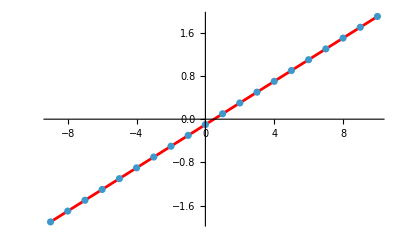

```mathematica
Show[ListLinePlot[Table[{i,(i-N[1/2])/ξ},{i,-L+1,L}],PlotStyle->Red],ListPlot[Table[{i,(i-N[1/2])/ξ},{i,-L+1,L}]]]
```

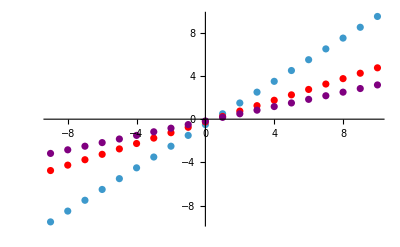

```mathematica
Show[ListPlot[Table[{i,(i-N[1/2])/1},{i,-L+1,L}]],ListPlot[Table[{i,(i-N[1/2])/2},{i,-L+1,L}],PlotStyle->Red],ListPlot[Table[{i,(i-N[1/2])/3},{i,-L+1,L}],PlotStyle->Purple]]
```

#### -Eigenvectors

```mathematica
(*Matrix of eigenvectors*)
U[L_,ξ_]:=Block[{m,evals,evecs,a,u},
m=HamiltGrad[L,ξ];
       {evals,evecs}=Eigensystem[N[m,NPrec]];
a=Transpose@SortBy[Transpose[{evals,evecs}],First];
u=a[[2]];
Return[N[u,NPrec]]
];

(*Matrix of normalized eigenvectors*)
UNorm[L_,ξ_]:=Block[{m,evals,evecs,a,u,unorm},
m=HamiltGrad[L,ξ];
(*Print[m//MatrixForm];*)
        {evals,evecs}=Eigensystem[N[m,NPrec]];
(*Print[evals];*)
a=Transpose@SortBy[Transpose[{evals,evecs}],First];
u=a[[2]];
unorm=ConstantArray[0.0,{2L,2L}];
Do[unorm[[i]]=Normalize[N[u[[i]],NPrec]],{i,1,Length[u]}];
Return[N[unorm,NPrec]]
];
```

```mathematica
UNorm[10,10];
```

### -Correlation matrix

Correlation Matrix:

```mathematica
(* Correlation matrix of the whole system*)

CorrTot[L_,ξ_]:=Block[{m,a,uL,Cxx,evals,evecs,ζk,u,unorm},
m=HamiltGrad[L,ξ];
(*Print[m//MatrixForm];*)
       {evals,evecs}=Eigensystem[N[m,NPrec]];
(*Print[evals];*)
a=Transpose@SortBy[Transpose[{evals,evecs}],First];
ζk=a[[1]];
u=a[[2]];
unorm=ConstantArray[0.0,{2L,2L}];
Do[unorm[[i]]=Normalize[N[u[[i]],NPrec]],{i,1,Length[u]}];
Cxx=Table[Sum[If[ζk[[k]]<0,1,0]unorm[[k,m]]unorm[[k,n]],{k,1,2L}],{m,1,2L},{n,1,2L}];
Return[N[Cxx,NPrec]];
]
```

### -Correlation matrix

-L=10

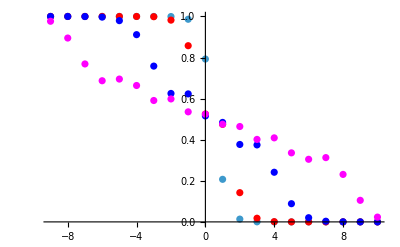

```mathematica
Show[ListPlot[Table[{i-10,CorrTot[10,1][[i,i]]},{i,1,20}]],ListPlot[Table[{i-10,CorrTot[10,2][[i,i]]},{i,1,20}],PlotStyle->Red],ListPlot[Table[{i-10,CorrTot[10,5][[i,i]]},{i,1,20}],PlotStyle->Blue],ListPlot[Table[{i-10,CorrTot[10,10][[i,i]]},{i,1,20}],PlotStyle->Magenta],GridLines->{{0},{}}]
```

### - Reduced Correlation matrix

Reduced Correlation Matrix half system:

We consider an interval consisting in the half right part of the chain   A = [1, ... L]

```mathematica
CA[Ctot_]:=Block[{CAij,CorrTot,L},
CorrTot=Ctot;
L=1/2Length[Ctot];
CAij=ConstantArray[0.0,{L,L}];
Do[CAij[[i,j]]=N[CorrTot[[i+L,j+L]],NPrec]
,{i,1,L},{j,1,L}];
Return[N[CAij,NPrec]];
]
```

```mathematica
CorrTot[5,5]//MatrixForm
```

(0.9576293724247107165377965767800024767451085769837507367551531160279804740903387799166564800196407852413310110480488016213785976199651023382444164377844773569004902255482402523602444396818764404578364395146648875715021352689749256908187182667494659726517242258857195909383284098877448055607807001031727024603652295989508049156661159784656427854396752125180815801682926658684602021031475963544385176348578128056011827327311284260970726861019534569847934891425468347615381092506250191759425322656624633133474931841336787427831892604984762786316673197254862912644293349046186989204074026889897766184764 | 0.09140627224265608393531952859362198634407570637270757288728050878166844024950718464847206469750727474667076197712925734372564540404483972968220785355072437555754277592337320108596197745209508380142956380408834609178929650025593281079970481811439867684349972364086510516199700131548052358885944678469204744536451327850371389360398551253305243513517497206162683022877406649168991902610440872528163386850164684460145385732820580128789902703059891630820812855834037051820923019668877687128380172923763418400005841072480229339222466168616446244864225325653254650440016109289158061314163640631466181675903 | -0.1204426687845269643199618518005550596376225279092882106354527074044168634678717789359340580564320442242681241910889738817192163416885097218539471656528325025354513845205103285834436198600554969378119758737861951696118359304704626802332807918774473309529011531388522591066032342943360353976431241614169959685007899534799990847369479054473376345495315594576309666362854084630318837930481968629082716961282510776335745674469831127253852511896454394077091929499406761034277298781291627110779067168305813967659609135397298294965260262758548943779564787853038933674534543216328781273518022176588245906816 | 0.08170009339760244033741513188097112170847568958333754620944035546379861412849792820618083730482188140828653126957857321698327389483602170546844777140785689588439219375748816698369186665470673610957296863896102684413254619265902997693774577261737374265414614054237234256222798187666758463394546257087462066879519370533627679695716598668831647168167740052833855716504801169173109097397644529665134624231116850546707140450617276521999755535704538781402996162961020987815838625562615578271687875377338876879429755932484525139195824561662794020434111375048737637953798570794271332644880098176666582239062 | 0.02019306799372492467645955653430951657986788115101320430743403703246673334084738831943918878169624725876858989216923831129314144518079460066709910134525530137301850295205533188768758866333583201633498336402863778506335489684997484489731134046590725140635992373050923575709022623494902912583163803494065758147713548200833926192625017459304912464651755716833091552163782471106519407491874095867207624999258087136756796130284818540502440320647860211153786386551790073587844901357179368730512884254907341575925880923926265269232193743631637973135404958608606813654131790477776974688154993418924358428427 | -0.06507697814858625450997472407074410982004313660283448915030151080567198497319995224711883433015483176251954873384096516059763924714373289696440477760284823827140347576496713059703631902938705635336917341209799644269892528821282416325568042601982105296573415207827236589879491124427151991675281833164212303369638784313433495977956326321456905196403625233511989373784986434361723971535100377996264680092282732569753452754459342011889613685117894531772736820772695111814665479505976480510682387330939538618218044938896649507770382808154455830457165327396655007969569736154768559024238447356408505754034 | -0.02058317952039456548709831490490584192932692684903344502483146147936642312289573203863058284757043994642367572584093644184993710845034434034989737301338583811319306465748449215650884350906659989556595076357899391369031221622311616570641242596059658277480302106026226608423992129700142220348438797332222989821477161137311839961812394934838229188661304701325591360984126834895418014941199637276877345930914820500599853361084574437348173656481755169521500318554768140289226927795091694000047158009128045821735171746812828050261458436855180673582795399609948845000455094884297372354967457182092305455389 | 0.0440358399387917395938939500544321928790225428550111579896778815814209084443376524063798759840916472758031142668087963488390922581281163277832377276419951091006594224368792652081734562621458130970385876021387937934982143125038030308235754338223276735679560058269097412237817355696323647467757644512074543165711010343830750198713434214736078311329341184053609215197672438309756008630078459863333975178390882598953842562399700892844021064267970984650603107510955992232777713463689943707353856944364343648132058000812516837665476979794206916398943480793945827907807979027783610789542505918304155118166 | 0.055516307484090001381544902346989479837664899806744381069426983106002645477251646137720124784717833929867070852879379650743310964384630739896622522868784143668177183374291616274836021557344271732537580079023329850463544746658217288610109940940256761880010930666252959574343004087788601058207784754368002468497015714346887795549216592912299419081765519172927552699152858101784673888547555391306164084876946880825315476841791148688827588595927019424856385806162748597416872160693464576044472493112807416383413706491130497325901387843309375888669205983373668233540069605780576599532345243624790331262078 | 0.030842393046716667434191612414994155465369388781524656149681657281112580820695358965400069324843241072148372696044099805968506091324794855498123623815991190926765101874606453486020011976302373184743100043901849916924191525921231827005616633855698201044450517036807199763523891159882556143448769307982223593609453174637159886416231440506833010600980843984959751499529365612102596604748641884058980047153859378236286376023217304827126438108848344124920214336757082554120484533718591431135818051729337453546340948050628054069945215468505208827038447768540926796411149780989209221962414024235994628478932
0.09140627224265608393531952859362198634407570637270757288728050878166844024950718464847206469750727474667076197712925734372564540404483972968220785355072437555754277592337320108596197745209508380142956380408834609178929650025593281079970481811439867684349972364086510516199700131548052358885944678469204744536451327850371389360398551253305243513517497206162683022877406649168991902610440872528163386850164684460145385732820580128789902703059891630820812855834037051820923019668877687128380172923763418400005841072480229339222466168616446244864225325653254650440016109289158061314163640631466181675903 | 0.80062419474312131864370691354199862256985576652537949696478820511089623452266412712133359608420583111839458206610812480216912311665865672451758613071135510414202173065838064334241602884098290999945263811924335396517458073840208988626555554762625917096142318329052128976692637506721656072759379722787888751371863433406932027348757386800508417683607366423579988144049763080875235069965763600141759239132890299012702662235286299285652782410006845105380104476927001045082668729382034571635110485713682824298150890630402799592977336954815559927425393963756937929521581614582918854779894590880508730109118 | 0.26946050066788009572870414191503715576264941828347568760508303016900054515230253600340014844747479153437179259957900966608429237223166921263381335748084727347029607729726963093640873999484621746125211314207832907161131143729133293192407522423373028425996678669431925500950757062761693654091940868470026488896033894662398995835070982357923901445647762015607016070285040495384651703451941151225959746771541621217538491579196505668820478333936065564840544454790312127910980035481826282286300585647548807020712470088143140838140372832347631815534855003526303757790091025814059644147187916220838731169494 | -0.19828971286792496804840045352341088910792547425828006177934709692850846708122190446391187404052205465544337182241402343080600357031094116774898538999700547622370351407744079707618627118236774825296455487651078959750753646481132380766126437855238857073151659805918983442418658631138810783254604121152588318957788691787519197915929691488026827592102688292330631971270519778204399888690119026021781093690907241282649229155154224558435791441162130267300728303995502722133934437130875596303303237880957450355985917549028147847455398357949204289181176569980267688635771926638636437220881346158957999326609 | -0.01568579354094369365489488264466821463935605686111806983275561459382014419005784535204069907604694596826276129173317324168339166459698255256331556834739982458384088673076749463364459423601765146993217815558279005466774693051375393815363279814789891256176388950471480054791129134352238188413797661667255449526461090901140098190439755587513117971678694327611080140742237218959045926124454401718662255859978821441857186112297775154693762662449932088215798876294538241739378696114847892207815126761452408260269698484694148799346068236302282567039701886121688271862382030124940385880406338650020897000454 | 0.12976384477050286820931068977089189429062722750764873758320559716444428016435156077504627459443547083738401163401023219063848283101791605424601128353756593980263238982450510092525138321304334482750737942464563675677089325705250700570225976654495277456302520682679170147044012742649064675585288672490267375065513955690389078186725275167380493668797701482531478938749628504934549335620875214582859639252908731775663848278118928126933494034401894105177759709542412156927948932574040635751830500907658372990626799054906736234511500923085368960466940213791967984592816167903016720381664430949649064481106 | 0.02835849263915244225295518175546210368936403068985693689897187832622833896608745705197444048810587138470038727498607864868130207126520984765858664527127288230091930184987491578675836165451859649302769602263038274365603834322645766526328483010793841926174910429326681392716263543816425811838547725553868303859016505854422421917527763669515627969676917890205522044553642352484839350624563350101580701925821662621224620936140645566186213733118027721584895018868308347207256281839143022162969361334611207835266947261579306189511887238240046950130978439606680499109602281845381242523108509063654578520559 | -0.088367223864921434968456472710326502152925147036320306326502546801342321289789512638774110818309218388805324820026186567856084466824439318246340487542187999926862264106454818464558499485730604834736415970544286685021767544575547363402313699722857306885068906709356581936485776804183442436248743682335099516116838793298840659708668936562184799977063059375338941166036692973901188677286409743196122424381648451887758974240970845680980045963922407972527487482452610630653156887090636602015079031400489263310914251204502497723046750867620367438862922635030652030650715470841808145089230985321296156378286 | -0.10277395096357959739285812504093998713613574774504620528280680707667497626217225626892445400216218022762313976636111872757099673657790718438783072172212295971074246248624745338528180074505348326233856860683401181106093735088126046572315974333079576340362845526829252965059198635140860249604037745478792998900989607688980603946991823533891729932773469896304749561799253648263275897559568938178734750661328238050933889363054428169271973897132101956955990949186811373433573503413150084147110823179521191406737711263973785360639152765066410237680866329886022876013627505473027481758684016353291891974312 | -0.055516307484090001381544902346989479837664899806744381069426983106002645477251646137720124784717833929867070852879379650743310964384630739896622522868784143668177183374291616274836021557344271732537580079023329850463544746658217288610109940940256761880010930666252959574343004087788601058207784754368002468497015714346887795549216592912299419081765519172927552699152858101784673888547555391306164084876946880825315476841791148688827588595927019424856385806162748597416872160693464576044472493112807416383413706491130497325901387843309375888669205983373668233540069605780576599532345243624790331262078
-0.1204426687845269643199618518005550596376225279092882106354527074044168634678717789359340580564320442242681241910889738817192163416885097218539471656528325025354513845205103285834436198600554969378119758737861951696118359304704626802332807918774473309529011531388522591066032342943360353976431241614169959685007899534799990847369479054473376345495315594576309666362854084630318837930481968629082716961282510776335745674469831127253852511896454394077091929499406761034277298781291627110779067168305813967659609135397298294965260262758548943779564787853038933674534543216328781273518022176588245906816 | 0.26946050066788009572870414191503715576264941828347568760508303016900054515230253600340014844747479153437179259957900966608429237223166921263381335748084727347029607729726963093640873999484621746125211314207832907161131143729133293192407522423373028425996678669431925500950757062761693654091940868470026488896033894662398995835070982357923901445647762015607016070285040495384651703451941151225959746771541621217538491579196505668820478333936065564840544454790312127910980035481826282286300585647548807020712470088143140838140372832347631815534855003526303757790091025814059644147187916220838731169494 | 0.61499295039257127662378665505312793079449305286299737077886060351920441284839298719199572072112590407347061739495147138664861893914355759356902256337484322106565117018254232247510988152073217169979921385968742790863435562914469558606794187125782581747882102369245601244553999479911771367632311670388989433705740179102453139572494092914045792968198729270769646408293767950820162879199687799920421416346191517006395493193151783732227324754234832552914077686009441082127115265871344733525077685256763990810476076400090378359918392091512792349825923270896538074515118709781946372635318299999097697382872 | 0.33070638402367393617511449020812653070115805124564412098636473765418856049872428601630811129902360788217719749619848195206242966904741788880123832972319493398102580807096660698002129605001602848411861024874314385081704748596760806296170815631036848562927003509458397943871756645653745628887280246637379627656284386657646576281658381292000598379483478269026585790054417929816016590881937440659587741633171742255093548340404833638875593288711298909062332058731155076062910263509063288849440173813523482165801749710186985177562798720741918659405982998340091998882527966205757075398606556321317651391264 | -0.06989598384201459212967546111322665382993885966830284470426879928394674722964831758585594933652649591491263653049322166144059218695744065109409452578781504829348056312807003447824896354943905367787354502919444256019870178799228692107195659469586435250073464755724960805334313550761963194155922058155680162608234975216595928093301727074935504821942309333498948415793989081625514849211772625243734372405282010913513553672562784786372222532468177867417796329451434748706575970576196858632607469114463529028961361236414698322960809294932734221401999051450880591462229113063468228470884302248208216873385 | -0.12987247438600958602686208045188903199495245358066462391661118092503066851373293329302146360888299616085724389732250093742602287581670549473394219913338420769572993283513360973025212669298135034754711580028742967914621251035848331875828316849206387963512096405604234307465794854347163865836429978933602642402628129837906705393716105864349374675674473575943935024403014040007761540958191016953392296646528397091941269666688072579711525699257040403142582571921394233802175226888193406737092179548155058591787584772068971077282199666844370123198662461185501540131715880769617336943722471749396315895631 | 0.00526281514767111422204216845454702668830094594064800248359075519001170406528286607095386564748494962560158798985282476726973133011340138103239487846621801338712458667578494304368500392734214690228152217241957849812736124224716047747978883256681521192926111259116375776386900104298011028631757650481243805557274225788972008342615249106968986920398864465912132094022801337470169781584307177336963338894015381845038562342825126863811235628255353034276721242115302539737347607981782625224431033107515076810736651158110702133444509796698418989901486470685490628308995152012370793181491771472302597257547 | 0.093630039012592549190498641164873528841226092976968308810093301991354025355072378709727976465794168014406912809879011335125815796937840699278735366008406013313986850782239761508243503413072751737017938142963865183149128786822707840882102532289672518814330019300520339700354777847163552722566320187147537571689581051188560743134821427631874669181051704034460262106264706348602886493129481516565755813321802270338144597669222114319092402246475938315294699903605636028026632966908462854259389362475640031418280762785609519057491848834604557337877787341885558313740666990965516076904148700044322128953761 | 0.088367223864921434968456472710326502152925147036320306326502546801342321289789512638774110818309218388805324820026186567856084466824439318246340487542187999926862264106454818464558499485730604834736415970544286685021767544575547363402313699722857306885068906709356581936485776804183442436248743682335099516116838793298840659708668936562184799977063059375338941166036692973901188677286409743196122424381648451887758974240970845680980045963922407972527487482452610630653156887090636602015079031400489263310914251204502497723046750867620367438862922635030652030650715470841808145089230985321296156378286 | 0.044035839938791739593893950054432192879022542855011157989677881581420908444337652406379875984091647275803114266808796348839092258128116327783237727641995109100659422436879265208173456262145813097038587602138793793498214312503803030823575433822327673567956005826909741223781735569632364746775764451207454316571101034383075019871343421473607831132934118405360921519767243830975600863007845986333397517839088259895384256239970089284402106426797098465060310751095599223277771346368994370735385694436434364813205800081251683766547697979420691639894348079394582790780797902778361078954250591830415511816599
0.08170009339760244033741513188097112170847568958333754620944035546379861412849792820618083730482188140828653126957857321698327389483602170546844777140785689588439219375748816698369186665470673610957296863896102684413254619265902997693774577261737374265414614054237234256222798187666758463394546257087462066879519370533627679695716598668831647168167740052833855716504801169173109097397644529665134624231116850546707140450617276521999755535704538781402996162961020987815838625562615578271687875377338876879429755932484525139195824561662794020434111375048737637953798570794271332644880098176666582239062 | -0.19828971286792496804840045352341088910792547425828006177934709692850846708122190446391187404052205465544337182241402343080600357031094116774898538999700547622370351407744079707618627118236774825296455487651078959750753646481132380766126437855238857073151659805918983442418658631138810783254604121152588318957788691787519197915929691488026827592102688292330631971270519778204399888690119026021781093690907241282649229155154224558435791441162130267300728303995502722133934437130875596303303237880957450355985917549028147847455398357949204289181176569980267688635771926638636437220881346158957999326609 | 0.33070638402367393617511449020812653070115805124564412098636473765418856049872428601630811129902360788217719749619848195206242966904741788880123832972319493398102580807096660698002129605001602848411861024874314385081704748596760806296170815631036848562927003509458397943871756645653745628887280246637379627656284386657646576281658381292000598379483478269026585790054417929816016590881937440659587741633171742255093548340404833638875593288711298909062332058731155076062910263509063288849440173813523482165801749710186985177562798720741918659405982998340091998882527966205757075398606556321317651391264 | 0.61110412580901207807246585138006155379201644695471693945939300610209070850047685966352840090551201966113047368839288037518905845487809095470341809569475567540346379790352644228103867073365445488124277960750651740561637131157668924747256639259020264145789496015656264704089641902027120705176081634730945738992780141010317778882458704810336876386565716921990695647748531475472641282325259224434633040978548050473493749339581290048740656347444265389172076837061047025129309627022398155655997384497848519271179932828629033813387861666232494953842707590089888372135650336874811751225872721381320419279591 | 0.27243649025221971750688766129148703640951274226073984266592421075013543395876785214401210623540875442151282411500373158547227220739364746750588731956746258950392121246905651946601293443260357254880250862739405827449754333651670821921462306172289500055650067858905612335464541766268390506789385575895576564866705327894156711553023412675112745533041546487492889639028832374067712855417618925619845198770847775335820307724064764042955608277878732888069785426665446882965374509196675261226249096318391655057452952411943921557995314726146018480368621664436983203782977406011854707111997865020508805994796 | -0.03855004420163484288470948588730468303832219693850603110395022414834252111223749233832260195281742173366636749786362795989811623688190873062698029189910192547411244687462986068351279080356263118604286332107558520386677879036745346678448772648352525957235358492562674007032472363896420202105737105444380561233320949312524951464952426098127761959531778058985573231237199401080580554098511442145559916788341284333809316007830898953840650099506270454547735710572871285334567022902622781075496321456820754898706407406727967131289160821106440044129057841134756099587991072030573351338589995626279105022186 | -0.073021432248843261844586090569752849544371904798590055979234965563923708629200597348794112667170618932113259146194087878613079278325516852765625283942199898102061722584024672878662991218174630147207309155825272836656900054357689907107127598417234119169357829194650829723656207803240520512291579265427072779843252918358282663459461253418279147998844042081628422087666678975845838928046976991375387594705944436314131305844267096960864762129360391480407615878136230417865243848073423438332122576072263861824050976080644487745561176963414317233842405197004112131616437067382402408668029451643028371328896 | -0.00526281514767111422204216845454702668830094594064800248359075519001170406528286607095386564748494962560158798985282476726973133011340138103239487846621801338712458667578494304368500392734214690228152217241957849812736124224716047747978883256681521192926111259116375776386900104298011028631757650481243805557274225788972008342615249106968986920398864465912132094022801337470169781584307177336963338894015381845038562342825126863811235628255353034276721242115302539737347607981782625224431033107515076810736651158110702133444509796698418989901486470685490628308995152012370793181491771472302597257547 | 0.02835849263915244225295518175546210368936403068985693689897187832622833896608745705197444048810587138470038727498607864868130207126520984765858664527127288230091930184987491578675836165451859649302769602263038274365603834322645766526328483010793841926174910429326681392716263543816425811838547725553868303859016505854422421917527763669515627969676917890205522044553642352484839350624563350101580701925821662621224620936140645566186213733118027721584895018868308347207256281839143022162969361334611207835266947261579306189511887238240046950130978439606680499109602281845381242523108509063654578520559 | 0.020583179520394565487098314904905841929326926849033445024831461479366423122895732038630582847570439946423675725840936441849937108450344340349897373013385838113193064657484492156508843509066599895565950763578993913690312216223116165706412425960596582774803021060262266084239921297001422203484387973322229898214771611373118399618123949348382291886613047013255913609841268348954180149411996372768773459309148205005998533610845744373481736564817551695215003185547681402892269277950916940000471580091280458217351717468128280502614584368551806735827953996099488450004550948842973723549674571820923054553886
0.02019306799372492467645955653430951657986788115101320430743403703246673334084738831943918878169624725876858989216923831129314144518079460066709910134525530137301850295205533188768758866333583201633498336402863778506335489684997484489731134046590725140635992373050923575709022623494902912583163803494065758147713548200833926192625017459304912464651755716833091552163782471106519407491874095867207624999258087136756796130284818540502440320647860211153786386551790073587844901357179368730512884254907341575925880923926265269232193743631637973135404958608606813654131790477776974688154993418924358428427 | -0.01568579354094369365489488264466821463935605686111806983275561459382014419005784535204069907604694596826276129173317324168339166459698255256331556834739982458384088673076749463364459423601765146993217815558279005466774693051375393815363279814789891256176388950471480054791129134352238188413797661667255449526461090901140098190439755587513117971678694327611080140742237218959045926124454401718662255859978821441857186112297775154693762662449932088215798876294538241739378696114847892207815126761452408260269698484694148799346068236302282567039701886121688271862382030124940385880406338650020897000454 | -0.06989598384201459212967546111322665382993885966830284470426879928394674722964831758585594933652649591491263653049322166144059218695744065109409452578781504829348056312807003447824896354943905367787354502919444256019870178799228692107195659469586435250073464755724960805334313550761963194155922058155680162608234975216595928093301727074935504821942309333498948415793989081625514849211772625243734372405282010913513553672562784786372222532468177867417796329451434748706575970576196858632607469114463529028961361236414698322960809294932734221401999051450880591462229113063468228470884302248208216873385 | 0.27243649025221971750688766129148703640951274226073984266592421075013543395876785214401210623540875442151282411500373158547227220739364746750588731956746258950392121246905651946601293443260357254880250862739405827449754333651670821921462306172289500055650067858905612335464541766268390506789385575895576564866705327894156711553023412675112745533041546487492889639028832374067712855417618925619845198770847775335820307724064764042955608277878732888069785426665446882965374509196675261226249096318391655057452952411943921557995314726146018480368621664436983203782977406011854707111997865020508805994796 | 0.53347546934850394031467676208938871001982801278021781599334189693764076103438054405345690579505759207377161307502098144254262552199616388816817740175648376242126342916934400828936966970648944835355245786466775145214927697459483941407418603611338373416367575135256306568205666382385307494510512357084014714421012035756726070889598640717099521035759629601506914976693788206390490435271472837284869417087149666918869863914687270264089985469254679646814223285273431735315168771017302128722608893628134631378453705693538196381861384249600381738968200134631219582496697415502964745513367881995046008732871 | 0.36012756775069391599693123988346696529075104859361923548646060542991641073309018195889753873937506903718990286442304701220370879439036309397578846827792843947687938021986934486441230255026039769797660592871668328008027882481146440429336881298454496868014668139094902876190693731408638483081247312641976378271664925346255111772755334076136414976457038302462441039654938037355354946849921397152146669377454756263395899612590846089653177843804750506809794979231515103248678969599624548990526075424776931385800565501330817565752725353534108915486289878829878410423442437667690484259789388106625568775286 | 0.03855004420163484288470948588730468303832219693850603110395022414834252111223749233832260195281742173366636749786362795989811623688190873062698029189910192547411244687462986068351279080356263118604286332107558520386677879036745346678448772648352525957235358492562674007032472363896420202105737105444380561233320949312524951464952426098127761959531778058985573231237199401080580554098511442145559916788341284333809316007830898953840650099506270454547735710572871285334567022902622781075496321456820754898706407406727967131289160821106440044129057841134756099587991072030573351338589995626279105022186 | -0.12987247438600958602686208045188903199495245358066462391661118092503066851373293329302146360888299616085724389732250093742602287581670549473394219913338420769572993283513360973025212669298135034754711580028742967914621251035848331875828316849206387963512096405604234307465794854347163865836429978933602642402628129837906705393716105864349374675674473575943935024403014040007761540958191016953392296646528397091941269666688072579711525699257040403142582571921394233802175226888193406737092179548155058591787584772068971077282199666844370123198662461185501540131715880769617336943722471749396315895631 | -0.12976384477050286820931068977089189429062722750764873758320559716444428016435156077504627459443547083738401163401023219063848283101791605424601128353756593980263238982450510092525138321304334482750737942464563675677089325705250700570225976654495277456302520682679170147044012742649064675585288672490267375065513955690389078186725275167380493668797701482531478938749628504934549335620875214582859639252908731775663848278118928126933494034401894105177759709542412156927948932574040635751830500907658372990626799054906736234511500923085368960466940213791967984592816167903016720381664430949649064481106 | -0.065076978148586254509974724070744109820043136602834489150301510805671984973199952247118834330154831762519548733840965160597639247143732896964404777602848238271403475764967130597036319029387056353369173412097996442698925288212824163255680426019821052965734152078272365898794911244271519916752818331642123033696387843134334959779563263214569051964036252335119893737849864343617239715351003779962646800922827325697534527544593420118896136851178945317727368207726951118146654795059764805106823873309395386182180449388966495077703828081544558304571653273966550079695697361547685590242384473564085057540336
-0.06507697814858625450997472407074410982004313660283448915030151080567198497319995224711883433015483176251954873384096516059763924714373289696440477760284823827140347576496713059703631902938705635336917341209799644269892528821282416325568042601982105296573415207827236589879491124427151991675281833164212303369638784313433495977956326321456905196403625233511989373784986434361723971535100377996264680092282732569753452754459342011889613685117894531772736820772695111814665479505976480510682387330939538618218044938896649507770382808154455830457165327396655007969569736154768559024238447356408505754034 | 0.12976384477050286820931068977089189429062722750764873758320559716444428016435156077504627459443547083738401163401023219063848283101791605424601128353756593980263238982450510092525138321304334482750737942464563675677089325705250700570225976654495277456302520682679170147044012742649064675585288672490267375065513955690389078186725275167380493668797701482531478938749628504934549335620875214582859639252908731775663848278118928126933494034401894105177759709542412156927948932574040635751830500907658372990626799054906736234511500923085368960466940213791967984592816167903016720381664430949649064481106 | -0.12987247438600958602686208045188903199495245358066462391661118092503066851373293329302146360888299616085724389732250093742602287581670549473394219913338420769572993283513360973025212669298135034754711580028742967914621251035848331875828316849206387963512096405604234307465794854347163865836429978933602642402628129837906705393716105864349374675674473575943935024403014040007761540958191016953392296646528397091941269666688072579711525699257040403142582571921394233802175226888193406737092179548155058591787584772068971077282199666844370123198662461185501540131715880769617336943722471749396315895631 | -0.03855004420163484288470948588730468303832219693850603110395022414834252111223749233832260195281742173366636749786362795989811623688190873062698029189910192547411244687462986068351279080356263118604286332107558520386677879036745346678448772648352525957235358492562674007032472363896420202105737105444380561233320949312524951464952426098127761959531778058985573231237199401080580554098511442145559916788341284333809316007830898953840650099506270454547735710572871285334567022902622781075496321456820754898706407406727967131289160821106440044129057841134756099587991072030573351338589995626279105022186 | 0.36012756775069391599693123988346696529075104859361923548646060542991641073309018195889753873937506903718990286442304701220370879439036309397578846827792843947687938021986934486441230255026039769797660592871668328008027882481146440429336881298454496868014668139094902876190693731408638483081247312641976378271664925346255111772755334076136414976457038302462441039654938037355354946849921397152146669377454756263395899612590846089653177843804750506809794979231515103248678969599624548990526075424776931385800565501330817565752725353534108915486289878829878410423442437667690484259789388106625568775286 | 0.46652453065149605968532323791061128998017198721978218400665810306235923896561945594654309420494240792622838692497901855745737447800383611183182259824351623757873657083065599171063033029351055164644754213533224854785072302540516058592581396388661626583632424864743693431794333617614692505489487642915985285578987964243273929110401359282900478964240370398493085023306211793609509564728527162715130582912850333081130136085312729735910014530745320353185776714726568264684831228982697871277391106371865368621546294306461803618138615750399618261031799865368780417503302584497035254486632118004953991267129 | 0.27243649025221971750688766129148703640951274226073984266592421075013543395876785214401210623540875442151282411500373158547227220739364746750588731956746258950392121246905651946601293443260357254880250862739405827449754333651670821921462306172289500055650067858905612335464541766268390506789385575895576564866705327894156711553023412675112745533041546487492889639028832374067712855417618925619845198770847775335820307724064764042955608277878732888069785426665446882965374509196675261226249096318391655057452952411943921557995314726146018480368621664436983203782977406011854707111997865020508805994796 | 0.069895983842014592129675461113226653829938859668302844704268799283946747229648317585855949336526495914912636530493221661440592186957440651094094525787815048293480563128070034478248963549439053677873545029194442560198701787992286921071956594695864352500734647557249608053343135507619631941559220581556801626082349752165959280933017270749355048219423093334989484157939890816255148492117726252437343724052820109135135536725627847863722225324681778674177963294514347487065759705761968586326074691144635290289613612364146983229608092949327342214019990514508805914622291130634682284708843022482082168733851 | -0.01568579354094369365489488264466821463935605686111806983275561459382014419005784535204069907604694596826276129173317324168339166459698255256331556834739982458384088673076749463364459423601765146993217815558279005466774693051375393815363279814789891256176388950471480054791129134352238188413797661667255449526461090901140098190439755587513117971678694327611080140742237218959045926124454401718662255859978821441857186112297775154693762662449932088215798876294538241739378696114847892207815126761452408260269698484694148799346068236302282567039701886121688271862382030124940385880406338650020897000454 | -0.02019306799372492467645955653430951657986788115101320430743403703246673334084738831943918878169624725876858989216923831129314144518079460066709910134525530137301850295205533188768758866333583201633498336402863778506335489684997484489731134046590725140635992373050923575709022623494902912583163803494065758147713548200833926192625017459304912464651755716833091552163782471106519407491874095867207624999258087136756796130284818540502440320647860211153786386551790073587844901357179368730512884254907341575925880923926265269232193743631637973135404958608606813654131790477776974688154993418924358428427
-0.02058317952039456548709831490490584192932692684903344502483146147936642312289573203863058284757043994642367572584093644184993710845034434034989737301338583811319306465748449215650884350906659989556595076357899391369031221622311616570641242596059658277480302106026226608423992129700142220348438797332222989821477161137311839961812394934838229188661304701325591360984126834895418014941199637276877345930914820500599853361084574437348173656481755169521500318554768140289226927795091694000047158009128045821735171746812828050261458436855180673582795399609948845000455094884297372354967457182092305455389 | 0.02835849263915244225295518175546210368936403068985693689897187832622833896608745705197444048810587138470038727498607864868130207126520984765858664527127288230091930184987491578675836165451859649302769602263038274365603834322645766526328483010793841926174910429326681392716263543816425811838547725553868303859016505854422421917527763669515627969676917890205522044553642352484839350624563350101580701925821662621224620936140645566186213733118027721584895018868308347207256281839143022162969361334611207835266947261579306189511887238240046950130978439606680499109602281845381242523108509063654578520559 | 0.00526281514767111422204216845454702668830094594064800248359075519001170406528286607095386564748494962560158798985282476726973133011340138103239487846621801338712458667578494304368500392734214690228152217241957849812736124224716047747978883256681521192926111259116375776386900104298011028631757650481243805557274225788972008342615249106968986920398864465912132094022801337470169781584307177336963338894015381845038562342825126863811235628255353034276721242115302539737347607981782625224431033107515076810736651158110702133444509796698418989901486470685490628308995152012370793181491771472302597257547 | -0.073021432248843261844586090569752849544371904798590055979234965563923708629200597348794112667170618932113259146194087878613079278325516852765625283942199898102061722584024672878662991218174630147207309155825272836656900054357689907107127598417234119169357829194650829723656207803240520512291579265427072779843252918358282663459461253418279147998844042081628422087666678975845838928046976991375387594705944436314131305844267096960864762129360391480407615878136230417865243848073423438332122576072263861824050976080644487745561176963414317233842405197004112131616437067382402408668029451643028371328896 | 0.03855004420163484288470948588730468303832219693850603110395022414834252111223749233832260195281742173366636749786362795989811623688190873062698029189910192547411244687462986068351279080356263118604286332107558520386677879036745346678448772648352525957235358492562674007032472363896420202105737105444380561233320949312524951464952426098127761959531778058985573231237199401080580554098511442145559916788341284333809316007830898953840650099506270454547735710572871285334567022902622781075496321456820754898706407406727967131289160821106440044129057841134756099587991072030573351338589995626279105022186 | 0.27243649025221971750688766129148703640951274226073984266592421075013543395876785214401210623540875442151282411500373158547227220739364746750588731956746258950392121246905651946601293443260357254880250862739405827449754333651670821921462306172289500055650067858905612335464541766268390506789385575895576564866705327894156711553023412675112745533041546487492889639028832374067712855417618925619845198770847775335820307724064764042955608277878732888069785426665446882965374509196675261226249096318391655057452952411943921557995314726146018480368621664436983203782977406011854707111997865020508805994796 | 0.38889587419098792192753414861993844620798355304528306054060699389790929149952314033647159909448798033886952631160711962481094154512190904529658190430524432459653620209647355771896132926634554511875722039249348259438362868842331075252743360740979735854210503984343735295910358097972879294823918365269054261007219858989682221117541295189663123613434283078009304352251468524527358717674740775565366959021451949526506250660418709951259343652555734610827923162938952974870690372977601844344002615502151480728820067171370966186612138333767505046157292409910111627864349663125188248774127278618679580720409 | 0.33070638402367393617511449020812653070115805124564412098636473765418856049872428601630811129902360788217719749619848195206242966904741788880123832972319493398102580807096660698002129605001602848411861024874314385081704748596760806296170815631036848562927003509458397943871756645653745628887280246637379627656284386657646576281658381292000598379483478269026585790054417929816016590881937440659587741633171742255093548340404833638875593288711298909062332058731155076062910263509063288849440173813523482165801749710186985177562798720741918659405982998340091998882527966205757075398606556321317651391264 | 0.19828971286792496804840045352341088910792547425828006177934709692850846708122190446391187404052205465544337182241402343080600357031094116774898538999700547622370351407744079707618627118236774825296455487651078959750753646481132380766126437855238857073151659805918983442418658631138810783254604121152588318957788691787519197915929691488026827592102688292330631971270519778204399888690119026021781093690907241282649229155154224558435791441162130267300728303995502722133934437130875596303303237880957450355985917549028147847455398357949204289181176569980267688635771926638636437220881346158957999326609 | 0.081700093397602440337415131880971121708475689583337546209440355463798614128497928206180837304821881408286531269578573216983273894836021705468447771407856895884392193757488166983691866654706736109572968638961026844132546192659029976937745772617373742654146140542372342562227981876667584633945462570874620668795193705336276796957165986688316471681677400528338557165048011691731090973976445296651346242311168505467071404506172765219997555357045387814029961629610209878158386255626155782716878753773388768794297559324845251391958245616627940204341113750487376379537985707942713326448800981766665822390624
0.0440358399387917395938939500544321928790225428550111579896778815814209084443376524063798759840916472758031142668087963488390922581281163277832377276419951091006594224368792652081734562621458130970385876021387937934982143125038030308235754338223276735679560058269097412237817355696323647467757644512074543165711010343830750198713434214736078311329341184053609215197672438309756008630078459863333975178390882598953842562399700892844021064267970984650603107510955992232777713463689943707353856944364343648132058000812516837665476979794206916398943480793945827907807979027783610789542505918304155118166 | -0.088367223864921434968456472710326502152925147036320306326502546801342321289789512638774110818309218388805324820026186567856084466824439318246340487542187999926862264106454818464558499485730604834736415970544286685021767544575547363402313699722857306885068906709356581936485776804183442436248743682335099516116838793298840659708668936562184799977063059375338941166036692973901188677286409743196122424381648451887758974240970845680980045963922407972527487482452610630653156887090636602015079031400489263310914251204502497723046750867620367438862922635030652030650715470841808145089230985321296156378286 | 0.093630039012592549190498641164873528841226092976968308810093301991354025355072378709727976465794168014406912809879011335125815796937840699278735366008406013313986850782239761508243503413072751737017938142963865183149128786822707840882102532289672518814330019300520339700354777847163552722566320187147537571689581051188560743134821427631874669181051704034460262106264706348602886493129481516565755813321802270338144597669222114319092402246475938315294699903605636028026632966908462854259389362475640031418280762785609519057491848834604557337877787341885558313740666990965516076904148700044322128953761 | -0.00526281514767111422204216845454702668830094594064800248359075519001170406528286607095386564748494962560158798985282476726973133011340138103239487846621801338712458667578494304368500392734214690228152217241957849812736124224716047747978883256681521192926111259116375776386900104298011028631757650481243805557274225788972008342615249106968986920398864465912132094022801337470169781584307177336963338894015381845038562342825126863811235628255353034276721242115302539737347607981782625224431033107515076810736651158110702133444509796698418989901486470685490628308995152012370793181491771472302597257547 | -0.12987247438600958602686208045188903199495245358066462391661118092503066851373293329302146360888299616085724389732250093742602287581670549473394219913338420769572993283513360973025212669298135034754711580028742967914621251035848331875828316849206387963512096405604234307465794854347163865836429978933602642402628129837906705393716105864349374675674473575943935024403014040007761540958191016953392296646528397091941269666688072579711525699257040403142582571921394233802175226888193406737092179548155058591787584772068971077282199666844370123198662461185501540131715880769617336943722471749396315895631 | 0.069895983842014592129675461113226653829938859668302844704268799283946747229648317585855949336526495914912636530493221661440592186957440651094094525787815048293480563128070034478248963549439053677873545029194442560198701787992286921071956594695864352500734647557249608053343135507619631941559220581556801626082349752165959280933017270749355048219423093334989484157939890816255148492117726252437343724052820109135135536725627847863722225324681778674177963294514347487065759705761968586326074691144635290289613612364146983229608092949327342214019990514508805914622291130634682284708843022482082168733851 | 0.33070638402367393617511449020812653070115805124564412098636473765418856049872428601630811129902360788217719749619848195206242966904741788880123832972319493398102580807096660698002129605001602848411861024874314385081704748596760806296170815631036848562927003509458397943871756645653745628887280246637379627656284386657646576281658381292000598379483478269026585790054417929816016590881937440659587741633171742255093548340404833638875593288711298909062332058731155076062910263509063288849440173813523482165801749710186985177562798720741918659405982998340091998882527966205757075398606556321317651391264 | 0.38500704960742872337621334494687206920550694713700262922113939648079558715160701280800427927887409592652938260504852861335138106085644240643097743662515677893434882981745767752489011847926782830020078614031257209136564437085530441393205812874217418252117897630754398755446000520088228632367688329611010566294259820897546860427505907085954207031801270729230353591706232049179837120800312200079578583653808482993604506806848216267772675245765167447085922313990558917872884734128655266474922314743236009189523923599909621640081607908487207650174076729103461925484881290218053627364681700000902302617128 | 0.26946050066788009572870414191503715576264941828347568760508303016900054515230253600340014844747479153437179259957900966608429237223166921263381335748084727347029607729726963093640873999484621746125211314207832907161131143729133293192407522423373028425996678669431925500950757062761693654091940868470026488896033894662398995835070982357923901445647762015607016070285040495384651703451941151225959746771541621217538491579196505668820478333936065564840544454790312127910980035481826282286300585647548807020712470088143140838140372832347631815534855003526303757790091025814059644147187916220838731169494 | 0.12044266878452696431996185180055505963762252790928821063545270740441686346787177893593405805643204422426812419108897388171921634168850972185394716565283250253545138452051032858344361986005549693781197587378619516961183593047046268023328079187744733095290115313885225910660323429433603539764312416141699596850078995347999908473694790544733763454953155945763096663628540846303188379304819686290827169612825107763357456744698311272538525118964543940770919294994067610342772987812916271107790671683058139676596091353972982949652602627585489437795647878530389336745345432163287812735180221765882459068161
0.055516307484090001381544902346989479837664899806744381069426983106002645477251646137720124784717833929867070852879379650743310964384630739896622522868784143668177183374291616274836021557344271732537580079023329850463544746658217288610109940940256761880010930666252959574343004087788601058207784754368002468497015714346887795549216592912299419081765519172927552699152858101784673888547555391306164084876946880825315476841791148688827588595927019424856385806162748597416872160693464576044472493112807416383413706491130497325901387843309375888669205983373668233540069605780576599532345243624790331262078 | -0.10277395096357959739285812504093998713613574774504620528280680707667497626217225626892445400216218022762313976636111872757099673657790718438783072172212295971074246248624745338528180074505348326233856860683401181106093735088126046572315974333079576340362845526829252965059198635140860249604037745478792998900989607688980603946991823533891729932773469896304749561799253648263275897559568938178734750661328238050933889363054428169271973897132101956955990949186811373433573503413150084147110823179521191406737711263973785360639152765066410237680866329886022876013627505473027481758684016353291891974312 | 0.088367223864921434968456472710326502152925147036320306326502546801342321289789512638774110818309218388805324820026186567856084466824439318246340487542187999926862264106454818464558499485730604834736415970544286685021767544575547363402313699722857306885068906709356581936485776804183442436248743682335099516116838793298840659708668936562184799977063059375338941166036692973901188677286409743196122424381648451887758974240970845680980045963922407972527487482452610630653156887090636602015079031400489263310914251204502497723046750867620367438862922635030652030650715470841808145089230985321296156378286 | 0.02835849263915244225295518175546210368936403068985693689897187832622833896608745705197444048810587138470038727498607864868130207126520984765858664527127288230091930184987491578675836165451859649302769602263038274365603834322645766526328483010793841926174910429326681392716263543816425811838547725553868303859016505854422421917527763669515627969676917890205522044553642352484839350624563350101580701925821662621224620936140645566186213733118027721584895018868308347207256281839143022162969361334611207835266947261579306189511887238240046950130978439606680499109602281845381242523108509063654578520559 | -0.12976384477050286820931068977089189429062722750764873758320559716444428016435156077504627459443547083738401163401023219063848283101791605424601128353756593980263238982450510092525138321304334482750737942464563675677089325705250700570225976654495277456302520682679170147044012742649064675585288672490267375065513955690389078186725275167380493668797701482531478938749628504934549335620875214582859639252908731775663848278118928126933494034401894105177759709542412156927948932574040635751830500907658372990626799054906736234511500923085368960466940213791967984592816167903016720381664430949649064481106 | -0.01568579354094369365489488264466821463935605686111806983275561459382014419005784535204069907604694596826276129173317324168339166459698255256331556834739982458384088673076749463364459423601765146993217815558279005466774693051375393815363279814789891256176388950471480054791129134352238188413797661667255449526461090901140098190439755587513117971678694327611080140742237218959045926124454401718662255859978821441857186112297775154693762662449932088215798876294538241739378696114847892207815126761452408260269698484694148799346068236302282567039701886121688271862382030124940385880406338650020897000454 | 0.19828971286792496804840045352341088910792547425828006177934709692850846708122190446391187404052205465544337182241402343080600357031094116774898538999700547622370351407744079707618627118236774825296455487651078959750753646481132380766126437855238857073151659805918983442418658631138810783254604121152588318957788691787519197915929691488026827592102688292330631971270519778204399888690119026021781093690907241282649229155154224558435791441162130267300728303995502722133934437130875596303303237880957450355985917549028147847455398357949204289181176569980267688635771926638636437220881346158957999326609 | 0.26946050066788009572870414191503715576264941828347568760508303016900054515230253600340014844747479153437179259957900966608429237223166921263381335748084727347029607729726963093640873999484621746125211314207832907161131143729133293192407522423373028425996678669431925500950757062761693654091940868470026488896033894662398995835070982357923901445647762015607016070285040495384651703451941151225959746771541621217538491579196505668820478333936065564840544454790312127910980035481826282286300585647548807020712470088143140838140372832347631815534855003526303757790091025814059644147187916220838731169494 | 0.19937580525687868135629308645800137743014423347462050303521179488910376547733587287866640391579416888160541793389187519783087688334134327548241386928864489585797826934161935665758397115901709000054736188075664603482541926159791011373444445237374082903857681670947871023307362493278343927240620277212111248628136566593067972651242613199491582316392633576420011855950236919124764930034236399858240760867109700987297337764713700714347217589993154894619895523072998954917331270617965428364889514286317175701849109369597200407022663045184440072574606036243062070478418385417081145220105409119491269890882 | 0.091406272242656083935319528593621986344075706372707572887280508781668440249507184648472064697507274746670761977129257343725645404044839729682207853550724375557542775923373201085961977452095083801429563804088346091789296500255932810799704818114398676843499723640865105161997001315480523588859446784692047445364513278503713893603985512533052435135174972061626830228774066491689919026104408725281633868501646844601453857328205801287899027030598916308208128558340370518209230196688776871283801729237634184000058410724802293392224661686164462448642253256532546504400161092891580613141636406314661816759027
0.030842393046716667434191612414994155465369388781524656149681657281112580820695358965400069324843241072148372696044099805968506091324794855498123623815991190926765101874606453486020011976302373184743100043901849916924191525921231827005616633855698201044450517036807199763523891159882556143448769307982223593609453174637159886416231440506833010600980843984959751499529365612102596604748641884058980047153859378236286376023217304827126438108848344124920214336757082554120484533718591431135818051729337453546340948050628054069945215468505208827038447768540926796411149780989209221962414024235994628478932 | -0.055516307484090001381544902346989479837664899806744381069426983106002645477251646137720124784717833929867070852879379650743310964384630739896622522868784143668177183374291616274836021557344271732537580079023329850463544746658217288610109940940256761880010930666252959574343004087788601058207784754368002468497015714346887795549216592912299419081765519172927552699152858101784673888547555391306164084876946880825315476841791148688827588595927019424856385806162748597416872160693464576044472493112807416383413706491130497325901387843309375888669205983373668233540069605780576599532345243624790331262078 | 0.044035839938791739593893950054432192879022542855011157989677881581420908444337652406379875984091647275803114266808796348839092258128116327783237727641995109100659422436879265208173456262145813097038587602138793793498214312503803030823575433822327673567956005826909741223781735569632364746775764451207454316571101034383075019871343421473607831132934118405360921519767243830975600863007845986333397517839088259895384256239970089284402106426797098465060310751095599223277771346368994370735385694436434364813205800081251683766547697979420691639894348079394582790780797902778361078954250591830415511816599 | 0.020583179520394565487098314904905841929326926849033445024831461479366423122895732038630582847570439946423675725840936441849937108450344340349897373013385838113193064657484492156508843509066599895565950763578993913690312216223116165706412425960596582774803021060262266084239921297001422203484387973322229898214771611373118399618123949348382291886613047013255913609841268348954180149411996372768773459309148205005998533610845744373481736564817551695215003185547681402892269277950916940000471580091280458217351717468128280502614584368551806735827953996099488450004550948842973723549674571820923054553886 | -0.065076978148586254509974724070744109820043136602834489150301510805671984973199952247118834330154831762519548733840965160597639247143732896964404777602848238271403475764967130597036319029387056353369173412097996442698925288212824163255680426019821052965734152078272365898794911244271519916752818331642123033696387843134334959779563263214569051964036252335119893737849864343617239715351003779962646800922827325697534527544593420118896136851178945317727368207726951118146654795059764805106823873309395386182180449388966495077703828081544558304571653273966550079695697361547685590242384473564085057540336 | -0.02019306799372492467645955653430951657986788115101320430743403703246673334084738831943918878169624725876858989216923831129314144518079460066709910134525530137301850295205533188768758866333583201633498336402863778506335489684997484489731134046590725140635992373050923575709022623494902912583163803494065758147713548200833926192625017459304912464651755716833091552163782471106519407491874095867207624999258087136756796130284818540502440320647860211153786386551790073587844901357179368730512884254907341575925880923926265269232193743631637973135404958608606813654131790477776974688154993418924358428427 | 0.081700093397602440337415131880971121708475689583337546209440355463798614128497928206180837304821881408286531269578573216983273894836021705468447771407856895884392193757488166983691866654706736109572968638961026844132546192659029976937745772617373742654146140542372342562227981876667584633945462570874620668795193705336276796957165986688316471681677400528338557165048011691731090973976445296651346242311168505467071404506172765219997555357045387814029961629610209878158386255626155782716878753773388768794297559324845251391958245616627940204341113750487376379537985707942713326448800981766665822390624 | 0.12044266878452696431996185180055505963762252790928821063545270740441686346787177893593405805643204422426812419108897388171921634168850972185394716565283250253545138452051032858344361986005549693781197587378619516961183593047046268023328079187744733095290115313885225910660323429433603539764312416141699596850078995347999908473694790544733763454953155945763096663628540846303188379304819686290827169612825107763357456744698311272538525118964543940770919294994067610342772987812916271107790671683058139676596091353972982949652602627585489437795647878530389336745345432163287812735180221765882459068161 | 0.091406272242656083935319528593621986344075706372707572887280508781668440249507184648472064697507274746670761977129257343725645404044839729682207853550724375557542775923373201085961977452095083801429563804088346091789296500255932810799704818114398676843499723640865105161997001315480523588859446784692047445364513278503713893603985512533052435135174972061626830228774066491689919026104408725281633868501646844601453857328205801287899027030598916308208128558340370518209230196688776871283801729237634184000058410724802293392224661686164462448642253256532546504400161092891580613141636406314661816759027 | 0.042370627575289283462203423219997523254891423016249263244846883972019525909661220083343519980359214758668988951951198378621402380034897661755583562215522643099509774451759747639755560318123559542163560485335112428497864731025074309181281733250534027348275774114280409061671590112255194439219299896827297539634770401049195084333884021534357214560324787481918419831707334131539797896852403645561482365142187194398817267268871573902927313898046543015206510857453165238461890749374980824057467734337536686652506815866321257216810739501523721368332680274513708735570665095381301079592597311010223381523601)

## -Interval starting from generic x0

### -CA at boundary point x0

#### - Numerical correlation matrix

```mathematica
CAx0[Ctot_,x0_]:=Block[{CAij,CorrTot,L},
CorrTot=Ctot;
L=If[x0>=0,1/2Length[Ctot]-x0,1/2Length[Ctot]+Abs[x0]];
CAij=ConstantArray[0.0,{L,L}];
Do[CAij[[i,j]]=N[CorrTot[[i+L+2x0,j+L+2x0]],NPrec]
,{i,1,L},{j,1,L}];
Return[N[CAij,NPrec]];
]
```

#### - Analytical correlation matrix

```mathematica
CorrMatAnx0[L_,ξ_,x0_]:=Block[{M, k, j,len},
len=If[x0>=0,L-x0,L+Abs[x0]];
M= ConstantArray[0, {len, len }];
Do[
M[[i, j]]= If[i==j,If[x0≥ 0,(1-N[BesselJ[0,ξ]^2,NPrec])/2-Sum[N[BesselJ[k,ξ]^2,NPrec],{k,1,+x0+i-1}],If[Abs[x0]-i>=0,(1+N[BesselJ[0,ξ]^2,NPrec])/2+Sum[N[BesselJ[k,ξ]^2,NPrec],{k,-(Abs[x0]-i),-1}],(1-N[BesselJ[0,ξ]^2,NPrec])/2-Sum[N[BesselJ[k,ξ]^2,NPrec],{k,1,i+x0-1}]]],ξ/(2(i-j))(N[BesselJ[i-1+x0,ξ] BesselJ[j+x0,ξ],NPrec]-N[BesselJ[i+x0,ξ] BesselJ[j-1+x0,ξ],NPrec])] ,
{i, 1,len}, {j,1,len}];
Return[N[M,NPrec]]
]
```

```mathematica
(*L=40, ξ =20, x0=4*)
```

```mathematica
CAx0[CorrTot[40,20],4]//MatrixForm
```

(0.429018986405257199880490452089414981551623141975023704192394209092299659708929923538111895643896929 | 0.300504442741848008993965051705960693120327718590895393114543014741633163593821976097074510198801241 | 0.0787251834466288384234636040731403829765777432011310624903441714531027696365436057614584765388279325 | -0.060653946861653857248100682055869576054176608144687637155581933783011138890023859615521616781946323 | -0.0687927833526030419036006476679790733456864113026107565704401144073566819512659801939747997786841807 | -0.010905086130089021178461684805197376423770832277937655394959256403054592187242146051505905633142842 | 0.033621732646053952281048815800938318758423472161778824469854552163238385820322014365870985462890803 | 0.035462620155022557782347139000190701792038528925802106614164924977864392434973270493790510105345235 | 0.010860049410033229150950653600764221864526636857594179130833781054117008077500017950580501637533932 | -0.01303400468352544079801766044578275057235811339055635987667775808535673854933653471923930088430567 | -0.02202482940641864238122974357424216148152027650021005462721942964922239319708935077513802761425289 | -0.017357768701507642738360537837196953227191110760287576827650685999352286686873875138675118897195709 | -0.0070938062326412345003243935159819626003160797529729623364138296652183794020172636437101929108005081 | 0.001867308136824323037351905405135289238705464505544604665598058670616687738897998182548266896484643 | 0.0066845028882537142674088634526236247245174938661183917585599526936496787838700776682458337753223676 | 0.0077050385168336621415778905434751205493552344893800617650051157112290977836055139250568714367810305 | 0.0065301757433687522199921264026452376212568546722413167040787537688479034959466800865164374871189831 | 0.00464314379337958442322949487946142239125872482569512062170814997635472070710788245462862767766846353 | 0.00291368353775499090112847990135720445762327485157667405090104955109204267799299543929145944151314372 | 0.00165666136237537185678494240533490259490487879043923883865212504954528013497182443747698785904936916 | 0.000867282147229806783640468887644062507245455410565349933460555584172750893921367599362481308130989313 | 0.000422612529358506255469225154588864660033460373890789496402163718808240297205452498833862049061391521 | 0.000193199299769006720401420329563831804037160152972201749347673026087861950804969443829530932734840349 | 0.0000833614017795484293598890564537657060312669501531300397012765449582541626217516921085957691012277192 | 0.0000341109298421235716250994039507754030880534458054429734530976345950292821832497956978578014192230631 | 0.0000132887057409463819311373902778371063756390060544140717748801385485382166674963964467859060311825619 | 4.94475564115099652245368525557552703797874059604379541018989461340931993406033226235190468281852745×10^-6 | 1.76230694112389804947237399546209693895492523329986037655761584253057164711581575115992273169477088×10^-6 | 6.03018553745173455972309690424583944818517798367024728727015213922270458691607274204347642025202325×10^-7 | 1.98518094117912260878076813668574562619364500483823875290782620100663870795613605112185907061668593×10^-7 | 6.29930329521145701767071823109813769896865444691632535505777603399297948948166293867587764375750623×10^-8 | 1.92984877031224485308096072938512419808682880107326469995001143044961000974462165933288114969989335×10^-8 | 5.71642934225791440793092109344392338339974017233533042069838637449373288407564919107366418737385883×10^-9 | 1.63884714242340138866616392209370432373121004338614079146067798341616268946667850454826264468806726×10^-9 | 4.53398597537467641406845272062651891306714815970355687899744773076414160519151158401926318769180074×10^-10 | 1.14260711670717515424247651709298651974311253793297206647372034105579707632736178467943639597990471×10^-10
0.300504442741848008993965051705960693120327718590895393114543014741633163593821976097074510198801241 | 0.406166687653406071332950275480098473071655908079823345000570685701153711538778606666578168373848128 | 0.308831788073454072474003136118861796092797044707480175513607778722137868137482928592350459683638897 | 0.106573889397443605066471726820252994882926008163742559447530931405828254569493981546801469196305983 | -0.049487198027689584067232041925092172829027654544495358769060870365633627100869197932875944246221627 | -0.0877080902362463900030518351072906722471772008487164302273164319430361512307680139595142700763161339 | -0.039095611159332307663144936152308532800019800575027375408802458537752117056651913955078796644063106 | 0.024346514500454013883153198420062877614605869600000233778774934485579733262245258312888122490069693 | 0.0534504052241059120326745604420908094604758837585189484889879251480192826371932381164295715082552231 | 0.041720609638533192668207867752672292503663359974106234680877422173118788380247467904508795494606478 | 0.009096938544441157544880420698499571986926514180687313340096794408611001368576454156591069841209372 | -0.021902069115765368211255148794713122553074197347506820044812945427556138146103518192050623518393525 | -0.0393045714934943298395373785779647018761956752668486396192003443223633749821795290094890578015829298 | -0.0423314509904732080619511296705152800569456969571065776411663222212478731642678374893041762122100748 | -0.0360898851595033449524529201547189723958601828106407165267732859556270047840847740663742961741987571 | -0.0264008002873041145848210197960024440574724093877546076712605526753512371166363514888506311248519086 | -0.0171998442203985447086229999175132434186505096563733841141143459011974593323313622377250796150717155 | -0.0101942865555378326332483508799676289820979534755372796896182830918324609653840879252008363731022319 | -0.00557334429709203690441887983328432207243569838833756535877162913560492576445255508105085876706079275 | -0.00283812796237599112725103880201359607411945078255845498094178169393783810597603255071489124017613039 | -0.00135601699745426540106845018559639752738222599847931737856204020381635921312139984569293375221976752 | -0.000611334416230340449827942489513034906017213225102906420271266501841455643728988087243201919032556589 | -0.00026125051946222424948727739115632815570599568275544895012271399052259337327427092440706301303929557 | -0.000106228063704744665536052735510051552195778350373472184140688212911243365496502021759992557709754921 | -0.000041229430778848220622777930677387286040655974789781537058025058115951860005432170004332943482698825 | -0.0000153160378476318290597333474025674454471120063114049863806542336019875692063081491731603194906532918 | -5.45866800093789648560567310697182820975064816791573983460970613257595540050101905078872941037775958×10^-6 | -1.87039789472054441170533155573401590248634545124191114374649006603030641927498826342255257373462877×10^-6 | -6.17295278121645531220936064405761236599309725717778545130754956652563075548084034698366259486943559×10^-7 | -1.96555011760679284020857912168509601565286696314255025196759855514847305205944497888782694333105751×10^-7 | -6.04724521786364027644241686637603740135662240787358715378682552113264439788393735053153168055805803×10^-8 | -1.80012569908227677106191479930414762377453190739312973635608733366444379962446718404379040443588615×10^-8 | -5.19097445893944477937581626463926852630878586195356742592645250874828618562863670276113967496097556×10^-9 | -1.45132326813871941933697665256632153593256221184317273692995076677703262924700258515511664321504216×10^-9 | -3.92301938588451392518394017817855112599529939023180631850355025985026072916723650951589329360767349×10^-10 | -9.69533813055429533051982521580886170328426388381660527204857532832433753796475476085695535557638868×10^-11
0.0787251834466288384234636040731403829765777432011310624903441714531027696365436057614584765388279325 | 0.308831788073454072474003136118861796092797044707480175513607778722137868137482928592350459683638897 | 0.403132214796875430728558084615324905368724468571686824406396667781665409657980689592686115062962289 | 0.298683759027929624641577430885588600341360796674923942010622655858349729012738793965635838380102397 | 0.102504741922107132187190151958469047830143514980985493421372874979838873420252707161124782172540518 | -0.042594486962434314550694559229287060306405742502098506691977499723116691477971760252643127226615438 | -0.0774355028021801745693749844120118469909849031229813332139948203518187452605188130349577347271056912 | -0.035715734790521361742709433762446151700345967502310673801244419058945066811779101320172608735194933 | 0.017791791072079838977538220262507381631409474085549025386527028000968015718957441585315716291363583 | 0.042204860741245956241006347384235298016829823350477633961060539903491991850908252668652905838085083 | 0.0336561252391894250477900839035517166438755763641908872571967914270351421995144917466642367333774085 | 0.0090522048682198386549587287524449458909961470216330705933600815131560512193743184778277544552156753 | -0.013904685230753578949390768513485267945888571758106931768445059228985919427956610127206643238061869 | -0.0264640236012541481550008485332006274424264862345060676421721022831096197080408962712466094176142397 | -0.0284999034586766884759922167180066847243173625571466455861815558479336828454640603601140560859259667 | -0.0240336474945097913839043829013039146834045538135377116661279738225618299367307581447653636512588312 | -0.0173254962556128823751269972023454455328514530509731278937860706842354125794700761439802855624655503 | -0.0111054738220096338230740132223107815109882073095464225912048720662251682592772590930832278628374007 | -0.00647141275061235192411577386675508199069999184949854761154934480633396794978377227742072715078815838 | -0.00347739232464489013322040258059114926130779176865090261029058733987845652178892077293397614601289472 | -0.00174031223067303409868939482653753818535589002111600831540572739270096213869572853050400033812211801 | -0.000817211213814315006369067752315520531087255604919742984544384909464281596143147094447454976255341432 | -0.000362135688833420911842133033158629135267560794662137558501928360743114876154490611577893082094631161 | -0.000152139611870182635290628360165367732947206236876721721772501525192063991809150338648008098661761289 | -0.0000608273406031491587884962463054036428374350604738226087409824474415709388735659756210449086094239782 | -0.0000232183136864161092961609602960343515529768138647393813539447421522958659782900274863228121466912462 | -8.4845213811586287798781814464474178632004719389013433480663529499873070583909220719629532212620491×10^-6 | -2.97523569391002459586512112193124503884038495370440978255720276008029343304994935174838170984943922×10^-6 | -1.00327420929795421740197178443155411005201368648518882581722675250550387919271314183009400947818924×10^-6 | -3.2593179148829219960503489266626928884943770060042422140847823652298093574589241922727593922149663×10^-7 | -1.02179190385571053891354153347627370153376510029015548651080549078574850558371615950564956078855992×10^-7 | -3.09581433682299929427521482431264558075073407296281938726122020146375162731802112800915558444639047×10^-8 | -9.0769887785071227218220153186699887255203852860537415008172077007955163341185498381071518825687383×10^-9 | -2.57788908190739541868204891633859904765532676646473609106164306446297053442163058576461839072167526×10^-9 | -7.07078849639840418738319917988140172693670867875198392444009707386104124520613243025367728649453866×10^-10 | -1.76921153820322866704967612189652466662176220766713259248075498927578304258658167550396486869160606×10^-10
-0.060653946861653857248100682055869576054176608144687637155581933783011138890023859615521616781946323 | 0.106573889397443605066471726820252994882926008163742559447530931405828254569493981546801469196305983 | 0.298683759027929624641577430885588600341360796674923942010622655858349729012738793965635838380102397 | 0.369194691418745995385118766664982098281805895721437364179176345769841055607465535810445844201186585 | 0.285075521708763467720676883189699903297954005721123695403431451504898889951585690213643698965200483 | 0.125555675444903641986075370422533991178257535457350142442287736487991286833893436161474255689735592 | -0.0082404094727512988025090630746199404103379481801892717988215321035821431288914224037538454269049886 | -0.0661323588352936686036352456883442671240083148862772047056205173069579293979170791024438365582143348 | -0.0576363539166292209209005789778060921228377123616814035610880211040531670294385517191387041801832231 | -0.019816095846136098011584006755577902840159185869700665809895980677560024757411311440585876556525045 | 0.015235226873673097312852588315339298605798995100070681408566393866408927942094523592558201065389459 | 0.0335065247428033595201916083075791199491646696341210119995406042637649148202245131814632380040149567 | 0.0357974379912135992888860273106942882706539078120825743388333827813957259214695613432768460772462339 | 0.0290372882624225036070690778255440175734088974998096746929290196557488525696921529003547472475979033 | 0.0197920982141514315847383487818224519392099778311729119218910768674759745538699920824991904084368463 | 0.0118191423158772725327775036473454028887295137372338593572592921125125206094522005729512622230968721 | 0.00631641766173715482682239987718217097024978280465162890808199897034003874758145160144888788842725413 | 0.0030555882823270490686165996443332737250288195393852380710901757006008328250461281434246654541046243 | 0.0013447385514172760267097022171905224852596862693379163357551214196356497030404108589068181994715507 | 0.00053796993298691833092055449572592964228681491865043349148070797269628410453769705677792319948777502 | 0.00019397547420652163911989054045729646862778066291748675145737726133535294484164333321870323857134379 | 0.000061587802971083951397643359216356594459548058672272216997942076379513661550748424611472953700956137 | 0.000016171071444568431511847344992698162206655430283259360809684277352477537630954714467386102311455171 | 2.7582191955581290157430123932910132799155926786276326200306076298919332676611457218715741953984876×10^-6 | -3.083454508223746293196479121267842171699429092698268382598248569519322601630497636991683850209577×10^-7 | -5.9370265791890712747087166840460668167685421241838859432165983929018497558168530130507440264286929×10^-7 | -3.7203006460752833471277283951996551038541799716482726653299169983066707070074481457137671513400796×10^-7 | -1.7930846096097709591201887031684347366517778988359657374408273626177093568377357099954038238201152×10^-7 | -7.5359263101990299004093310669712404955277343725564511710136483436401207346703567519046964940700278×10^-8 | -2.8882550904457048338873815411744798746621708578803951468656207457182898031230727978231235325898577×10^-8 | -1.0315749598286838887571242872278734213924589170073007520196645906282426476792732340470301239583176×10^-8 | -3.476306405388429368575790768189160799380288125216230557761497600277131704022881235968691968120545×10^-9 | -1.1140916556765754165923349388158201522927257759781380352957694679656516196175556487735789125183895×10^-9 | -3.4128820609531792330900694344215031454998096604508527404017314156937917268510568010708595676595669×10^-10 | -9.98559782917775529059987731483478490982262710076338626385324737699895672976027246822488165518161492×10^-11 | -2.62856607272320053067285456041984156756467005068785842048748076418523450873937425004897684254599814×10^-11
-0.0687927833526030419036006476679790733456864113026107565704401144073566819512659801939747997786841807 | -0.049487198027689584067232041925092172829027654544495358769060870365633627100869197932875944246221627 | 0.102504741922107132187190151958469047830143514980985493421372874979838873420252707161124782172540518 | 0.285075521708763467720676883189699903297954005721123695403431451504898889951585690213643698965200483 | 0.36373807277066615841193629681007705130012451562568964365974806212750358002594769578943094782186161 | 0.294318464109465755071647305259860224958370292951562901808129871826835180933887340830238129626963813 | 0.139330942253615537592567828068587553168335508148111052490308499163926745635162596815114307486698445 | -0.003708085064741690539246110014642173983226367085049119676416927225907071587384041161742406248607545 | -0.0749220687951949951323071832175265055341581186606861941214995154334593863595665562687760773160113509 | -0.0727163302765204210421039339933553498297730290902679566276445787346002160838054939308818830189638198 | -0.030630355154093331658179294172288008558929389169820018053548643547316501696167456520577616031660118 | 0.015175240202424170330626600227525345026125020183223375554407211723636670788010155912836702284208053 | 0.0442308040438872027166540300669835460248736218611633015559646386452435334885506710000754670201531181 | 0.0530162715441966754215561468001733500788814743779518792099675422762324676136882967966678986556994166 | 0.0475850260014098898726266145308914080533247981798999765222896830619714840153514225426709561073402111 | 0.0359591925913456507561321271834940541263888979646816212673898991253628185068395611411719272804066851 | 0.0239888838935589027016519806536872998852850686815451077416289398359067156421125177784726589847116163 | 0.0144888064399061959805428758146168917514573290283966345355157464753596907548345421526444023149897316 | 0.00804786313880040528358837468102850163012609690352734467048754635017761032480698118926308850517323159 | 0.00415535445748961846957710814507748078753635483106561211113395326453540460241065967421482046487534921 | 0.00201011166047994959450377876270242042543502587147898654640683609750665989855338034542160098573956473 | 0.000916499714117453964485047591176073291894505192510399106215150710668987487824397977832893000476419346 | 0.00039575667525538297238300944928215023481437912847484462258150091778281314947408622442320401559922096 | 0.000162485899472812434141670032459357084376860538893455990503864762427805730644619711907951884197398527 | 0.0000636393825875153673983396476457562962917306790494984891270370274317717449119878405453796620107236076 | 0.000023844084018407802012564457214877736525110532225625182156659577241951673593705940570923430732350593 | 8.56717941087605972633466843862188838174490133007846089302649128404588540973717627317250488104538659×10^-6 | 2.95818667250685099233710026050199146029611630853464978129987314384147540064355754005685494749155863×10^-6 | 9.83481355187495820661312375377246850028407547336699579879829017377553063844467761649939804122029837×10^-7 | 3.15351411139603387394442259194814626421452210009676975996651246568972836803596012111159884888549475×10^-7 | 9.76728569911000411803469029228459929849709040841924869291937879680773723104583840556348421317114462×10^-8 | 2.92619600493541808706007845829615516795548325341824938788519799211654069480339907515600132030998649×10^-8 | 8.49025996848544413805498892960455605323902094512902597137326841604939515430147430347475280398556623×10^-9 | 2.38780606622499621911073603470088198991431761761422001524786054743546686556178925263004853194933965×10^-9 | 6.49058515521800904131180625701669774672544641446899508378412426861840265370682266932763334768667258×10^-10 | 1.61179289855687730780500184974739547726019391381090866065142409611516241240715418869714929278816397×10^-10
-0.010905086130089021178461684805197376423770832277937655394959256403054592187242146051505905633142842 | -0.0877080902362463900030518351072906722471772008487164302273164319430361512307680139595142700763161339 | -0.042594486962434314550694559229287060306405742502098506691977499723116691477971760252643127226615438 | 0.125555675444903641986075370422533991178257535457350142442287736487991286833893436161474255689735592 | 0.294318464109465755071647305259860224958370292951562901808129871826835180933887340830238129626963813 | 0.348081493168431478511264023930144590794365459021294263526955837620755520733828122360047186656128082 | 0.270984600066752255816396692706120480751814772417080843432472776871724903348362202709226707307921568 | 0.131653657813136718225669723543797966953153614499216798977354579205197410149728331997304788603483693 | 0.011180766093445107392473408256819170523501563650638804905626321316929633902075639134024845839016399 | -0.0493781629648920182578505036375589363380418074156715680513298889359157552564199543833268752816645144 | -0.0543981038553133490294223455777964982740893705052232516496745747489825722201893876982568121811491558 | -0.030528743994706407693155492572151324001507951071034091385209657372383552579448407840951078614467593 | -0.0029905694797025157100265043365824299855463107398379608192303396977214143106116454338326187534612591 | 0.015063897393097581102811034652174921433796195601096912096354514002856944081890473525390567089765951 | 0.0215983399199810047203233106709535442127355963315606120331766814721478275513064433126696794203290443 | 0.0201996557286113042097557516353898455108525653630614415125304417474665786904882224929032328605076018 | 0.015344920697244008667870226336504015045254361770572497604868918827294411743557630358200250925315223 | 0.0101457103781542041419180171313805685134878183087715894448558400675158951605884660258733590262935726 | 0.0060324139516579710263865571890639477715574619251860477722120134300107911994750173029840806731510058 | 0.00328697318005900884280593673038877123196977560975747955871274457818487921520667496658453559411199749 | 0.0016617000406326314437362191754723849301070379662921459916407889578583833077080057661544486495971212 | 0.000786231018764576875864563947768889469569198114013880471424638730772680657175241582917413946827916661 | 0.000350452526686008616825453269934861791398827869865875415262629543735252011784707771311691554283764974 | 0.000147914629648996585896433022861837057510159190948149097131164288971862072893635466621603523439488879 | 0.0000593595637670118759868748422948490125356796559293540212447101096631658466745130211518151592933228623 | 0.0000227276882176539500257598276015395446524203169181824560854000663470093007505242269209180367564756183 | 8.32650605159484994167805974993153905595328360515204523983416126072286816362845512457215165667630906×10^-6 | 2.9261398802587753605326690851613983467574191576690625496606948068498159877852352636912186883188431×10^-6 | 9.88542094298454709148486129461126051604667748661812277295071232140722091567134491727206267427936769×10^-7 | 3.21658235234044441694427445724801075706369634975503578286050896380381242177166843405906169358266173×10^-7 | 1.00979692610384300083712339050655330554007281095032011379796023679419502221230936658539609788782756×10^-7 | 3.06321312317176263363555642466435203027921653122450099854282081972573004090909645658662512554479221×10^-8 | 8.99112985949650891974988655358549687269261728141357920955045837162821900116920760323433279640800868×10^-9 | 2.55596909805007393007404199811581837171002546153977270957305839691776068222807341788746135286710519×10^-9 | 7.01665787807058790403693115718960062720929355662246218816298150231451877988060595383722273473970423×10^-10 | 1.7568837769640094401835859788417559239753122867239640778134576470799226261185821093713682242979641×10^-10
0.033621732646053952281048815800938318758423472161778824469854552163238385820322014365870985462890803 | -0.039095611159332307663144936152308532800019800575027375408802458537752117056651913955078796644063106 | -0.0774355028021801745693749844120118469909849031229813332139948203518187452605188130349577347271056912 | -0.0082404094727512988025090630746199404103379481801892717988215321035821431288914224037538454269049886 | 0.139330942253615537592567828068587553168335508148111052490308499163926745635162596815114307486698445 | 0.270984600066752255816396692706120480751814772417080843432472776871724903348362202709226707307921568 | 0.313305748721277433562726250134742956504002088130691925670754639974853694913557637271314997042121173 | 0.259542719662311710102982266268822231867911980252925408219045109573522126807876216605533001674848773 | 0.153843333815406162882384380646719784992219456649039783575836309307662151082252242142546536886125609 | 0.0492502577006089867082951981274015966144019452019521371041282808769135798682597271199806667894968687 | -0.022077499877848419778115529248524002643575684064274015558153615386491520029606211854571931773897412 | -0.0542466671406161904541821545986134788848559307856641331921863317469105257711421443403554860501379115 | -0.0576022520097042683099799349513522476027029598132139082713585442263651519686804535119531454174318793 | -0.0464596190183962512935081681875421729987291452671067576731048117040916096385058777381432916606443922 | -0.0317599788076839088083508078471848309001380739141461737432637406365810060391485255057798676353627983 | -0.0192155877027319415776943418114263403792515052256099531418747405733871579024637099632052297952700196 | -0.0105229305537618038846354608570713024107244829573418241495984687309480947089492226537163431157571872 | -0.00528632424478926125658771284670561115083088730316399649226182229907356200450805372250810154807578989 | -0.00245731771774255463316694516504229398769320348774013777079457916349086450832936269068449875986396906 | -0.00106300291728162837938264320308542781062954079324788972947899328612506099651698155829464097388401869 | -0.000429457522605311041437606847753337119056609097145845503730636225336674987733472445151324419195332383 | -0.000162316776822136905306677462199049721699356338774586453591154178311641219812070973034615111520199827 | -0.000057380322208024159225283037540688753113029202284803259972168122388198839439212386114062187614215876 | -0.000018920142387985795942921361380952983960639556804894928832620829178739603393942759363331512811390672 | -5.780235878187395851208997542592817946942517448939576275421880472915479949402887191306904472072549×10^-6 | -1.6133906351089761355312103731762742383182265274840278429154390120815602566129181363721932953026582×10^-6 | -3.9901402131251921756609722677717740006906082504623726161746877770479181504746985016476791527117421×10^-7 | -8.0646263182852134682426368464402715604487101592729873424169226047480318575485503878178137688767625×10^-8 | -9.33005658112184947573394225163734625535457661430168971174714807101664448647498552538936152917513×10^-9 | 2.190611207528961771130339577444174041935695805958724791693857938253775759568992100411185868331235×10^-9 | 2.1682779487012766411552594219602766391726934659760728927952574110124147227220822697885540100457579×10^-9 | 1.0653212180607996583369739800061229598854360304260707483811608170133332107296456389616761179263025×10^-9 | 4.2178974064168204504992362047394106499310316883909285784176057472947463386070315154626125402783765×10^-10 | 1.4827610653836448683552603987928350471115772715024182631433246305447410335687337590311474990474491×10^-10 | 4.7768175584203477790509934713340007544316917344755574408727099092702233303873635279040247453720119×10^-11 | 1.3421364862168227568117137091693737802316278263966129407118446495958848911770543702596876905764797×10^-11
0.035462620155022557782347139000190701792038528925802106614164924977864392434973270493790510105345235 | 0.024346514500454013883153198420062877614605869600000233778774934485579733262245258312888122490069693 | -0.035715734790521361742709433762446151700345967502310673801244419058945066811779101320172608735194933 | -0.0661323588352936686036352456883442671240083148862772047056205173069579293979170791024438365582143348 | -0.003708085064741690539246110014642173983226367085049119676416927225907071587384041161742406248607545 | 0.131653657813136718225669723543797966953153614499216798977354579205197410149728331997304788603483693 | 0.259542719662311710102982266268822231867911980252925408219045109573522126807876216605533001674848773 | 0.309541152757315707209142680610782551356276732255222369447331859119966223165293925756003445157278212 | 0.266843544506394356842327180010060700960368470474430783702379807271973642557609856162979515248104121 | 0.166368919592267065349630795597534239702364996439851694937774098594012312348588066535307280357043651 | 0.0582326943664455131947816008059942170610656585472208617848779700335822343291494552197107656300670779 | -0.022027674322538185167848894328418186802342727413621765848209336367017856533267185355396255551792742 | -0.063154365473487365051675857478761873336416989425004585083245677217461629917828104537494271706861917 | -0.071904394897608382315686059719432478837526827641482263739803430672938975342765338126423275980109554 | -0.0618655635949620705448451743921741928706057876929603838535452412403617902609572106093943067679532175 | -0.0451885361575982694828171127093622724803887675315004815777053845989472373263686316855147367958845696 | -0.0293239020910034076175168201375646641646122713420046230894070129688070369415801713901972391529038453 | -0.01731100198039037527747393902211799264599152872037315522376088343297393617290819227551528919903136 | -0.00943295985243779510255657904080423394778604583630976866899933401902037679050481735496542468327405151 | -0.00479184462794075762421305257917334618490118516342120618491526869504983941579743407663732550712207463 | -0.00228577920308896127041289025390219049575668236231043846948804570682374054121019687427185054812787439 | -0.00102959369834470671856743763976434075918980190528264955474071181103009265462981995463087788635716518 | -0.000439880930363292663314599233449762492077977041789671581730935555404514691887981685927138678432610072 | -0.000178910945675632287869958743597498555837043664113570554363298882229119066512548049009309043746413161 | -0.0000694886722093693355331512184723111984301409078536417406244869930027391464161435017071664373502856048 | -0.000025841495910446810437025622661874618946627264789948616720900081474674608027410039503282541882744291 | -9.22251490726163977675950203801786120973787558413632843293883194344232510872191906449298725912538641×10^-6 | -3.16512680546842694474140488041496739031241164598486876679915535792591577831066054123720187597278043×10^-6 | -1.04647162179530981321316748539448243140543908589711970856170287449371201651280603534911662388418787×10^-6 | -3.33858419643781626602605909582599745619003618477534262125898660298369156187928428492452704374557386×10^-7 | -1.02927627261677602593017648105909697486200613576989790782429622710582188585465296366659277426635037×10^-7 | -3.07053665875266667959928161542246099983399587534950211057440922540487440793322932419356262861900829×10^-8 | -8.87418586056571809170718794693233717707809176281890806524354258585704573512051678238982118904933915×10^-9 | -2.4867566694777725216895287506026027618927312386615772083712683733426638941270547460005696761283587×10^-9 | -6.73719208042295813813477755945334841331542718813353871439283118140585178970262854559323339533877044×10^-10 | -1.66842160212485326175388360736747424479931518293142608653262160453570691152119152395627518002794202×10^-10
0.010860049410033229150950653600764221864526636857594179130833781054117008077500017950580501637533932 | 0.0534504052241059120326745604420908094604758837585189484889879251480192826371932381164295715082552231 | 0.017791791072079838977538220262507381631409474085549025386527028000968015718957441585315716291363583 | -0.0576363539166292209209005789778060921228377123616814035610880211040531670294385517191387041801832231 | -0.0749220687951949951323071832175265055341581186606861941214995154334593863595665562687760773160113509 | 0.011180766093445107392473408256819170523501563650638804905626321316929633902075639134024845839016399 | 0.153843333815406162882384380646719784992219456649039783575836309307662151082252242142546536886125609 | 0.266843544506394356842327180010060700960368470474430783702379807271973642557609856162979515248104121 | 0.295382384083537173992156377560590935970385424998591202439031667679119020175868764532466237103385842 | 0.2425521972537774702588874235691464734665591845317291693955746767098398345487819709556481580172656 | 0.148948936837643646001462950275841790425278255526337686112254986603411305546182256468569726890128198 | 0.0581360657625896126644274556572130973304416908733291162331023591098382727957703691647304821940601691 | -0.0047526344736986166477170903571174813689581005293878287750313842048608649484380177011192502610394582 | -0.0354176731114881549136012278517344059057775352659688530198040483499684253346202345328913212261050099 | -0.0420270577310492936087607425070879854083534698737643028767634057670519534473153968795821304030640731 | -0.0358230490571549209984139625508226986716555397841546685389132059566238794389787666879745266888793874 | -0.0255850957023237740198904527506007649675047690867276518714014876290467455429054470561361676415452816 | -0.0161595357182615661860117473095452943155759011547772400423836412557799155546687427471392730890707469 | -0.00926927305290700365570780949136438750063485997611347810198230554361049661082096457100614879468800887 | -0.00490552258471621884453116299661298121103176520926686998711006400565924903624111177897784364897141765 | -0.00242046783966450364980612604111150218055069090055444022559088486187239437912052564956347326171767072 | -0.00112191217894752762242639932948282620326958039792981422099083054847448429680435965068114507414025338 | -0.000491302926267375852240214495646506823796850804426909476535439237764240843871183088635416724840447356 | -0.000204191947103664542312895100785123017208208530256705506541523507661923728490105549856079132977243947 | -0.0000808414629519638320494182973138513195054888681033886357471491951262216456831112484191017376615993747 | -0.0000305831038427177403877333893457784712976314802883865311168902392796856168189144315293786559251686092 | -0.0000110848303708056025883578764432784726383686520010282242034979873623553142841015839718183000511076631 | -3.85808665493724356580743339411800614491400427647098073447805487603672525003791851348952199337524579×10^-6 | -1.29206476276093611412062512841751668372463860746414995123373083371647305533522130997112030866136816×10^-6 | -4.17101337048196799051582471996116862571767434629492847458849302486135837244397781132791137555127896×10^-7 | -1.29998521478151084075813394515192328038254859469928837324849877729091281243412622360860546589532641×10^-7 | -3.91742545302401200326790512627090936271482403618467189422685047037355817409179550073652716467544801×10^-8 | -1.14284483462318261334642986579703108825305637539484210088482647374782682695187591835079042437229313×10^-8 | -3.2306138345041698359634169911901883421996909882624030212318603963611788927173106732507781205542285×10^-9 | -8.82325143560262628359037105000286122321814333503419938547193213909356835363337826365064424843404997×10^-10 | -2.19982524309505128090507482974135790590050745856520696617267515366546092656099771554163166031818075×10^-10
-0.01303400468352544079801766044578275057235811339055635987667775808535673854933653471923930088430567 | 0.041720609638533192668207867752672292503663359974106234680877422173118788380247467904508795494606478 | 0.042204860741245956241006347384235298016829823350477633961060539903491991850908252668652905838085083 | -0.019816095846136098011584006755577902840159185869700665809895980677560024757411311440585876556525045 | -0.0727163302765204210421039339933553498297730290902679566276445787346002160838054939308818830189638198 | -0.0493781629648920182578505036375589363380418074156715680513298889359157552564199543833268752816645144 | 0.0492502577006089867082951981274015966144019452019521371041282808769135798682597271199806667894968687 | 0.166368919592267065349630795597534239702364996439851694937774098594012312348588066535307280357043651 | 0.2425521972537774702588874235691464734665591845317291693955746767098398345487819709556481580172656 | 0.253707181603536007618099789881983839346642765631904276673955088017534029918584757370163867834743828 | 0.212665781282392840528240688365196995650879565752569886621348068465413611906166433606953929203233052 | 0.148783156957706330722266517549978566659530375148572888315502231032616815292280313373427587522663431 | 0.0877738119140682694615889214270875573086643852441199798065565416592758233583534462497811327792328595 | 0.0428335392486045495160088407810942150131040248713145585979106648760103696143220408121675559290585276 | 0.015841076064948570798086429493869879538184794567095444020886030394000657555747447516277737094807264 | 0.0026525170642336465530556912372494111746894064199167948067797353724852539434329244313786074334907861 | -0.0021906061225540603509965275223227168486153543275451639947686441403593616177429804000076265118100638 | -0.0029997846284049928307137506412563949381297893031684587114776326094813819816163508792016814570382583 | -0.00236282539763298627227852177398965407818676055162086325851206569880829118958407260014554326008010419 | -0.00150182142144290895231660365702826416414942398305315515683685130420787763427883318705666853541504555 | -0.000837094152977380816777320822859814301883834164220917467903787013063119536890643775910970260922591783 | -0.000423691234955386874324583768665994180907285282389941660097532575589712982516221237682523503818623504 | -0.000198399098913573308288394902913077175084220760199174878651803567861956151986827190520502113908260958 | -0.0000869455228882105829503313981851750616529832130316692981070042891684578303065879632610907192897676494 | -0.0000359400380138708158884079959564281788669169137260284798384880417369155657998984822077285712935679516 | -0.0000140935208797024655416037892074317719912567388242111403310336942384368033476482592876937807571761111 | -5.26598092294325951773714310397736548374403537887037985213308496004045124884757982910225056742467509×10^-6 | -1.88140368371734898270297324245681025644427083721264199242425857367609358605409956492212669638328378×10^-6 | -6.44586844668258323404598123884607208631055410275053970907739636596202960099067639330955889723449499×10^-7 | -2.12292056794092293585509422158263854743178235734609546769098515926309922177470163460666762010574829×10^-7 | -6.7351217064826931524454407219493137028554370580506333504018453475288411664342670579603929278275529×10^-8 | -2.06208178173039673381230591147071135800045116381347836607364893939289674294877917854926997595301852×10^-8 | -6.10240647322218905662096352783819867419648657781400347702098714429187105166972685780725839332433427×10^-9 | -1.74748223405389165022526453439252338746041937813425618594453858714201397896176558074545369105240637×10^-9 | -4.82831777514696316506950245218245373421481748196678006187142437422812034458469241696450442459316538×10^-10 | -1.21530167712113456339278540233372063248745801397671449027308761966111694039749290773196358554701992×10^-10
-0.02202482940641864238122974357424216148152027650021005462721942964922239319708935077513802761425289 | 0.009096938544441157544880420698499571986926514180687313340096794408611001368576454156591069841209372 | 0.0336561252391894250477900839035517166438755763641908872571967914270351421995144917466642367333774085 | 0.015235226873673097312852588315339298605798995100070681408566393866408927942094523592558201065389459 | -0.030630355154093331658179294172288008558929389169820018053548643547316501696167456520577616031660118 | -0.0543981038553133490294223455777964982740893705052232516496745747489825722201893876982568121811491558 | -0.022077499877848419778115529248524002643575684064274015558153615386491520029606211854571931773897412 | 0.0582326943664455131947816008059942170610656585472208617848779700335822343291494552197107656300670779 | 0.148948936837643646001462950275841790425278255526337686112254986603411305546182256468569726890128198 | 0.212665781282392840528240688365196995650879565752569886621348068465413611906166433606953929203233052 | 0.232274823595359408286079288319600916015806928678882490215067525600198178474066170914326335546955756 | 0.212546896042330231180948850625075742297196185093646172531701804808327799410293448017319062283873056 | 0.170037187105789016047515772260063995848993184976039281746477317615705302847534338011780053878991559 | 0.121899145391063175366873042460254156747385105128658453408082354452840758402992311974083168728521722 | 0.0795925760114132042787820597784966718270545038814479342710107908185472482271966383649894252182097548 | 0.047882008761009243513670449780020214656411336171754871680962750986774023010923479145417472811782116 | 0.0267712524239402699879299626122196829980951342327576027630416412903021706371421068883184321762648541 | 0.0140059319007985138273076985262380393392776177181459797582850375041973683326347704503474484828111856 | 0.00689420986092878951772812478967041706872373118635064116632868075884869906555144584487878773630679881 | 0.00320742445554876070779192405679177699511059447647824441753106259799571594404522858997799866338376723 | 0.00141575875154132672161999152056303956756619921575435262335066669644423525290517937832634850949885263 | 0.000594848409003037746550184126109127743390267812377651866552279058257064186946354169468700903891748844 | 0.000238584997011423695740212702582337908846069297264225860578247011226613028631249235368455249812795448 | 0.0000915765422197152342665561593748627495712473545758391654010379028988929731326030256933754547810897463 | 0.0000337124762048570073900951038558867541616242868365509170668432743247003607287227491819100945550075416 | 0.0000119267183134276098481543130172637621329813133022254959559230233642284851264055843528578832756577603 | 4.06207337638932924420425727015141171303250248368408762866627898231118447344011082867621856217021583×10^-6 | 1.33404551801695389353104400267829191413860099430830249780089571201703949598865026191614358971703199×10^-6 | 4.23084027119185652300878899183196268936194814039500956765079053646855171291880096317143040742063599×10^-7 | 1.29747388903296131293548785208544226398514125243151636585288244267264309835927798143564842574552527×10^-7 | 3.85232027028913793535351684031569474750362903162478072534536247069580561315742753318693363038062374×10^-8 | 1.10864301902597275954744105677334078004073088074229060148493407507990273697786994980380234461210242×10^-8 | 3.09568318328500197534419112289853086571755186665158915931550718827859027990957359022644509778630856×10^-9 | 8.3933294549662442337613810067580042448672916977393638429062342378732935609735196753615814329635299×10^-10 | 2.20392185580998313061869643420004105166353524463187319043201958358261248507996059087540481384587977×10^-10 | 5.31291828463037980656814423626577816153080812937884579011278590556244627009786858680232558147267162×10^-11
-0.017357768701507642738360537837196953227191110760287576827650685999352286686873875138675118897195709 | -0.021902069115765368211255148794713122553074197347506820044812945427556138146103518192050623518393525 | 0.0090522048682198386549587287524449458909961470216330705933600815131560512193743184778277544552156753 | 0.0335065247428033595201916083075791199491646696341210119995406042637649148202245131814632380040149567 | 0.015175240202424170330626600227525345026125020183223375554407211723636670788010155912836702284208053 | -0.030528743994706407693155492572151324001507951071034091385209657372383552579448407840951078614467593 | -0.0542466671406161904541821545986134788848559307856641331921863317469105257711421443403554860501379115 | -0.022027674322538185167848894328418186802342727413621765848209336367017856533267185355396255551792742 | 0.0581360657625896126644274556572130973304416908733291162331023591098382727957703691647304821940601691 | 0.148783156957706330722266517549978566659530375148572888315502231032616815292280313373427587522663431 | 0.212546896042330231180948850625075742297196185093646172531701804808327799410293448017319062283873056 | 0.232274164139209070493233657967178770975550119996984266392872431702453886088290850750946895674896579 | 0.212664792098167333876729817206229542566118267982976789783932154078751673885425446139265087457363607 | 0.170226480251278718200227078519390205638728132447575121397152737222389953939511241972376972549586269 | 0.122103047682558566370944238835005823134789845180738707359754758718195224567289688257227134358212672 | 0.0797703069906152059568211062634568363222545636084113063867913212429771534154440812492205135550927648 | 0.0480157953299976556992166982612491610454472276777914537761914478571494505790159658627814885006444529 | 0.0268610945827150926572564490747798674674543223195745168100484284056940938514655642971556874316420812 | 0.014060813865237229193195644525283136757595987797164574501265221193922416213822914964567960217229618 | 0.00692510802391914055465198831614912150483981935632772897073824242130466760309475267928160598417530649 | 0.00322360826598785254949943748519767947281849723732246112863646197287166441497704715703132131869925522 | 0.00142370173360479577047958545309133113959025920179310309081893931917779065841166026496175626884934785 | 0.000598522053722617854216879945298262177430452770435594877911224115545977677708285303240432172805745011 | 0.000240193491218861481534116197436078150218055236183855160730745300951210354594176014410067972442153969 | 0.0000922458318602138496569853229503132347448715800329218573018683839454565190386952433992877769733048999 | 0.0000339779929908073874036716808075742946664415581911079010926587124991056208602027427689932689608672281 | 0.0000120274273521648964686956884916771607900119457015096380999909576645880807137376371179943277333271221 | 4.09868370659704226020533460723832198437734644461211633159409389920516608760538504465804419677660882×10^-6 | 1.34682850277397417408760889324169006508301986455540638311678129631616745759826152601980684867931954×10^-6 | 4.27379247699906675782180797848383040997232502128370201275583530172320960912661718636905938164794865×10^-7 | 1.31138630752600031706407266189456876277403223998585261597248789079435636606900617557468122691336605×10^-7 | 3.89582003039349207165061564485224355399030053254460774423220057124876563644363717617086319242685802×10^-8 | 1.12176666057515367297142917258706389945119104483773497256668355046653291617447164248832607676118327×10^-8 | 3.13309182827765576486620766915671738202484767876897898043481385906800798835542570472627554064169104×10^-9 | 8.46352660463228586600282644048693727124270540552753282675209020205938856837609353290534686247385099×10^-10 | 2.09099396177352274236944577746731714376829122626387623317691072685311785795298635190678700402473179×10^-10
-0.0070938062326412345003243935159819626003160797529729623364138296652183794020172636437101929108005081 | -0.0393045714934943298395373785779647018761956752668486396192003443223633749821795290094890578015829298 | -0.013904685230753578949390768513485267945888571758106931768445059228985919427956610127206643238061869 | 0.0357974379912135992888860273106942882706539078120825743388333827813957259214695613432768460772462339 | 0.0442308040438872027166540300669835460248736218611633015559646386452435334885506710000754670201531181 | -0.0029905694797025157100265043365824299855463107398379608192303396977214143106116454338326187534612591 | -0.0576022520097042683099799349513522476027029598132139082713585442263651519686804535119531454174318793 | -0.063154365473487365051675857478761873336416989425004585083245677217461629917828104537494271706861917 | -0.0047526344736986166477170903571174813689581005293878287750313842048608649484380177011192502610394582 | 0.0877738119140682694615889214270875573086643852441199798065565416592758233583534462497811327792328595 | 0.170037187105789016047515772260063995848993184976039281746477317615705302847534338011780053878991559 | 0.212664792098167333876729817206229542566118267982976789783932154078751673885425446139265087457363607 | 0.211196978074882039258271982505882026508673240670222427065154635901263369791725210097617305599754928 | 0.178823398339406981240755597877103167825777381545542019456174010899628149261820574027933658577137303 | 0.133773296925713149966982853353848623193491238620316881305006840031361291757571778379439920579005478 | 0.0903287114553008961737620448108520349949239112434107669002669270913797907692045424749029446250379035 | 0.0558522514843912007765392435953924402688901378563324935457023844297943513402595557266670245601477655 | 0.0319540205448073154707507748154263379832930043650653384331425745034580421493247717987085877760776365 | 0.0170494230400393832589433614335603761732532190315364024635723352324043710393328306563609335274498563 | 0.00853691125654100859118156730076974203143203507294660803578002663175463060227893138819599808520486078 | 0.00403180356659354230896208851199950155132723182877626442243369926845372503512189112458882455669647201 | 0.00180358017710263688668654785129548276726842299358730104917646771098278724732731802584129631876390354 | 0.000766935968717353916634921008116982985788747093233578025269091081801812538895473210438893601392386862 | 0.000310959153900482691766369671950418882342410712472051376935160235451088798101366303654262928067375402 | 0.000120539426586533856993611854552358485554539453495613730264131839996522139975352191578077036782717285 | 0.0000447773507118207939123863452941226208688840309646549379162141207470682454217434562878336448857601423 | 0.000015973462292767755716629225407145463752768483599771472645600090919117481403761561307983602995482938 | 5.48231640636664913292371801065924376595261026037735585475629301015894293517863231064512027744683551×10^-6 | 1.81337047246200718773770138739263564579725036295679472480607017199314719930912207274413545144449686×10^-6 | 5.78937098763446058092541938095513241166890459479773645832691486818161054726443251887279440099472863×10^-7 | 1.78650846871010156902977980133780464135033091540256474429679211926922851592412641707555800671717658×10^-7 | 5.3353466560221999407634834450549236391701814988647550423422272408326625669993890960896096164290253×10^-8 | 1.54385090768493473736281603704522801677352891959710328395409578234798828332183193839536147551391141×10^-8 | 4.33188429850729821023277939709875405669478692586441286709483061113432108810303726023983112115114449×10^-9 | 1.17518791980858397686063252217144941884950103366084673455632222692139915491622676826118398129059051×10^-9 | 2.91384926791279330365934215093879831004572564955634528811622586705566108227913942964882549466722754×10^-10
0.001867308136824323037351905405135289238705464505544604665598058670616687738897998182548266896484643 | -0.0423314509904732080619511296705152800569456969571065776411663222212478731642678374893041762122100748 | -0.0264640236012541481550008485332006274424264862345060676421721022831096197080408962712466094176142397 | 0.0290372882624225036070690778255440175734088974998096746929290196557488525696921529003547472475979033 | 0.0530162715441966754215561468001733500788814743779518792099675422762324676136882967966678986556994166 | 0.015063897393097581102811034652174921433796195601096912096354514002856944081890473525390567089765951 | -0.0464596190183962512935081681875421729987291452671067576731048117040916096385058777381432916606443922 | -0.071904394897608382315686059719432478837526827641482263739803430672938975342765338126423275980109554 | -0.0354176731114881549136012278517344059057775352659688530198040483499684253346202345328913212261050099 | 0.0428335392486045495160088407810942150131040248713145585979106648760103696143220408121675559290585276 | 0.121899145391063175366873042460254156747385105128658453408082354452840758402992311974083168728521722 | 0.170226480251278718200227078519390205638728132447575121397152737222389953939511241972376972549586269 | 0.178823398339406981240755597877103167825777381545542019456174010899628149261820574027933658577137303 | 0.156861454915375772900952197552630127280858608688409985027391337620271892683603689101886887771460406 | 0.120294402727006681050176833182179655047213199884150702735684811266540457112221072569721484728161439 | 0.0827566279828988759345723772425286166416496394952148383938378250907645524516258901144155481965491073 | 0.0519260360763540756346804239268722358252136327881516541389370999657706418034095261201632340764119809 | 0.0300635696693118336428507685464597799830425323857617099826550040047756074534644361865179767679167223 | 0.0162004641120874649133706807307767175531771202219255304895139788018476339141810898285200655275829656 | 0.00818028070313507899942636451887193679773820695292231229022177343732518704976471712993095344032761931 | 0.00389144031438095908119900685726794408482017536619043641837307295510277340653168935733491343991233148 | 0.00175181564231372725709953100085921890698413902598816841262503009119323839301111784680879520235199784 | 0.000749081308563147807601116569830656486391633842390179522931312749086085828824925815816233472633147064 | 0.000305226834794495331151410026087802550548579526826080080173801361850926646365146453587213444858837237 | 0.000118843360848249007629436468831398085800975819209047981232547764256873956513991886649116351840569902 | 0.0000443243399631271932204671502695702475113171386502258825259948614453452814706445169428836324658448104 | 0.0000158693925561476885733334592431010545909488184838425939671393288058746336779182656493073932362037425 | 5.46467444908274694477601517131091176525947212755011725667762767666704811269734987010201383398057277×10^-6 | 1.81303224641690951654832883568484990876088027457085155778249092547190101341221872012197614655579386×10^-6 | 5.80449003735252370101177274915660558951337171253065800044590326156875296953919467606410265782315787×10^-7 | 1.79580410203249743368409142115800765838129485697374280685442388678590910923193770217106972363334726×10^-7 | 5.37595691795027846855937985996667596186319269323510840223958464620944892882061965040982007904367115×10^-8 | 1.55906660992790661408970013808727911184141130741925478857683518678358519299155730283454370075513366×10^-8 | 4.38364814151494934413374848955962868550089000654763357276332190795119971476274220098487784137061016×10^-9 | 1.19150314125646420490503941936675143910618667621343129720733527840687019867764295973957422553118302×10^-9 | 2.95903192011289242782039249708794093162155011636499694971899204813285320196726064251275417114654999×10^-10
0.0066845028882537142674088634526236247245174938661183917585599526936496787838700776682458337753223676 | -0.0360898851595033449524529201547189723958601828106407165267732859556270047840847740663742961741987571 | -0.0284999034586766884759922167180066847243173625571466455861815558479336828454640603601140560859259667 | 0.0197920982141514315847383487818224519392099778311729119218910768674759745538699920824991904084368463 | 0.0475850260014098898726266145308914080533247981798999765222896830619714840153514225426709561073402111 | 0.0215983399199810047203233106709535442127355963315606120331766814721478275513064433126696794203290443 | -0.0317599788076839088083508078471848309001380739141461737432637406365810060391485255057798676353627983 | -0.0618655635949620705448451743921741928706057876929603838535452412403617902609572106093943067679532175 | -0.0420270577310492936087607425070879854083534698737643028767634057670519534473153968795821304030640731 | 0.015841076064948570798086429493869879538184794567095444020886030394000657555747447516277737094807264 | 0.0795925760114132042787820597784966718270545038814479342710107908185472482271966383649894252182097548 | 0.122103047682558566370944238835005823134789845180738707359754758718195224567289688257227134358212672 | 0.133773296925713149966982853353848623193491238620316881305006840031361291757571778379439920579005478 | 0.120294402727006681050176833182179655047213199884150702735684811266540457112221072569721484728161439 | 0.0938153456998608307635240381230921552242956895748928718426538415530211076664356935798903669161878921 | 0.0653404017514800853241807368496941325491729935298486222955874191227783976561008781920986645402256948 | 0.0413901353449132861104797750155342856082379441881985585891093146760146160238079127382175301813944698 | 0.024147051775909491620160022423638703401880735690707162202246502662249990586880069675367521120750621 | 0.0130941952763637969266484312663829818309389601961848545645474528087726065068057777458279639170030025 | 0.00664682474804636800373230157595175752792233634341597149797396106280066448857501751970040881809386468 | 0.0031762845587885925907245022076440932940209913938009107875519531914927590230817613020164846780445131 | 0.00143548893199048819643395077511574267835607499420278016202789392025148127362040286986281443189997674 | 0.000615933330684035644775015105982447633991501001429508896891558897064875254538357855722504920448615853 | 0.000251738680716418792312773340623833139301619422301096047054898916040944340872404945223873451547504327 | 0.0000982840512380147589858852060904764181242838108507394530798618426171884356950477036379920535173378698 | 0.0000367461947368232704258230024568922225094600403479645782522791385812660070053932756791297412319997297 | 0.0000131853417964501893032804430177043245555746631490091549797912707552578243982865601609024320972775798 | 4.54956416748210323427164882829138426239382751946592551081684797385372439837556224064142973773989901×10^-6 | 1.51220461073062785231699780530666181527223852399011099524241144262292469022381918478132442848470091×10^-6 | 4.84957151880309409662312399840080539109979826783546912563897305481330394482698090281547253567950459×10^-7 | 1.50271028698220434157497551784685552510115880959624132472054899938442386080283613033870812883365807×10^-7 | 4.50503852192017976676024715667241532513043153046873269074759445063300564643442985771795517838097287×10^-8 | 1.3082442655538160988395084095115805011410712901961843772658341997677687502911030567273133562320668×10^-8 | 3.68298865899833344730176442402153112982373281144629917035421271920600161096469432587542442919015484×10^-9 | 1.00220681707907977975457243642679533769055196447508080904349480118865846282019128152186340357919031×10^-9 | 2.49131192040348540418618854913524603144873085657497439457534441112076386016931675421885758412219268×10^-10
0.0077050385168336621415778905434751205493552344893800617650051157112290977836055139250568714367810305 | -0.0264008002873041145848210197960024440574724093877546076712605526753512371166363514888506311248519086 | -0.0240336474945097913839043829013039146834045538135377116661279738225618299367307581447653636512588312 | 0.0118191423158772725327775036473454028887295137372338593572592921125125206094522005729512622230968721 | 0.0359591925913456507561321271834940541263888979646816212673898991253628185068395611411719272804066851 | 0.0201996557286113042097557516353898455108525653630614415125304417474665786904882224929032328605076018 | -0.0192155877027319415776943418114263403792515052256099531418747405733871579024637099632052297952700196 | -0.0451885361575982694828171127093622724803887675315004815777053845989472373263686316855147367958845696 | -0.0358230490571549209984139625508226986716555397841546685389132059566238794389787666879745266888793874 | 0.0026525170642336465530556912372494111746894064199167948067797353724852539434329244313786074334907861 | 0.047882008761009243513670449780020214656411336171754871680962750986774023010923479145417472811782116 | 0.0797703069906152059568211062634568363222545636084113063867913212429771534154440812492205135550927648 | 0.0903287114553008961737620448108520349949239112434107669002669270913797907692045424749029446250379035 | 0.0827566279828988759345723772425286166416496394952148383938378250907645524516258901144155481965491073 | 0.0653404017514800853241807368496941325491729935298486222955874191227783976561008781920986645402256948 | 0.0459148128867272324070133622111284109359666949148917298083665892259933314730076283844824824470106851 | 0.029283390382052844087564380343353743004192507594764418641074958884054823234809839199659445548285441 | 0.0171766454191924019082294310083658764355701512914095545103278126813366179010852333949172609942555637 | 0.00935573430132287593986227076226055064425036773372366138488750379969397855855168626821667884446031911 | 0.00476678675799412651608041816717925956326057646535546731289065203153984623583531315806329074567296397 | 0.00228510263038274156453254416921310014504564113514776876909761011305371694181467425101841900325480208 | 0.00103555999476555924089622077018630214617910087330030515839895625318835899307471930202622429381114739 | 0.000445399639596530665325595461122961224072859772970089568638232969554439582037195714692450474455441324 | 0.000182425734482778159527994279423671676195747805383181827448210353394287137083094655071797422714362592 | 0.000071357463366978296123274668158850857885819832589273190994768447748147955668758630615894787421596285 | 0.0000267242388608321576002931961360290504081352909667616894561511994877083709167571436089681377935709366 | 9.60395619241745792282466042083736271421545360477692382020713284293570844790670007738085921680279033×10^-6 | 3.31843854037133600626828217492127506447545377014344555429415215520385925792479856274788403271983928×10^-6 | 1.10440261792262413414183546501728835136179313809246547225887833419105921313269475210714664487347434×10^-6 | 3.5459090787313180187984948241556600016604749352134895882403005818249618762613619478646409523382524×10^-7 | 1.09993480979108769309509646435507042506969246855461346830643021407561722295394837787426532375040171×10^-7 | 3.30082473016127544253746356167035373756773309112664364796082898132644883056031395158405076227732245×10^-8 | 9.59431099895237519489608323866444424217465181840975940127678976188036864015356485361789879327134451×10^-9 | 2.70332287900545787414255563634206251693528251814132258526551072442374319013556042864681270906795394×10^-9 | 7.36203075624058223306198986714713618481315291940203694517422279533890872663600478514009154912810475×10^-10 | 1.83128121783058602093433591399599577924163472957836491210773270040012731987908698884627893798874844×10^-10
0.0065301757433687522199921264026452376212568546722413167040787537688479034959466800865164374871189831 | -0.0171998442203985447086229999175132434186505096563733841141143459011974593323313622377250796150717155 | -0.0173254962556128823751269972023454455328514530509731278937860706842354125794700761439802855624655503 | 0.00631641766173715482682239987718217097024978280465162890808199897034003874758145160144888788842725413 | 0.0239888838935589027016519806536872998852850686815451077416289398359067156421125177784726589847116163 | 0.015344920697244008667870226336504015045254361770572497604868918827294411743557630358200250925315223 | -0.0105229305537618038846354608570713024107244829573418241495984687309480947089492226537163431157571872 | -0.0293239020910034076175168201375646641646122713420046230894070129688070369415801713901972391529038453 | -0.0255850957023237740198904527506007649675047690867276518714014876290467455429054470561361676415452816 | -0.0021906061225540603509965275223227168486153543275451639947686441403593616177429804000076265118100638 | 0.0267712524239402699879299626122196829980951342327576027630416412903021706371421068883184321762648541 | 0.0480157953299976556992166982612491610454472276777914537761914478571494505790159658627814885006444529 | 0.0558522514843912007765392435953924402688901378563324935457023844297943513402595557266670245601477655 | 0.0519260360763540756346804239268722358252136327881516541389370999657706418034095261201632340764119809 | 0.0413901353449132861104797750155342856082379441881985585891093146760146160238079127382175301813944698 | 0.029283390382052844087564380343353743004192507594764418641074958884054823234809839199659445548285441 | 0.0187729839228010637960065801696246274628796512586262838654775913429098510268039651212162687050432349 | 0.0110567438236277480256207424803024149594481093794990069216503974852314876262644091135251510731440263 | 0.00604251661042586871570273668048398897461665724046306884320476076419566406254926292668758416958742942 | 0.00308729748046159889423034608865018943606944193931327173085489203733109251745721773630937273135207092 | 0.00148351087877972238398586464511491834289586537728097729918885003670858773492093403256382085981219722 | 0.000673677341129448488886456393108537403054965389934895080668575410443659854386635514632320469523578226 | 0.000290272650846730289921283120841453331532345836174915390908844630829663168193419101090801463958085205 | 0.000119077834660867641513701365119041601700461938951721250619534218546213487167073676027033872158043209 | 0.0000466442050753150916314550681262585363823614361688581919292081072914739122029213274884681983111590021 | 0.0000174909859617403260199831299867669476824399548793238471065452425221092861945149114051777676128284091 | 6.29298379309410058817390883032490193139908262264136382842623476042512648369801192569464459053012668×10^-6 | 2.17666839441237561517290844765773672581287469923132911649618061702841215315407431354911528467255853×10^-6 | 7.25101434214428581446747747507704392598931660154478403939228936315053778254612395013733061133446971×10^-7 | 2.33011675999038971157243436230922454526316067234491364171981968661795878268800826911976190353208711×10^-7 | 7.23379050078609681834620965943234212711550731897992425856189159459757064083634645872939914106724024×10^-8 | 2.17242110762789397562038411207216736967558539111574809570706029618888531822390808385200671880646271×10^-8 | 6.31879882686101347979876565220023966950499243614932431004491594481391730456660912606375882095922483×10^-9 | 1.78154423336827579744391765594191420034872576624928327196208001824552015960846223469222064267168306×10^-9 | 4.85458340023726072199638716556910882054394971937691247849686862160704801242436936832959804953298572×10^-10 | 1.2081564001759247870071294900198985948811526036703327263834129834178902267085140532286760890284152×10^-10
0.00464314379337958442322949487946142239125872482569512062170814997635472070710788245462862767766846353 | -0.0101942865555378326332483508799676289820979534755372796896182830918324609653840879252008363731022319 | -0.0111054738220096338230740132223107815109882073095464225912048720662251682592772590930832278628374007 | 0.0030555882823270490686165996443332737250288195393852380710901757006008328250461281434246654541046243 | 0.0144888064399061959805428758146168917514573290283966345355157464753596907548345421526444023149897316 | 0.0101457103781542041419180171313805685134878183087715894448558400675158951605884660258733590262935726 | -0.00528632424478926125658771284670561115083088730316399649226182229907356200450805372250810154807578989 | -0.01731100198039037527747393902211799264599152872037315522376088343297393617290819227551528919903136 | -0.0161595357182615661860117473095452943155759011547772400423836412557799155546687427471392730890707469 | -0.0029997846284049928307137506412563949381297893031684587114776326094813819816163508792016814570382583 | 0.0140059319007985138273076985262380393392776177181459797582850375041973683326347704503474484828111856 | 0.0268610945827150926572564490747798674674543223195745168100484284056940938514655642971556874316420812 | 0.0319540205448073154707507748154263379832930043650653384331425745034580421493247717987085877760776365 | 0.0300635696693118336428507685464597799830425323857617099826550040047756074534644361865179767679167223 | 0.024147051775909491620160022423638703401880735690707162202246502662249990586880069675367521120750621 | 0.0171766454191924019082294310083658764355701512914095545103278126813366179010852333949172609942555637 | 0.0110567438236277480256207424803024149594481093794990069216503974852314876262644091135251510731440263 | 0.00653318073167175580091781159371249850598134626972989750618949967724574842564155374163407677306069803 | 0.00357980368068129723684827047059525595634385213699600349897683357002946877266008799628032812611829226 | 0.0018330514870729849153390793318245909234311135705945973102464911581650778063977184802953024643210414 | 0.000882467839696416864989912454499659356920420043188007122750317320037600336060805386897745853695968175 | 0.000401384864296169188567698799215800826721627645188139991364450709128061982846316074312237795197345922 | 0.000173191945685747291121792424599745781763160054211577528104569880937635858600462015312422988851328988 | 0.0000711366371766598729651529539607110705286361096943868799561684317445005022962942002885485290442513686 | 0.0000278959931953775981052457724459508623911929123066853531879445274869956879304928948255422937003481313 | 0.000010471062642010741201350963832464134991429268433346403905592424294292310194798775540534714256572624 | 3.77071437064114312415746918326241976263829335113688857440805553577686341606427371565137909016805061×10^-6 | 1.30531145308357998666217511048782086112839834349793464992551286280506763555834401305646680580391998×10^-6 | 4.35155731431476154452219121862125557858679636187980923682209527921084284384645514337465156792156542×10^-7 | 1.39933252550407085245943894586262622819828352418089914277241234818198655287398589828993909851122809×10^-7 | 4.34693390852037861470906956840842959364855718244685586785430678917570201839362195408581371912918045×10^-8 | 1.3062139918690817603580464948737613019848953847945908980449637634691855633968312939737141826761462×10^-8 | 3.80136618771721879107365049447876018372193996115808593168402770655173701438740361789237492393020597×10^-9 | 1.07230909115321282220118871731383389403127108732191141029355605153349464433909983527313082430270826×10^-9 | 2.92331785719103122879081928426750853657614785188268603953562685164149667379326675201751447745776676×10^-10 | 7.278050220724176057485052205353057110281250428249153862606512527129292617991056783488345423902484×10^-11
0.00291368353775499090112847990135720445762327485157667405090104955109204267799299543929145944151314372 | -0.00557334429709203690441887983328432207243569838833756535877162913560492576445255508105085876706079275 | -0.00647141275061235192411577386675508199069999184949854761154934480633396794978377227742072715078815838 | 0.0013447385514172760267097022171905224852596862693379163357551214196356497030404108589068181994715507 | 0.00804786313880040528358837468102850163012609690352734467048754635017761032480698118926308850517323159 | 0.0060324139516579710263865571890639477715574619251860477722120134300107911994750173029840806731510058 | -0.00245731771774255463316694516504229398769320348774013777079457916349086450832936269068449875986396906 | -0.00943295985243779510255657904080423394778604583630976866899933401902037679050481735496542468327405151 | -0.00926927305290700365570780949136438750063485997611347810198230554361049661082096457100614879468800887 | -0.00236282539763298627227852177398965407818676055162086325851206569880829118958407260014554326008010419 | 0.00689420986092878951772812478967041706872373118635064116632868075884869906555144584487878773630679881 | 0.014060813865237229193195644525283136757595987797164574501265221193922416213822914964567960217229618 | 0.0170494230400393832589433614335603761732532190315364024635723352324043710393328306563609335274498563 | 0.0162004641120874649133706807307767175531771202219255304895139788018476339141810898285200655275829656 | 0.0130941952763637969266484312663829818309389601961848545645474528087726065068057777458279639170030025 | 0.00935573430132287593986227076226055064425036773372366138488750379969397855855168626821667884446031911 | 0.00604251661042586871570273668048398897461665724046306884320476076419566406254926292668758416958742942 | 0.00357980368068129723684827047059525595634385213699600349897683357002946877266008799628032812611829226 | 0.00196573524025074227686932719799357485916141738616182562333354671421221529222400049561376225518248079 | 0.00100836374250151822454002097007980769250860752675181942882296062110296102998413195080964075559798123 | 0.00048618512068050666042393974957557560018074982554535786559699663457327195350485890597439564359739965 | 0.000221428498534247991798168966304547404939963649389433573640531506880351547136105457852953254944780568 | 0.000095652877783225126050672420035185674836337891601822716359489569574081387648960165853773365857847592 | 0.0000393281219142613239342450595502284001367093617499095026992791308317177579861047139378022929670830892 | 0.0000154362995065912038613768089547510654638689033441953447009915795064219187368266219627354393994212986 | 5.79887149066982224833934057647502647824783603182127153133340106522941699620323670358813377242967356×10^-6 | 2.08974736842319178809750784769087613478412013817977501012445241447307427220126128381029529069517177×10^-6 | 7.23890254576663676774604746978987733555699944595605731668571583864467911736500903383262156483728639×10^-7 | 2.41471966844934720563930223518040977704747435954767144213094680595019799768020142100515982050223625×10^-7 | 7.76934914571524671469337078117722518850551178762502210560811453692070399549025991715544118088922655×10^-8 | 2.41473466504720126748443585513672298510909897044274543899659682476306782738863527783214819185325223×10^-8 | 7.25949831047492053694785412960872419566312248734489108052699994785130612852890420459844636969133653×10^-9 | 2.11360090140718875937241227213306696879232255738136718317223618158382745215969822210795144420963644×10^-9 | 5.96459194222905600986912819261462606580795240382013007205820691016775091215708321964896410119966371×10^-10 | 1.62667217614253201681961244484977131861743484846655074348877749865028334731718118432077012420614178×10^-10 | 4.05112417284754751436380397284059661844370171127505617883041613340333775846362477760936212126904444×10^-11
0.00165666136237537185678494240533490259490487879043923883865212504954528013497182443747698785904936916 | -0.00283812796237599112725103880201359607411945078255845498094178169393783810597603255071489124017613039 | -0.00347739232464489013322040258059114926130779176865090261029058733987845652178892077293397614601289472 | 0.00053796993298691833092055449572592964228681491865043349148070797269628410453769705677792319948777502 | 0.00415535445748961846957710814507748078753635483106561211113395326453540460241065967421482046487534921 | 0.00328697318005900884280593673038877123196977560975747955871274457818487921520667496658453559411199749 | -0.00106300291728162837938264320308542781062954079324788972947899328612506099651698155829464097388401869 | -0.00479184462794075762421305257917334618490118516342120618491526869504983941579743407663732550712207463 | -0.00490552258471621884453116299661298121103176520926686998711006400565924903624111177897784364897141765 | -0.00150182142144290895231660365702826416414942398305315515683685130420787763427883318705666853541504555 | 0.00320742445554876070779192405679177699511059447647824441753106259799571594404522858997799866338376723 | 0.00692510802391914055465198831614912150483981935632772897073824242130466760309475267928160598417530649 | 0.00853691125654100859118156730076974203143203507294660803578002663175463060227893138819599808520486078 | 0.00818028070313507899942636451887193679773820695292231229022177343732518704976471712993095344032761931 | 0.00664682474804636800373230157595175752792233634341597149797396106280066448857501751970040881809386468 | 0.00476678675799412651608041816717925956326057646535546731289065203153984623583531315806329074567296397 | 0.00308729748046159889423034608865018943606944193931327173085489203733109251745721773630937273135207092 | 0.0018330514870729849153390793318245909234311135705945973102464911581650778063977184802953024643210414 | 0.00100836374250151822454002097007980769250860752675181942882296062110296102998413195080964075559798123 | 0.00051803249960811219950018551873657876666019288843740423580175612851011333633272772621189135889904091 | 0.000250087377203248019263489531969580620492001167844174306593775481031057850358460240569969028127313696 | 0.00011402458460728820036746268050359622681347097714221051849987604295518589416667136016004523777446715 | 0.0000493035236494719741903526332409557533789778002870364616914449289448008914621640901368232127173956325 | 0.0000202884791560257949797737452541114697032160043766764297546731519201439250964402305590591297294759774 | 7.9692205055988257605125423079019249454429434685282142220730567060983358097190826382068693995118523×10^-6 | 2.99577418953477887428581456644528807245026982675382573359022688094209091688684201349932679284307489×10^-6 | 1.08024947986678937047846986203889354133794651473616868049435518173856207411445486427178060618921417×10^-6 | 3.74406653065549212902118688440007291160339280500562345910319806785005315848086599809408526106119636×10^-7 | 1.24956047757405268905389109410593449877327990329107884829348520717570867538737846116835429450240738×10^-7 | 4.02232203421319341312036088901961076624494435772294411641301541183240788041150459611337011278518466×10^-8 | 1.25068347018571863269776359956560043229234808938136081901059155281445119708316605013089426850527708×10^-8 | 3.76145982957098713260409550627134234567229918031455418800346686231595212499016259471431125538195928×10^-9 | 1.09555005501054308373973927340513286221272618623490409960766227809898577233363139771983583398760591×10^-9 | 3.09270236533870737372815570412016296751602094333091336418826843390198505728754022319553017147592806×10^-10 | 8.43711020494728305603309393871543081288278965518468460823577674026134658502689050479153637138974549×10^-11 | 2.1017604468603133362926054893156418245388051472487580682695550325878666657925929377834402120015582×10^-11
0.000867282147229806783640468887644062507245455410565349933460555584172750893921367599362481308130989313 | -0.00135601699745426540106845018559639752738222599847931737856204020381635921312139984569293375221976752 | -0.00174031223067303409868939482653753818535589002111600831540572739270096213869572853050400033812211801 | 0.00019397547420652163911989054045729646862778066291748675145737726133535294484164333321870323857134379 | 0.00201011166047994959450377876270242042543502587147898654640683609750665989855338034542160098573956473 | 0.0016617000406326314437362191754723849301070379662921459916407889578583833077080057661544486495971212 | -0.000429457522605311041437606847753337119056609097145845503730636225336674987733472445151324419195332383 | -0.00228577920308896127041289025390219049575668236231043846948804570682374054121019687427185054812787439 | -0.00242046783966450364980612604111150218055069090055444022559088486187239437912052564956347326171767072 | -0.000837094152977380816777320822859814301883834164220917467903787013063119536890643775910970260922591783 | 0.00141575875154132672161999152056303956756619921575435262335066669644423525290517937832634850949885263 | 0.00322360826598785254949943748519767947281849723732246112863646197287166441497704715703132131869925522 | 0.00403180356659354230896208851199950155132723182877626442243369926845372503512189112458882455669647201 | 0.00389144031438095908119900685726794408482017536619043641837307295510277340653168935733491343991233148 | 0.0031762845587885925907245022076440932940209913938009107875519531914927590230817613020164846780445131 | 0.00228510263038274156453254416921310014504564113514776876909761011305371694181467425101841900325480208 | 0.00148351087877972238398586464511491834289586537728097729918885003670858773492093403256382085981219722 | 0.000882467839696416864989912454499659356920420043188007122750317320037600336060805386897745853695968175 | 0.00048618512068050666042393974957557560018074982554535786559699663457327195350485890597439564359739965 | 0.000250087377203248019263489531969580620492001167844174306593775481031057850358460240569969028127313696 | 0.00012086322581456893751735949646764133124371392324983945804525798878892149195869415634054405026337704 | 0.0000551574853970143615821806628052697235683211233133350909447136945044700158511846008218299383450353305 | 0.0000238691288852472770394582157502352956666557498309532933876261466178081641755021978242840378308768454 | 9.82923057839915802471061789698469030642498025498460131236959405112389924720236661360413725803400469×10^-6 | 3.86334358616995711242647971185472983907589912497080367623527094161492937164090929071958242314182754×10^-6 | 1.45313398107492555808018285359861916506289205539081593107987469404222633749819559079092015756554797×10^-6 | 5.24258838270383739755496503767193749889926408759294993030045646037028508653548924508193603921572835×10^-7 | 1.81789950595091592287559273718493424731303136069220956926876273163660777238222527157827058270830563×10^-7 | 6.06974635810816844545418753426283162284460968268275465149416116624958140993174421648743586785311938×10^-8 | 1.95461706599780539542294287042810946527469097694418307992431367581842607505518614854562591985493963×10^-8 | 6.0798153491880036292879462498786154018149240699215719530511456520503894873040292260866935111432357×10^-9 | 1.82913465090762431464460653192680217466632557632615618358241762361304906464819258077315864289068904×10^-9 | 5.32914093183963101742837749123618952755034675160903011760096562593641674525497577890126244136027961×10^-10 | 1.50483631689691280991215594954001748308515910338410067497841773738546238947936349555480563574907064×10^-10 | 4.10639703140114232132839717394641209420048161311535736291079927471286388795584756934373612761480284×10^-11 | 1.02316931712323420360112118296980727517699970831161552017407255471742216129511702672866991091820792×10^-11
0.000422612529358506255469225154588864660033460373890789496402163718808240297205452498833862049061391521 | -0.000611334416230340449827942489513034906017213225102906420271266501841455643728988087243201919032556589 | -0.000817211213814315006369067752315520531087255604919742984544384909464281596143147094447454976255341432 | 0.000061587802971083951397643359216356594459548058672272216997942076379513661550748424611472953700956137 | 0.000916499714117453964485047591176073291894505192510399106215150710668987487824397977832893000476419346 | 0.000786231018764576875864563947768889469569198114013880471424638730772680657175241582917413946827916661 | -0.000162316776822136905306677462199049721699356338774586453591154178311641219812070973034615111520199827 | -0.00102959369834470671856743763976434075918980190528264955474071181103009265462981995463087788635716518 | -0.00112191217894752762242639932948282620326958039792981422099083054847448429680435965068114507414025338 | -0.000423691234955386874324583768665994180907285282389941660097532575589712982516221237682523503818623504 | 0.000594848409003037746550184126109127743390267812377651866552279058257064186946354169468700903891748844 | 0.00142370173360479577047958545309133113959025920179310309081893931917779065841166026496175626884934785 | 0.00180358017710263688668654785129548276726842299358730104917646771098278724732731802584129631876390354 | 0.00175181564231372725709953100085921890698413902598816841262503009119323839301111784680879520235199784 | 0.00143548893199048819643395077511574267835607499420278016202789392025148127362040286986281443189997674 | 0.00103555999476555924089622077018630214617910087330030515839895625318835899307471930202622429381114739 | 0.000673677341129448488886456393108537403054965389934895080668575410443659854386635514632320469523578226 | 0.000401384864296169188567698799215800826721627645188139991364450709128061982846316074312237795197345922 | 0.000221428498534247991798168966304547404939963649389433573640531506880351547136105457852953254944780568 | 0.00011402458460728820036746268050359622681347097714221051849987604295518589416667136016004523777446715 | 0.0000551574853970143615821806628052697235683211233133350909447136945044700158511846008218299383450353305 | 0.0000251920215528265780311369654337534277400665836072487238385367230010967603824065339225998564852832028 | 0.0000109093665488920900086470043112516013624371533150925718881131302872313908011224377337540553194983336 | 4.49522414187169176469776483888314871058815050275228691547738742394199867654216657186324934713249412×10^-6 | 1.76780661940727497730766655793949259041456919185888155088230366242181802632511584990035504683096935×10^-6 | 6.65261244368099198856070222377325933984109679280864970135152359688753794658518406332989155437551498×10^-7 | 2.4011914884099753603597436301790279852229283146829121169436839784510793542983389897205044729422066×10^-7 | 8.32966833693520967066281990668693776461210298371055237858540596999564628380239978531804957044029986×10^-8 | 2.78221026327990297727660927380784165239651780480928656848175998742775191705825887945484010763142665×10^-8 | 8.96250499415750539381972686845783878033935852702202958454378011385629010700975009291671778312812631×10^-9 | 2.7886552598404883126084529906732771026748303820328068396684932016024083570643643388337816452440788×10^-9 | 8.3922149680259285231762130761140961676470143080914897486711596635372506572635237041203399271754644×10^-10 | 2.44571315766016789804677554527328317456073690236578537360481244140239521831900439140651879514756639×10^-10 | 6.90791057675051222947258770108645041443667135190321612231834060904616970439847768418858556172040003×10^-11 | 1.88546643718347999682983069612957436126512682860643735364735420371269002792367488040395931835844486×10^-11 | 4.6988260885597767963410991017605935689617690339917601438013541004886398022057909146729104923593276×10^-12
0.000193199299769006720401420329563831804037160152972201749347673026087861950804969443829530932734840349 | -0.00026125051946222424948727739115632815570599568275544895012271399052259337327427092440706301303929557 | -0.000362135688833420911842133033158629135267560794662137558501928360743114876154490611577893082094631161 | 0.000016171071444568431511847344992698162206655430283259360809684277352477537630954714467386102311455171 | 0.00039575667525538297238300944928215023481437912847484462258150091778281314947408622442320401559922096 | 0.000350452526686008616825453269934861791398827869865875415262629543735252011784707771311691554283764974 | -0.000057380322208024159225283037540688753113029202284803259972168122388198839439212386114062187614215876 | -0.000439880930363292663314599233449762492077977041789671581730935555404514691887981685927138678432610072 | -0.000491302926267375852240214495646506823796850804426909476535439237764240843871183088635416724840447356 | -0.000198399098913573308288394902913077175084220760199174878651803567861956151986827190520502113908260958 | 0.000238584997011423695740212702582337908846069297264225860578247011226613028631249235368455249812795448 | 0.000598522053722617854216879945298262177430452770435594877911224115545977677708285303240432172805745011 | 0.000766935968717353916634921008116982985788747093233578025269091081801812538895473210438893601392386862 | 0.000749081308563147807601116569830656486391633842390179522931312749086085828824925815816233472633147064 | 0.000615933330684035644775015105982447633991501001429508896891558897064875254538357855722504920448615853 | 0.000445399639596530665325595461122961224072859772970089568638232969554439582037195714692450474455441324 | 0.000290272650846730289921283120841453331532345836174915390908844630829663168193419101090801463958085205 | 0.000173191945685747291121792424599745781763160054211577528104569880937635858600462015312422988851328988 | 0.000095652877783225126050672420035185674836337891601822716359489569574081387648960165853773365857847592 | 0.0000493035236494719741903526332409557533789778002870364616914449289448008914621640901368232127173956325 | 0.0000238691288852472770394582157502352956666557498309532933876261466178081641755021978242840378308768454 | 0.0000109093665488920900086470043112516013624371533150925718881131302872313908011224377337540553194983336 | 4.72718015456178375551181409127612064775526894753846017757665077850745580333425889680366246958901818×10^-6 | 1.9488977615258686083045000044297739043091121514163947435303624137409098449367536556776232388687994×10^-6 | 7.66799814247651357935055382023897028371990299504683744112577743289277691662240932506549565378927272×10^-7 | 2.8868728942610727572102997840784585028032609622401084344273642234919810639334679554828967438462144×10^-7 | 1.04239515046568787789214736168050162479157884624529895043776574429127781128076530191950823573271332×10^-7 | 3.61732908570937154972042625973661637272822555448998061807972887357507996593795618968634926770625646×10^-8 | 1.20862529394685968049697856760440086312386669036350008760839082393226754263084936250389740555799445×10^-8 | 3.89458323733545981608933552970432794962161183906621805760793222661063469148729157359254929650644801×10^-9 | 1.21212140791565513550179423458468360288178854408008045065810654671745816407414533229165478398276612×10^-9 | 3.64870427896287935450902705662393628699877065134080218579440855775873748521719826789240889150599964×10^-10 | 1.06358062043516404084364125518594018952352409907041733233673441296281614229749086309076536732490176×10^-10 | 3.00474215271541620280892141215849077869689919613942499312929251302661467104191061789478823827892237×10^-11 | 8.20289785866823591899520532347651007487701764998666214046116279555672760362431861786993369475551638×10^-12 | 2.04461467661877041740955638913283986433479455535975413341092074926858294319747125621081938509931072×10^-12
0.0000833614017795484293598890564537657060312669501531300397012765449582541626217516921085957691012277192 | -0.000106228063704744665536052735510051552195778350373472184140688212911243365496502021759992557709754921 | -0.000152139611870182635290628360165367732947206236876721721772501525192063991809150338648008098661761289 | 2.7582191955581290157430123932910132799155926786276326200306076298919332676611457218715741953984876×10^-6 | 0.000162485899472812434141670032459357084376860538893455990503864762427805730644619711907951884197398527 | 0.000147914629648996585896433022861837057510159190948149097131164288971862072893635466621603523439488879 | -0.000018920142387985795942921361380952983960639556804894928832620829178739603393942759363331512811390672 | -0.000178910945675632287869958743597498555837043664113570554363298882229119066512548049009309043746413161 | -0.000204191947103664542312895100785123017208208530256705506541523507661923728490105549856079132977243947 | -0.0000869455228882105829503313981851750616529832130316692981070042891684578303065879632610907192897676494 | 0.0000915765422197152342665561593748627495712473545758391654010379028988929731326030256933754547810897463 | 0.000240193491218861481534116197436078150218055236183855160730745300951210354594176014410067972442153969 | 0.000310959153900482691766369671950418882342410712472051376935160235451088798101366303654262928067375402 | 0.000305226834794495331151410026087802550548579526826080080173801361850926646365146453587213444858837237 | 0.000251738680716418792312773340623833139301619422301096047054898916040944340872404945223873451547504327 | 0.000182425734482778159527994279423671676195747805383181827448210353394287137083094655071797422714362592 | 0.000119077834660867641513701365119041601700461938951721250619534218546213487167073676027033872158043209 | 0.0000711366371766598729651529539607110705286361096943868799561684317445005022962942002885485290442513686 | 0.0000393281219142613239342450595502284001367093617499095026992791308317177579861047139378022929670830892 | 0.0000202884791560257949797737452541114697032160043766764297546731519201439250964402305590591297294759774 | 9.82923057839915802471061789698469030642498025498460131236959405112389924720236661360413725803400469×10^-6 | 4.49522414187169176469776483888314871058815050275228691547738742394199867654216657186324934713249412×10^-6 | 1.9488977615258686083045000044297739043091121514163947435303624137409098449367536556776232388687994×10^-6 | 8.03866050785156487918654633973891575108197529149217531858804856480643833960657891879200363948571393×10^-7 | 3.16418468695170635130852348493347758500470995880587287268279625010434386672536414824247953346666034×10^-7 | 1.19171898098288764151890902292267501782940675981145415988381031324892246213795017701024331199260674×10^-7 | 4.30456254235759400665739835200891504936523664508074799116546834681898581716618463963223903381548115×10^-8 | 1.49424391881384301389541914785417116006343939186094690436077786006185938866712450153775555859169953×10^-8 | 4.99401969794898745754563398336566997419548919369215802793727614449030992449916850088425646390677936×10^-9 | 1.60966108709192467538931817137782388904596863334669910187268211355639919933178476289912654888007075×10^-9 | 5.0110127905873533053034985702569759334122768690342707599239464341013355168533079571468471322675627×10^-10 | 1.50874588049919545362724617395713739239550164557301012303167251461728338907994204078380527762169891×10^-10 | 4.39884716139089035899502397380562000784199569518541979165790954696187591704894075184603552861423721×10^-11 | 1.24296904548099394777353182974626263171968228804625592265289803580838834079276112882179441889735457×10^-11 | 3.39389440153624937440621716125019194880009705070563595967690848773975625003064628967518815059746617×10^-12 | 8.46072690504057580021682915843224682280015694027221623225611721018929975261815070122958001767084846×10^-13
0.0000341109298421235716250994039507754030880534458054429734530976345950292821832497956978578014192230631 | -0.000041229430778848220622777930677387286040655974789781537058025058115951860005432170004332943482698825 | -0.0000608273406031491587884962463054036428374350604738226087409824474415709388735659756210449086094239782 | -3.083454508223746293196479121267842171699429092698268382598248569519322601630497636991683850209577×10^-7 | 0.0000636393825875153673983396476457562962917306790494984891270370274317717449119878405453796620107236076 | 0.0000593595637670118759868748422948490125356796559293540212447101096631658466745130211518151592933228623 | -5.780235878187395851208997542592817946942517448939576275421880472915479949402887191306904472072549×10^-6 | -0.0000694886722093693355331512184723111984301409078536417406244869930027391464161435017071664373502856048 | -0.0000808414629519638320494182973138513195054888681033886357471491951262216456831112484191017376615993747 | -0.0000359400380138708158884079959564281788669169137260284798384880417369155657998984822077285712935679516 | 0.0000337124762048570073900951038558867541616242868365509170668432743247003607287227491819100945550075416 | 0.0000922458318602138496569853229503132347448715800329218573018683839454565190386952433992877769733048999 | 0.000120539426586533856993611854552358485554539453495613730264131839996522139975352191578077036782717285 | 0.000118843360848249007629436468831398085800975819209047981232547764256873956513991886649116351840569902 | 0.0000982840512380147589858852060904764181242838108507394530798618426171884356950477036379920535173378698 | 0.000071357463366978296123274668158850857885819832589273190994768447748147955668758630615894787421596285 | 0.0000466442050753150916314550681262585363823614361688581919292081072914739122029213274884681983111590021 | 0.0000278959931953775981052457724459508623911929123066853531879445274869956879304928948255422937003481313 | 0.0000154362995065912038613768089547510654638689033441953447009915795064219187368266219627354393994212986 | 7.9692205055988257605125423079019249454429434685282142220730567060983358097190826382068693995118523×10^-6 | 3.86334358616995711242647971185472983907589912497080367623527094161492937164090929071958242314182754×10^-6 | 1.76780661940727497730766655793949259041456919185888155088230366242181802632511584990035504683096935×10^-6 | 7.66799814247651357935055382023897028371990299504683744112577743289277691662240932506549565378927272×10^-7 | 3.16418468695170635130852348493347758500470995880587287268279625010434386672536414824247953346666034×10^-7 | 1.24596287766276830622404919392927272669100806037620475007780182015214949844958335591250334434238192×10^-7 | 4.6942425072981546646018173147137558357209130911154840539521679864447689208092462132075803060347271×10^-8 | 1.69611346127856244816581625467323057563214753399827460147158304559261015208911786055543461104598942×10^-8 | 5.88937858917583997133367831467197210031184253215604414135155943668193088211295499419213189063222816×10^-9 | 1.96883748678726428060090698219269187134395105147508825542791440260716269744495190279557984726373179×10^-9 | 6.34741087417108166753057407860345284487523861521347585198129293155969265098136865266915951299045178×10^-10 | 1.9764337188507435387900365427086571006487087299152071032306656791357588798590207768557299340074513×10^-10 | 5.95196523364206623792176971847891733281304470753602454869990819344958912077050131811997571525627665×10^-11 | 1.73565920086950675251405944103317665338166162740530601711016046008737248327322622909076154611251258×10^-11 | 4.90525403348105145853192448025885792305423916070302471843409846900848530217333634096971686497706893×10^-12 | 1.33958144495588682691495701245412978091971416872691915364882994703235390453139682182826153032790135×10^-12 | 3.33992496312609860970641273105482465729283662513215878395253673248457336518996949316819163377653633×10^-13
0.0000132887057409463819311373902778371063756390060544140717748801385485382166674963964467859060311825619 | -0.0000153160378476318290597333474025674454471120063114049863806542336019875692063081491731603194906532918 | -0.0000232183136864161092961609602960343515529768138647393813539447421522958659782900274863228121466912462 | -5.9370265791890712747087166840460668167685421241838859432165983929018497558168530130507440264286929×10^-7 | 0.000023844084018407802012564457214877736525110532225625182156659577241951673593705940570923430732350593 | 0.0000227276882176539500257598276015395446524203169181824560854000663470093007505242269209180367564756183 | -1.6133906351089761355312103731762742383182265274840278429154390120815602566129181363721932953026582×10^-6 | -0.000025841495910446810437025622661874618946627264789948616720900081474674608027410039503282541882744291 | -0.0000305831038427177403877333893457784712976314802883865311168902392796856168189144315293786559251686092 | -0.0000140935208797024655416037892074317719912567388242111403310336942384368033476482592876937807571761111 | 0.0000119267183134276098481543130172637621329813133022254959559230233642284851264055843528578832756577603 | 0.0000339779929908073874036716808075742946664415581911079010926587124991056208602027427689932689608672281 | 0.0000447773507118207939123863452941226208688840309646549379162141207470682454217434562878336448857601423 | 0.0000443243399631271932204671502695702475113171386502258825259948614453452814706445169428836324658448104 | 0.0000367461947368232704258230024568922225094600403479645782522791385812660070053932756791297412319997297 | 0.0000267242388608321576002931961360290504081352909667616894561511994877083709167571436089681377935709366 | 0.0000174909859617403260199831299867669476824399548793238471065452425221092861945149114051777676128284091 | 0.000010471062642010741201350963832464134991429268433346403905592424294292310194798775540534714256572624 | 5.79887149066982224833934057647502647824783603182127153133340106522941699620323670358813377242967356×10^-6 | 2.99577418953477887428581456644528807245026982675382573359022688094209091688684201349932679284307489×10^-6 | 1.45313398107492555808018285359861916506289205539081593107987469404222633749819559079092015756554797×10^-6 | 6.65261244368099198856070222377325933984109679280864970135152359688753794658518406332989155437551498×10^-7 | 2.8868728942610727572102997840784585028032609622401084344273642234919810639334679554828967438462144×10^-7 | 1.19171898098288764151890902292267501782940675981145415988381031324892246213795017701024331199260674×10^-7 | 4.6942425072981546646018173147137558357209130911154840539521679864447689208092462132075803060347271×10^-8 | 1.76912817734755362875703623326783208067606923053423209801628131598040362312452502825727690394026849×10^-8 | 6.39395131602432165444623543237391881260431192450685556627538974175454161436533500883467539073270881×10^-9 | 2.22071933468170663190477455598169439693747971320155198413049842691009106703099899471473080461696229×10^-9 | 7.42564983929054968300738946289570662066296779395198396441246824304725143733942597456559439119001258×10^-10 | 2.39449227871859875714063761155561050119091360359236071279234210386354753550000784948568316134883577×10^-10 | 7.45734375637488862745230554569174384355040978983683284988937909321860718289698361220871991844045958×10^-11 | 2.24616192083554123759672432561313160294460117555205863501015636985741500652466266712602510929064283×10^-11 | 6.55116114903675622768690639872641794571143626496662415197280125318663747320313217098302636249736271×10^-12 | 1.85175436870806856164150109309029786679069231768469785163076556771455855738004511764518762400011943×10^-12 | 5.05770683301525118181391579660018659063711603783685483503613707484832484130290178783086347429355044×10^-13 | 1.2611700850795839982556869619487438633748644593516006418843918544012085909868510745680244884539751×10^-13
4.94475564115099652245368525557552703797874059604379541018989461340931993406033226235190468281852745×10^-6 | -5.45866800093789648560567310697182820975064816791573983460970613257595540050101905078872941037775958×10^-6 | -8.4845213811586287798781814464474178632004719389013433480663529499873070583909220719629532212620491×10^-6 | -3.7203006460752833471277283951996551038541799716482726653299169983066707070074481457137671513400796×10^-7 | 8.56717941087605972633466843862188838174490133007846089302649128404588540973717627317250488104538659×10^-6 | 8.32650605159484994167805974993153905595328360515204523983416126072286816362845512457215165667630906×10^-6 | -3.9901402131251921756609722677717740006906082504623726161746877770479181504746985016476791527117421×10^-7 | -9.22251490726163977675950203801786120973787558413632843293883194344232510872191906449298725912538641×10^-6 | -0.0000110848303708056025883578764432784726383686520010282242034979873623553142841015839718183000511076631 | -5.26598092294325951773714310397736548374403537887037985213308496004045124884757982910225056742467509×10^-6 | 4.06207337638932924420425727015141171303250248368408762866627898231118447344011082867621856217021583×10^-6 | 0.0000120274273521648964686956884916771607900119457015096380999909576645880807137376371179943277333271221 | 0.000015973462292767755716629225407145463752768483599771472645600090919117481403761561307983602995482938 | 0.0000158693925561476885733334592431010545909488184838425939671393288058746336779182656493073932362037425 | 0.0000131853417964501893032804430177043245555746631490091549797912707552578243982865601609024320972775798 | 9.60395619241745792282466042083736271421545360477692382020713284293570844790670007738085921680279033×10^-6 | 6.29298379309410058817390883032490193139908262264136382842623476042512648369801192569464459053012668×10^-6 | 3.77071437064114312415746918326241976263829335113688857440805553577686341606427371565137909016805061×10^-6 | 2.08974736842319178809750784769087613478412013817977501012445241447307427220126128381029529069517177×10^-6 | 1.08024947986678937047846986203889354133794651473616868049435518173856207411445486427178060618921417×10^-6 | 5.24258838270383739755496503767193749889926408759294993030045646037028508653548924508193603921572835×10^-7 | 2.4011914884099753603597436301790279852229283146829121169436839784510793542983389897205044729422066×10^-7 | 1.04239515046568787789214736168050162479157884624529895043776574429127781128076530191950823573271332×10^-7 | 4.30456254235759400665739835200891504936523664508074799116546834681898581716618463963223903381548115×10^-8 | 1.69611346127856244816581625467323057563214753399827460147158304559261015208911786055543461104598942×10^-8 | 6.39395131602432165444623543237391881260431192450685556627538974175454161436533500883467539073270881×10^-9 | 2.31147136376918627237235079869031756611626548611044139294994215661257161594853717084968619448648213×10^-9 | 8.02993843841195325032341152795178494971270229105699424538977443995317662580122813156156778296089453×10^-10 | 2.68561580587585736527709651057692377092730988267140281049444187397865580015865097630751441752413702×10^-10 | 8.66176429269517375365790894239183959666404716285247112303176379264000490447752543323033605504072451×10^-11 | 2.69807564132664910737658224123679368659144501740517830568223107052599797148604158732119742348425776×10^-11 | 8.12797485135173269741191871717589343541748003466235535380657203173232805531997910911431773859533497×10^-12 | 2.37096876404268405308731545978135480042208241367558712424976378818433755865221697830970480203326809×10^-12 | 6.70274303890775038023172623655340388288354853899526635737704037491337809256049914680245745749553282×10^-13 | 1.83096317288767528188860355137025679051124151487621827017122469385976276230072242368950829831196044×10^-13 | 4.56611784809568573851816103596618069969414953353095409199208487962542885126081220094647352063039009×10^-14
1.76230694112389804947237399546209693895492523329986037655761584253057164711581575115992273169477088×10^-6 | -1.87039789472054441170533155573401590248634545124191114374649006603030641927498826342255257373462877×10^-6 | -2.97523569391002459586512112193124503884038495370440978255720276008029343304994935174838170984943922×10^-6 | -1.7930846096097709591201887031684347366517778988359657374408273626177093568377357099954038238201152×10^-7 | 2.95818667250685099233710026050199146029611630853464978129987314384147540064355754005685494749155863×10^-6 | 2.9261398802587753605326690851613983467574191576690625496606948068498159877852352636912186883188431×10^-6 | -8.0646263182852134682426368464402715604487101592729873424169226047480318575485503878178137688767625×10^-8 | -3.16512680546842694474140488041496739031241164598486876679915535792591577831066054123720187597278043×10^-6 | -3.85808665493724356580743339411800614491400427647098073447805487603672525003791851348952199337524579×10^-6 | -1.88140368371734898270297324245681025644427083721264199242425857367609358605409956492212669638328378×10^-6 | 1.33404551801695389353104400267829191413860099430830249780089571201703949598865026191614358971703199×10^-6 | 4.09868370659704226020533460723832198437734644461211633159409389920516608760538504465804419677660882×10^-6 | 5.48231640636664913292371801065924376595261026037735585475629301015894293517863231064512027744683551×10^-6 | 5.46467444908274694477601517131091176525947212755011725667762767666704811269734987010201383398057277×10^-6 | 4.54956416748210323427164882829138426239382751946592551081684797385372439837556224064142973773989901×10^-6 | 3.31843854037133600626828217492127506447545377014344555429415215520385925792479856274788403271983928×10^-6 | 2.17666839441237561517290844765773672581287469923132911649618061702841215315407431354911528467255853×10^-6 | 1.30531145308357998666217511048782086112839834349793464992551286280506763555834401305646680580391998×10^-6 | 7.23890254576663676774604746978987733555699944595605731668571583864467911736500903383262156483728639×10^-7 | 3.74406653065549212902118688440007291160339280500562345910319806785005315848086599809408526106119636×10^-7 | 1.81789950595091592287559273718493424731303136069220956926876273163660777238222527157827058270830563×10^-7 | 8.32966833693520967066281990668693776461210298371055237858540596999564628380239978531804957044029986×10^-8 | 3.61732908570937154972042625973661637272822555448998061807972887357507996593795618968634926770625646×10^-8 | 1.49424391881384301389541914785417116006343939186094690436077786006185938866712450153775555859169953×10^-8 | 5.88937858917583997133367831467197210031184253215604414135155943668193088211295499419213189063222816×10^-9 | 2.22071933468170663190477455598169439693747971320155198413049842691009106703099899471473080461696229×10^-9 | 8.02993843841195325032341152795178494971270229105699424538977443995317662580122813156156778296089453×10^-10 | 2.79014225290945844492051778486797696774389738265459747414990172700814362675390992450091153792324599×10^-10 | 9.33341867215749469626393657179877534530677236855976831181594201374194518877824505057504113770127003×10^-11 | 3.01078162509068306264379854873237450495619365933985794579369963388507914672921522557040916872505289×10^-11 | 9.37987764924798752996162371922967622018807369519802486250149474384231338518123097004568941066095326×10^-12 | 2.82611854327789640217993525743002891918178081487560615406722477900400318060601662570426907467174986×10^-12 | 8.24506747780141075895795666236002997741149175389905563021616543126425856181566665825714240627564688×10^-13 | 2.33118699899840493018453885269344340880665849748842454619727863611818811023009162757295985839657408×10^-13 | 6.36877452391927546758743702453629929806854242610532315403132032939785926543100640114634696615453036×10^-14 | 1.58842481479479567166282096184556664163903597506831760007545200292265574700398251036301193001250232×10^-14
6.03018553745173455972309690424583944818517798367024728727015213922270458691607274204347642025202325×10^-7 | -6.17295278121645531220936064405761236599309725717778545130754956652563075548084034698366259486943559×10^-7 | -1.00327420929795421740197178443155411005201368648518882581722675250550387919271314183009400947818924×10^-6 | -7.5359263101990299004093310669712404955277343725564511710136483436401207346703567519046964940700278×10^-8 | 9.83481355187495820661312375377246850028407547336699579879829017377553063844467761649939804122029837×10^-7 | 9.88542094298454709148486129461126051604667748661812277295071232140722091567134491727206267427936769×10^-7 | -9.33005658112184947573394225163734625535457661430168971174714807101664448647498552538936152917513×10^-9 | -1.04647162179530981321316748539448243140543908589711970856170287449371201651280603534911662388418787×10^-6 | -1.29206476276093611412062512841751668372463860746414995123373083371647305533522130997112030866136816×10^-6 | -6.44586844668258323404598123884607208631055410275053970907739636596202960099067639330955889723449499×10^-7 | 4.23084027119185652300878899183196268936194814039500956765079053646855171291880096317143040742063599×10^-7 | 1.34682850277397417408760889324169006508301986455540638311678129631616745759826152601980684867931954×10^-6 | 1.81337047246200718773770138739263564579725036295679472480607017199314719930912207274413545144449686×10^-6 | 1.81303224641690951654832883568484990876088027457085155778249092547190101341221872012197614655579386×10^-6 | 1.51220461073062785231699780530666181527223852399011099524241144262292469022381918478132442848470091×10^-6 | 1.10440261792262413414183546501728835136179313809246547225887833419105921313269475210714664487347434×10^-6 | 7.25101434214428581446747747507704392598931660154478403939228936315053778254612395013733061133446971×10^-7 | 4.35155731431476154452219121862125557858679636187980923682209527921084284384645514337465156792156542×10^-7 | 2.41471966844934720563930223518040977704747435954767144213094680595019799768020142100515982050223625×10^-7 | 1.24956047757405268905389109410593449877327990329107884829348520717570867538737846116835429450240738×10^-7 | 6.06974635810816844545418753426283162284460968268275465149416116624958140993174421648743586785311938×10^-8 | 2.78221026327990297727660927380784165239651780480928656848175998742775191705825887945484010763142665×10^-8 | 1.20862529394685968049697856760440086312386669036350008760839082393226754263084936250389740555799445×10^-8 | 4.99401969794898745754563398336566997419548919369215802793727614449030992449916850088425646390677936×10^-9 | 1.96883748678726428060090698219269187134395105147508825542791440260716269744495190279557984726373179×10^-9 | 7.42564983929054968300738946289570662066296779395198396441246824304725143733942597456559439119001258×10^-10 | 2.68561580587585736527709651057692377092730988267140281049444187397865580015865097630751441752413702×10^-10 | 9.33341867215749469626393657179877534530677236855976831181594201374194518877824505057504113770127003×10^-11 | 3.12270422821094438945161763446302893859139142231582775116670396280576289380398020244687625894601559×10^-11 | 1.00748581936898308307343029158342846967029384335912808587558776870915579347299966923519218998163027×10^-11 | 3.13921508614383969586361121661693423677284512566299509643146198944212091748338371718267970388141514×10^-12 | 9.45962128365237347573526565317774214839030509975332610089649343634809913800411876475378282824483034×10^-13 | 2.76015105244982304163175849800016960769789663253908702926380582868271504886025477239003138164356838×10^-13 | 7.80489691886544967374250816644189979050802359021266860523889907619753529660213175025543730357622649×10^-14 | 2.13252090915859932731096805790202331594522610291665415251406719492840774049597006839508465455046744×10^-14 | 5.31916823987753191739019219093665285063164112519714981978873847434305816567008191909463901514138414×10^-15
1.98518094117912260878076813668574562619364500483823875290782620100663870795613605112185907061668593×10^-7 | -1.96555011760679284020857912168509601565286696314255025196759855514847305205944497888782694333105751×10^-7 | -3.2593179148829219960503489266626928884943770060042422140847823652298093574589241922727593922149663×10^-7 | -2.8882550904457048338873815411744798746621708578803951468656207457182898031230727978231235325898577×10^-8 | 3.15351411139603387394442259194814626421452210009676975996651246568972836803596012111159884888549475×10^-7 | 3.21658235234044441694427445724801075706369634975503578286050896380381242177166843405906169358266173×10^-7 | 2.190611207528961771130339577444174041935695805958724791693857938253775759568992100411185868331235×10^-9 | -3.33858419643781626602605909582599745619003618477534262125898660298369156187928428492452704374557386×10^-7 | -4.17101337048196799051582471996116862571767434629492847458849302486135837244397781132791137555127896×10^-7 | -2.12292056794092293585509422158263854743178235734609546769098515926309922177470163460666762010574829×10^-7 | 1.29747388903296131293548785208544226398514125243151636585288244267264309835927798143564842574552527×10^-7 | 4.27379247699906675782180797848383040997232502128370201275583530172320960912661718636905938164794865×10^-7 | 5.78937098763446058092541938095513241166890459479773645832691486818161054726443251887279440099472863×10^-7 | 5.80449003735252370101177274915660558951337171253065800044590326156875296953919467606410265782315787×10^-7 | 4.84957151880309409662312399840080539109979826783546912563897305481330394482698090281547253567950459×10^-7 | 3.5459090787313180187984948241556600016604749352134895882403005818249618762613619478646409523382524×10^-7 | 2.33011675999038971157243436230922454526316067234491364171981968661795878268800826911976190353208711×10^-7 | 1.39933252550407085245943894586262622819828352418089914277241234818198655287398589828993909851122809×10^-7 | 7.76934914571524671469337078117722518850551178762502210560811453692070399549025991715544118088922655×10^-8 | 4.02232203421319341312036088901961076624494435772294411641301541183240788041150459611337011278518466×10^-8 | 1.95461706599780539542294287042810946527469097694418307992431367581842607505518614854562591985493963×10^-8 | 8.96250499415750539381972686845783878033935852702202958454378011385629010700975009291671778312812631×10^-9 | 3.89458323733545981608933552970432794962161183906621805760793222661063469148729157359254929650644801×10^-9 | 1.60966108709192467538931817137782388904596863334669910187268211355639919933178476289912654888007075×10^-9 | 6.34741087417108166753057407860345284487523861521347585198129293155969265098136865266915951299045178×10^-10 | 2.39449227871859875714063761155561050119091360359236071279234210386354753550000784948568316134883577×10^-10 | 8.66176429269517375365790894239183959666404716285247112303176379264000490447752543323033605504072451×10^-11 | 3.01078162509068306264379854873237450495619365933985794579369963388507914672921522557040916872505289×10^-11 | 1.00748581936898308307343029158342846967029384335912808587558776870915579347299966923519218998163027×10^-11 | 3.25095529797746988086837178234005010345452891206356506428591750993980259475803381671215841610941196×10^-12 | 1.0130996555783127091734835185989958439993262232359895870577398889956302798525008553450748312035494×10^-12 | 3.05323009601354393574793839391590013909144821048697862263722990215946267623269005774800282526677207×10^-13 | 8.90983076757578467498856408261834306950457051859902519498695581230508086304563372566171599669378759×10^-14 | 2.5197129842400556049119104277483354096035956583169446805598895824749094784965356414380812352322972×10^-14 | 6.88526673438767801507509526258051787935509614877067941678012277276937203440551499981503446205554082×10^-15 | 1.71754317572376421430833642690890974761975249084536065053403498801737921895081823695447993478068234×10^-15
6.29930329521145701767071823109813769896865444691632535505777603399297948948166293867587764375750623×10^-8 | -6.04724521786364027644241686637603740135662240787358715378682552113264439788393735053153168055805803×10^-8 | -1.02179190385571053891354153347627370153376510029015548651080549078574850558371615950564956078855992×10^-7 | -1.0315749598286838887571242872278734213924589170073007520196645906282426476792732340470301239583176×10^-8 | 9.76728569911000411803469029228459929849709040841924869291937879680773723104583840556348421317114462×10^-8 | 1.00979692610384300083712339050655330554007281095032011379796023679419502221230936658539609788782756×10^-7 | 2.1682779487012766411552594219602766391726934659760728927952574110124147227220822697885540100457579×10^-9 | -1.02927627261677602593017648105909697486200613576989790782429622710582188585465296366659277426635037×10^-7 | -1.29998521478151084075813394515192328038254859469928837324849877729091281243412622360860546589532641×10^-7 | -6.7351217064826931524454407219493137028554370580506333504018453475288411664342670579603929278275529×10^-8 | 3.85232027028913793535351684031569474750362903162478072534536247069580561315742753318693363038062374×10^-8 | 1.31138630752600031706407266189456876277403223998585261597248789079435636606900617557468122691336605×10^-7 | 1.78650846871010156902977980133780464135033091540256474429679211926922851592412641707555800671717658×10^-7 | 1.79580410203249743368409142115800765838129485697374280685442388678590910923193770217106972363334726×10^-7 | 1.50271028698220434157497551784685552510115880959624132472054899938442386080283613033870812883365807×10^-7 | 1.09993480979108769309509646435507042506969246855461346830643021407561722295394837787426532375040171×10^-7 | 7.23379050078609681834620965943234212711550731897992425856189159459757064083634645872939914106724024×10^-8 | 4.34693390852037861470906956840842959364855718244685586785430678917570201839362195408581371912918045×10^-8 | 2.41473466504720126748443585513672298510909897044274543899659682476306782738863527783214819185325223×10^-8 | 1.25068347018571863269776359956560043229234808938136081901059155281445119708316605013089426850527708×10^-8 | 6.0798153491880036292879462498786154018149240699215719530511456520503894873040292260866935111432357×10^-9 | 2.7886552598404883126084529906732771026748303820328068396684932016024083570643643388337816452440788×10^-9 | 1.21212140791565513550179423458468360288178854408008045065810654671745816407414533229165478398276612×10^-9 | 5.0110127905873533053034985702569759334122768690342707599239464341013355168533079571468471322675627×10^-10 | 1.9764337188507435387900365427086571006487087299152071032306656791357588798590207768557299340074513×10^-10 | 7.45734375637488862745230554569174384355040978983683284988937909321860718289698361220871991844045958×10^-11 | 2.69807564132664910737658224123679368659144501740517830568223107052599797148604158732119742348425776×10^-11 | 9.37987764924798752996162371922967622018807369519802486250149474384231338518123097004568941066095326×10^-12 | 3.13921508614383969586361121661693423677284512566299509643146198944212091748338371718267970388141514×10^-12 | 1.0130996555783127091734835185989958439993262232359895870577398889956302798525008553450748312035494×10^-12 | 3.15753255877153307662206053254806296190895985125668871412404521814064916912669019769771511634319084×10^-13 | 9.51712329685623296348838262290870570735124542369076564652155054406819211578915149713536518406688004×10^-14 | 2.7775541896045291435771401621201378026877402822161530557980435735508614933071983773192808724561978×10^-14 | 7.855753284530805607888012713351609030906182799366466592021131803945189784854392188125496452301963×10^-15 | 2.14683055934448798278021249408177174452589997046292622260219747709771058175371646747692851057120958×10^-15 | 5.35572589075887569099901215498519180151603529066313206670963305615886337364942138547707486045747269×10^-16
1.92984877031224485308096072938512419808682880107326469995001143044961000974462165933288114969989335×10^-8 | -1.80012569908227677106191479930414762377453190739312973635608733366444379962446718404379040443588615×10^-8 | -3.09581433682299929427521482431264558075073407296281938726122020146375162731802112800915558444639047×10^-8 | -3.476306405388429368575790768189160799380288125216230557761497600277131704022881235968691968120545×10^-9 | 2.92619600493541808706007845829615516795548325341824938788519799211654069480339907515600132030998649×10^-8 | 3.06321312317176263363555642466435203027921653122450099854282081972573004090909645658662512554479221×10^-8 | 1.0653212180607996583369739800061229598854360304260707483811608170133332107296456389616761179263025×10^-9 | -3.07053665875266667959928161542246099983399587534950211057440922540487440793322932419356262861900829×10^-8 | -3.91742545302401200326790512627090936271482403618467189422685047037355817409179550073652716467544801×10^-8 | -2.06208178173039673381230591147071135800045116381347836607364893939289674294877917854926997595301852×10^-8 | 1.10864301902597275954744105677334078004073088074229060148493407507990273697786994980380234461210242×10^-8 | 3.89582003039349207165061564485224355399030053254460774423220057124876563644363717617086319242685802×10^-8 | 5.3353466560221999407634834450549236391701814988647550423422272408326625669993890960896096164290253×10^-8 | 5.37595691795027846855937985996667596186319269323510840223958464620944892882061965040982007904367115×10^-8 | 4.50503852192017976676024715667241532513043153046873269074759445063300564643442985771795517838097287×10^-8 | 3.30082473016127544253746356167035373756773309112664364796082898132644883056031395158405076227732245×10^-8 | 2.17242110762789397562038411207216736967558539111574809570706029618888531822390808385200671880646271×10^-8 | 1.3062139918690817603580464948737613019848953847945908980449637634691855633968312939737141826761462×10^-8 | 7.25949831047492053694785412960872419566312248734489108052699994785130612852890420459844636969133653×10^-9 | 3.76145982957098713260409550627134234567229918031455418800346686231595212499016259471431125538195928×10^-9 | 1.82913465090762431464460653192680217466632557632615618358241762361304906464819258077315864289068904×10^-9 | 8.3922149680259285231762130761140961676470143080914897486711596635372506572635237041203399271754644×10^-10 | 3.64870427896287935450902705662393628699877065134080218579440855775873748521719826789240889150599964×10^-10 | 1.50874588049919545362724617395713739239550164557301012303167251461728338907994204078380527762169891×10^-10 | 5.95196523364206623792176971847891733281304470753602454869990819344958912077050131811997571525627665×10^-11 | 2.24616192083554123759672432561313160294460117555205863501015636985741500652466266712602510929064283×10^-11 | 8.12797485135173269741191871717589343541748003466235535380657203173232805531997910911431773859533497×10^-12 | 2.82611854327789640217993525743002891918178081487560615406722477900400318060601662570426907467174986×10^-12 | 9.45962128365237347573526565317774214839030509975332610089649343634809913800411876475378282824483034×10^-13 | 3.05323009601354393574793839391590013909144821048697862263722990215946267623269005774800282526677207×10^-13 | 9.51712329685623296348838262290870570735124542369076564652155054406819211578915149713536518406688004×10^-14 | 2.86886648749879725596952328615089546012773214754417740601404167895590721066828462710286726481369756×10^-14 | 8.37357019812623020573191779201495980399745128585156499577099197447457932567517314822342658112049187×10^-15 | 2.36851662762998168706610602379431296609549136964506999737739784667367379440402616985127594711962665×10^-15 | 6.47326915481219968800733668636901633892330191476929892871093345952619855112332739867398072063685619×10^-16 | 1.61501089082779983921925459423602406830345715084408968732680836272388194120427161248594832767653602×10^-16
5.71642934225791440793092109344392338339974017233533042069838637449373288407564919107366418737385883×10^-9 | -5.19097445893944477937581626463926852630878586195356742592645250874828618562863670276113967496097556×10^-9 | -9.0769887785071227218220153186699887255203852860537415008172077007955163341185498381071518825687383×10^-9 | -1.1140916556765754165923349388158201522927257759781380352957694679656516196175556487735789125183895×10^-9 | 8.49025996848544413805498892960455605323902094512902597137326841604939515430147430347475280398556623×10^-9 | 8.99112985949650891974988655358549687269261728141357920955045837162821900116920760323433279640800868×10^-9 | 4.2178974064168204504992362047394106499310316883909285784176057472947463386070315154626125402783765×10^-10 | -8.87418586056571809170718794693233717707809176281890806524354258585704573512051678238982118904933915×10^-9 | -1.14284483462318261334642986579703108825305637539484210088482647374782682695187591835079042437229313×10^-8 | -6.10240647322218905662096352783819867419648657781400347702098714429187105166972685780725839332433427×10^-9 | 3.09568318328500197534419112289853086571755186665158915931550718827859027990957359022644509778630856×10^-9 | 1.12176666057515367297142917258706389945119104483773497256668355046653291617447164248832607676118327×10^-8 | 1.54385090768493473736281603704522801677352891959710328395409578234798828332183193839536147551391141×10^-8 | 1.55906660992790661408970013808727911184141130741925478857683518678358519299155730283454370075513366×10^-8 | 1.3082442655538160988395084095115805011410712901961843772658341997677687502911030567273133562320668×10^-8 | 9.59431099895237519489608323866444424217465181840975940127678976188036864015356485361789879327134451×10^-9 | 6.31879882686101347979876565220023966950499243614932431004491594481391730456660912606375882095922483×10^-9 | 3.80136618771721879107365049447876018372193996115808593168402770655173701438740361789237492393020597×10^-9 | 2.11360090140718875937241227213306696879232255738136718317223618158382745215969822210795144420963644×10^-9 | 1.09555005501054308373973927340513286221272618623490409960766227809898577233363139771983583398760591×10^-9 | 5.32914093183963101742837749123618952755034675160903011760096562593641674525497577890126244136027961×10^-10 | 2.44571315766016789804677554527328317456073690236578537360481244140239521831900439140651879514756639×10^-10 | 1.06358062043516404084364125518594018952352409907041733233673441296281614229749086309076536732490176×10^-10 | 4.39884716139089035899502397380562000784199569518541979165790954696187591704894075184603552861423721×10^-11 | 1.73565920086950675251405944103317665338166162740530601711016046008737248327322622909076154611251258×10^-11 | 6.55116114903675622768690639872641794571143626496662415197280125318663747320313217098302636249736271×10^-12 | 2.37096876404268405308731545978135480042208241367558712424976378818433755865221697830970480203326809×10^-12 | 8.24506747780141075895795666236002997741149175389905563021616543126425856181566665825714240627564688×10^-13 | 2.76015105244982304163175849800016960769789663253908702926380582868271504886025477239003138164356838×10^-13 | 8.90983076757578467498856408261834306950457051859902519498695581230508086304563372566171599669378759×10^-14 | 2.7775541896045291435771401621201378026877402822161530557980435735508614933071983773192808724561978×10^-14 | 8.37357019812623020573191779201495980399745128585156499577099197447457932567517314822342658112049187×10^-15 | 2.44428258676003979041674548490039356009566489434015699996027970327667303544737135286479721258257505×10^-15 | 6.9144050355064822923141754254138981376450040403301429714547394714727463705230846599507301145828916×10^-16 | 1.88989082723907697567598888545073138232238056823473775646553202062565450237037041662722847696964993×10^-16 | 4.71538907722204061320622693689414910085883763768530987070577058277782400992197368202526529108769097×10^-17
1.63884714242340138866616392209370432373121004338614079146067798341616268946667850454826264468806726×10^-9 | -1.45132326813871941933697665256632153593256221184317273692995076677703262924700258515511664321504216×10^-9 | -2.57788908190739541868204891633859904765532676646473609106164306446297053442163058576461839072167526×10^-9 | -3.4128820609531792330900694344215031454998096604508527404017314156937917268510568010708595676595669×10^-10 | 2.38780606622499621911073603470088198991431761761422001524786054743546686556178925263004853194933965×10^-9 | 2.55596909805007393007404199811581837171002546153977270957305839691776068222807341788746135286710519×10^-9 | 1.4827610653836448683552603987928350471115772715024182631433246305447410335687337590311474990474491×10^-10 | -2.4867566694777725216895287506026027618927312386615772083712683733426638941270547460005696761283587×10^-9 | -3.2306138345041698359634169911901883421996909882624030212318603963611788927173106732507781205542285×10^-9 | -1.74748223405389165022526453439252338746041937813425618594453858714201397896176558074545369105240637×10^-9 | 8.3933294549662442337613810067580042448672916977393638429062342378732935609735196753615814329635299×10^-10 | 3.13309182827765576486620766915671738202484767876897898043481385906800798835542570472627554064169104×10^-9 | 4.33188429850729821023277939709875405669478692586441286709483061113432108810303726023983112115114449×10^-9 | 4.38364814151494934413374848955962868550089000654763357276332190795119971476274220098487784137061016×10^-9 | 3.68298865899833344730176442402153112982373281144629917035421271920600161096469432587542442919015484×10^-9 | 2.70332287900545787414255563634206251693528251814132258526551072442374319013556042864681270906795394×10^-9 | 1.78154423336827579744391765594191420034872576624928327196208001824552015960846223469222064267168306×10^-9 | 1.07230909115321282220118871731383389403127108732191141029355605153349464433909983527313082430270826×10^-9 | 5.96459194222905600986912819261462606580795240382013007205820691016775091215708321964896410119966371×10^-10 | 3.09270236533870737372815570412016296751602094333091336418826843390198505728754022319553017147592806×10^-10 | 1.50483631689691280991215594954001748308515910338410067497841773738546238947936349555480563574907064×10^-10 | 6.90791057675051222947258770108645041443667135190321612231834060904616970439847768418858556172040003×10^-11 | 3.00474215271541620280892141215849077869689919613942499312929251302661467104191061789478823827892237×10^-11 | 1.24296904548099394777353182974626263171968228804625592265289803580838834079276112882179441889735457×10^-11 | 4.90525403348105145853192448025885792305423916070302471843409846900848530217333634096971686497706893×10^-12 | 1.85175436870806856164150109309029786679069231768469785163076556771455855738004511764518762400011943×10^-12 | 6.70274303890775038023172623655340388288354853899526635737704037491337809256049914680245745749553282×10^-13 | 2.33118699899840493018453885269344340880665849748842454619727863611818811023009162757295985839657408×10^-13 | 7.80489691886544967374250816644189979050802359021266860523889907619753529660213175025543730357622649×10^-14 | 2.5197129842400556049119104277483354096035956583169446805598895824749094784965356414380812352322972×10^-14 | 7.855753284530805607888012713351609030906182799366466592021131803945189784854392188125496452301963×10^-15 | 2.36851662762998168706610602379431296609549136964506999737739784667367379440402616985127594711962665×10^-15 | 6.9144050355064822923141754254138981376450040403301429714547394714727463705230846599507301145828916×10^-16 | 1.95610991498900977995096595397014750855961541115259348514887663950837227575151378076736812014084479×10^-16 | 5.34696622968671270492263655644150432343109775682427478521276666099199319917880546153830227660874522×10^-17 | 1.33418264094615918060547483107882840993158288260088773017550540418437840868439593680522190560483185×10^-17
4.53398597537467641406845272062651891306714815970355687899744773076414160519151158401926318769180074×10^-10 | -3.92301938588451392518394017817855112599529939023180631850355025985026072916723650951589329360767349×10^-10 | -7.07078849639840418738319917988140172693670867875198392444009707386104124520613243025367728649453866×10^-10 | -9.98559782917775529059987731483478490982262710076338626385324737699895672976027246822488165518161492×10^-11 | 6.49058515521800904131180625701669774672544641446899508378412426861840265370682266932763334768667258×10^-10 | 7.01665787807058790403693115718960062720929355662246218816298150231451877988060595383722273473970423×10^-10 | 4.7768175584203477790509934713340007544316917344755574408727099092702233303873635279040247453720119×10^-11 | -6.73719208042295813813477755945334841331542718813353871439283118140585178970262854559323339533877044×10^-10 | -8.82325143560262628359037105000286122321814333503419938547193213909356835363337826365064424843404997×10^-10 | -4.82831777514696316506950245218245373421481748196678006187142437422812034458469241696450442459316538×10^-10 | 2.20392185580998313061869643420004105166353524463187319043201958358261248507996059087540481384587977×10^-10 | 8.46352660463228586600282644048693727124270540552753282675209020205938856837609353290534686247385099×10^-10 | 1.17518791980858397686063252217144941884950103366084673455632222692139915491622676826118398129059051×10^-9 | 1.19150314125646420490503941936675143910618667621343129720733527840687019867764295973957422553118302×10^-9 | 1.00220681707907977975457243642679533769055196447508080904349480118865846282019128152186340357919031×10^-9 | 7.36203075624058223306198986714713618481315291940203694517422279533890872663600478514009154912810475×10^-10 | 4.85458340023726072199638716556910882054394971937691247849686862160704801242436936832959804953298572×10^-10 | 2.92331785719103122879081928426750853657614785188268603953562685164149667379326675201751447745776676×10^-10 | 1.62667217614253201681961244484977131861743484846655074348877749865028334731718118432077012420614178×10^-10 | 8.43711020494728305603309393871543081288278965518468460823577674026134658502689050479153637138974549×10^-11 | 4.10639703140114232132839717394641209420048161311535736291079927471286388795584756934373612761480284×10^-11 | 1.88546643718347999682983069612957436126512682860643735364735420371269002792367488040395931835844486×10^-11 | 8.20289785866823591899520532347651007487701764998666214046116279555672760362431861786993369475551638×10^-12 | 3.39389440153624937440621716125019194880009705070563595967690848773975625003064628967518815059746617×10^-12 | 1.33958144495588682691495701245412978091971416872691915364882994703235390453139682182826153032790135×10^-12 | 5.05770683301525118181391579660018659063711603783685483503613707484832484130290178783086347429355044×10^-13 | 1.83096317288767528188860355137025679051124151487621827017122469385976276230072242368950829831196044×10^-13 | 6.36877452391927546758743702453629929806854242610532315403132032939785926543100640114634696615453036×10^-14 | 2.13252090915859932731096805790202331594522610291665415251406719492840774049597006839508465455046744×10^-14 | 6.88526673438767801507509526258051787935509614877067941678012277276937203440551499981503446205554082×10^-15 | 2.14683055934448798278021249408177174452589997046292622260219747709771058175371646747692851057120958×10^-15 | 6.47326915481219968800733668636901633892330191476929892871093345952619855112332739867398072063685619×10^-16 | 1.88989082723907697567598888545073138232238056823473775646553202062565450237037041662722847696964993×10^-16 | 5.34696622968671270492263655644150432343109775682427478521276666099199319917880546153830227660874522×10^-17 | 1.46167689547681595286298186062883923996082153609701753848767492691235682257794903205278810965590589×10^-17 | 3.6474062427544025559531465333158954058594354261878736847189499737729350751995259215199260440008788×10^-18
1.14260711670717515424247651709298651974311253793297206647372034105579707632736178467943639597990471×10^-10 | -9.69533813055429533051982521580886170328426388381660527204857532832433753796475476085695535557638868×10^-11 | -1.76921153820322866704967612189652466662176220766713259248075498927578304258658167550396486869160606×10^-10 | -2.62856607272320053067285456041984156756467005068785842048748076418523450873937425004897684254599814×10^-11 | 1.61179289855687730780500184974739547726019391381090866065142409611516241240715418869714929278816397×10^-10 | 1.7568837769640094401835859788417559239753122867239640778134576470799226261185821093713682242979641×10^-10 | 1.3421364862168227568117137091693737802316278263966129407118446495958848911770543702596876905764797×10^-11 | -1.66842160212485326175388360736747424479931518293142608653262160453570691152119152395627518002794202×10^-10 | -2.19982524309505128090507482974135790590050745856520696617267515366546092656099771554163166031818075×10^-10 | -1.21530167712113456339278540233372063248745801397671449027308761966111694039749290773196358554701992×10^-10 | 5.31291828463037980656814423626577816153080812937884579011278590556244627009786858680232558147267162×10^-11 | 2.09099396177352274236944577746731714376829122626387623317691072685311785795298635190678700402473179×10^-10 | 2.91384926791279330365934215093879831004572564955634528811622586705566108227913942964882549466722754×10^-10 | 2.95903192011289242782039249708794093162155011636499694971899204813285320196726064251275417114654999×10^-10 | 2.49131192040348540418618854913524603144873085657497439457534441112076386016931675421885758412219268×10^-10 | 1.83128121783058602093433591399599577924163472957836491210773270040012731987908698884627893798874844×10^-10 | 1.2081564001759247870071294900198985948811526036703327263834129834178902267085140532286760890284152×10^-10 | 7.278050220724176057485052205353057110281250428249153862606512527129292617991056783488345423902484×10^-11 | 4.05112417284754751436380397284059661844370171127505617883041613340333775846362477760936212126904444×10^-11 | 2.1017604468603133362926054893156418245388051472487580682695550325878666657925929377834402120015582×10^-11 | 1.02316931712323420360112118296980727517699970831161552017407255471742216129511702672866991091820792×10^-11 | 4.6988260885597767963410991017605935689617690339917601438013541004886398022057909146729104923593276×10^-12 | 2.04461467661877041740955638913283986433479455535975413341092074926858294319747125621081938509931072×10^-12 | 8.46072690504057580021682915843224682280015694027221623225611721018929975261815070122958001767084846×10^-13 | 3.33992496312609860970641273105482465729283662513215878395253673248457336518996949316819163377653633×10^-13 | 1.2611700850795839982556869619487438633748644593516006418843918544012085909868510745680244884539751×10^-13 | 4.56611784809568573851816103596618069969414953353095409199208487962542885126081220094647352063039009×10^-14 | 1.58842481479479567166282096184556664163903597506831760007545200292265574700398251036301193001250232×10^-14 | 5.31916823987753191739019219093665285063164112519714981978873847434305816567008191909463901514138414×10^-15 | 1.71754317572376421430833642690890974761975249084536065053403498801737921895081823695447993478068234×10^-15 | 5.35572589075887569099901215498519180151603529066313206670963305615886337364942138547707486045747269×10^-16 | 1.61501089082779983921925459423602406830345715084408968732680836272388194120427161248594832767653602×10^-16 | 4.71538907722204061320622693689414910085883763768530987070577058277782400992197368202526529108769097×10^-17 | 1.33418264094615918060547483107882840993158288260088773017550540418437840868439593680522190560483185×10^-17 | 3.6474062427544025559531465333158954058594354261878736847189499737729350751995259215199260440008788×10^-18 | 9.10201921031127466979755642168518759706442992342510714649800229902490631415578360323669436110652585×10^-19)

```mathematica
CorrMatAnx0[40,20,4]//MatrixForm
```

(0.4290189864052572000716619236072784264525514051544640622983158204940556864641920629622415536874476799 | 0.3005044427418480092693568027343574381754925915821927292528080549324902586005575146812645078796424803 | 0.0787251834466288383849308053161447232511852947122948531266096127043526810077028915891748257108795227 | -0.0606539468616538575451862563502669436421568979533066603462636287319333508673357981390931750053366342 | -0.06879278335260304208740480278000817450555117197819094687093202506104968484985583246457002050187494434 | -0.0109050861300890210407821673742308805471872581533588098025922862179545200313855632593175086120388219 | 0.0336217326460539525928615177941400396184979546903377563028542022301074074508906289391112256841125179 | 0.03546262015502255797313197564153860254895613644638585447713126895398167879268908788597342292663191945 | 0.0108600494100332290626007164108017043625243313016544476465673273094967017383017440552033639040937856 | -0.0130340046835254410959967207853512748641293508158877145582001228467785736953351998130291155295384199 | -0.0220248294064186426957743585743844086953844400405635372237440251342836930965844443467386956317048899 | -0.01735776870150764290101306432986194370401673673962253509502099590254876349553523736275695246031624893 | -0.00709380623264123444388379303441242893317038014317038500011412904110595411846346687372112773897118282 | 0.0018673081368243232888180300677315397812537243712362483773933844690298373381070637170497203628855469 | 0.00668450288825371465067276341396840726276001540633820868428236128517717910979336202282175320634185028 | 0.00770503851683366260374281400220542130020449210893476516423124456340403983003206381234601476283149729 | 0.00653017574336875274772377711603571749838405896676496146632595671491585976910496946591179087717959589 | 0.00464314379337958505822667882217785388243078606980908456790885735367656489738491326098366103723695283 | 0.00291368353775499176101868501830684264997159926270196938683772915247862926904925534650222688464480296 | 0.00165666136237537319003921215613290307038586201275081743361689289920168439949346715662933061248516355 | 0.00086728214722980911054738961809570774125056800818676581185725206547981535118308302614448472904961358 | 0.00042261252935851071629715952417627656569750572233625479042037807908830985408020002020637735678305821 | 0.000193199299769015943493601338772426959902229471348332912716403431367289494547514835732133352241972812 | 0.0000833614017795687617660412579628649140667696809408197857271002997523539456892356625829951555847412951 | 0.0000341109298421710163822542604634442730521101164112642110259585514818567416037669572404236951852278718 | 0.000013288705741062972378292393754987517997580929101082196323792135807737820398308145000299503072954307 | 4.94475564145154978989872637444049556552369927705120057133422408582453391384574634892935188390407522×10^-6 | 1.76230694193409688229000401181874182173422575887492131866170743663251905201658708559080048920105845×10^-6 | 6.03018556022998335459202674760890364069396990357410172563925859755245952696827753114756960675607583×10^-7 | 1.98518100781623372153071580638883467489304081701443094125693796682741378499442488673971198968257878×10^-7 | 6.29930531968768512717103793732691511195099199672462579476521715004404542949917144909178368187942242×10^-8 | 1.92985514623737359488671220489765534042288115821131445599984937919967948705795455798591475808716113×10^-8 | 5.71663717905091613528056545804892708842702089043612922330032093341713157759681648158195653860591604×10^-9 | 1.63954735939512611307535369777533055536031257187695104711853224528949037934642604423677434120061816×10^-9 | 4.55833676525911655555506558127114471385257495153223018755732625345586832321678434379663415345399874×10^-10 | 1.22991461363936023069258823451127733843356220400406594633265157487189794653230353773516986017390952×10^-10
0.3005044427418480092693568027343574381754925915821927292528080549324902586005575146812645078796424803 | 0.4061666876534060712799094525989534100496264396297381309998502129432668933192633373318325003814212372 | 0.3088317880734540721642517089753114328728550767072526830895717658830867111883235867204047347480437261 | 0.1065738893974436049136202200690421364725277513120567567271334468254993457052912604430680151379467129 | -0.0494871980276895838699985722641927490845796634585332816626606557977271381667900119805081692747908469 | -0.08770809023624638967594407026404623208083184098213414752457348083483137938700757239159520534450550467 | -0.03909561115933230754565519219593932692251709475168106907447256934856425781536791535222518070095211357 | 0.0243465145004540136765277604564696508184487870959586976846153748732793642040600167732287384378297866 | 0.05345040522410591167003786739180962124423188869089114926894884199208056900515776659641035904463420664 | 0.04172060963853319241522154384879731559690440158943986001498724231204341324009477067361017449197926153 | 0.00909693854444115756550446313377200104528898831372802672892819361843326104452705608046280211671041166 | -0.0219020691157653679222935285256074336565788355468869117901842970855338359625703127142568215148420017 | -0.03930457149349432940229300317581975705522666912872333823180972029463581253437629580752605893127074817 | -0.0423314509904732076194125252367219053339118764594082954525358161171950897146232920178335722093612698 | -0.03608988515950334460830087583023675674879688697726739625493475916823464413652358058317232876582310175 | -0.02640080028730411438861253500006505009058958870473044120148661018580975194838197257346549075494363027 | -0.01719984422039854467378034708648985114110914435359202498640165759420664770587042762037769963490226713 | -0.0101942865555378327680372466473213700308936098472199689491708761293185842445246788032483939570024524 | -0.005573344297092037247348309992176757487738681977032479154001589461605079995334856671529012716811584163 | -0.002838127962375991795485266609916214835123561626364540385868420996906545481304590235865470540079930129 | -0.001356016997454266684344887774425517775163539985260591321696805629102572633600607750303699710333185561 | -0.0006113344162303430314704985870214448029728358979741054281894742530652267778888511681270906209896912035 | -0.0002612505194622297643634610580581839493116020450545145543827391889700384355055605585395306954968546359 | -0.0001062280637047571642061239699200178348980468177067961437249751470393739293035284747356522336464958028 | -0.00004122943077887814836259649327227551688486853211725932186150459388728900912282069693411787403421111961 | -0.00001531603784770722427820613430250413881220059109622823378075657230248010801894753893970720185937027443 | -5.458668001137015408404999831122445457281909612566786027076829527196088695507534404967068737427902338×10^-6 | -1.870397895270172909733059617940982934754109356403301674557548134640343744886795686739466502644406574×10^-6 | -6.172952797032556998711389784538780742641422911850532927338211118746925962386138197159646987170257635×10^-7 | -1.965550164948072278246689017300148028475721363800063380099932750029536629872731081980732541137800973×10^-7 | -6.047246688978240452256163150848368733832598647205677937271079951210570500288944835160332191863725913×10^-8 | -1.800130436809722614157096543687400837746318508523680137300432080384001392883601008320531940726156034×10^-8 | -5.191132343629758321984372639157350007546987928077689563894633078137760410485553403997378323428497729×10^-9 | -1.451866957587585826503470609089965696992752293767814302058443494786799210409815286178380490818692016×10^-9 | -3.942341401638368746740850625046693389170486994868058728157692689304982552130125126199467633703226027×10^-10 | -1.040318851596457361083246637979923414489421518251097516358487004864391909975563139155397525995669616×10^-10
0.0787251834466288383849308053161447232511852947122948531266096127043526810077028915891748257108795227 | 0.3088317880734540721642517089753114328728550767072526830895717658830867111883235867204047347480437261 | 0.4031322147968754305921736964543196799836833885587747662914168704761048868980193475136852163336840548 | 0.298683759027929624856715349047577200135926760939614710427748049452193054747811120790376137451000171 | 0.1025047419221071324860805242642619036226209813456735405722901877910357926181765241101952810777534067 | -0.0425944869624343145044939689802827026275767636640018819247115465944043241959693351167777592259019367 | -0.0774355028021801748194502315037469574196224612006726716055760235173772937261542268813651022403121792 | -0.03571573479052136205466595671955009871831061476475099289342422123443298612533524670572548764564769832 | 0.0177917910720798388601220807201985271818665353001203055647711004813696774022426067741482976944713179 | 0.042204860741245956399361816231895044676126706548955002544087364607657673152944205951014137097299629 | 0.0336561252391894253797483570771794896949499166007612613925115961042033354340345518336755267038027792 | 0.009052204868219838986518052813421621350657891471514135382323766311880047968256310349950517160597914137 | -0.0139046852307535787552999572345151772965709958215291501876152918375235777709162124700906011608342657 | -0.026464023601254148156116878789721767184583028725937028321094884591266186351458989686347821408745873 | -0.0284999034586766886679066850714475789138255275000293302068896006694769833953179718559967887750767181 | -0.0240336474945097917417664879188409590632850992531715687234864070657116789446913104130443561066357838 | -0.0173254962556128828937030381336873609082035409883273341373809566387342244032059794120591261367722779 | -0.0111054738220096345504957412651302704618488366448816383896387026025785578073507114676929430577468803 | -0.00647141275061235300404907128884393978683301137533126416007432419397512300280926804401676976314749242 | -0.00347739232464489188985893002488599163006567304758771521475213019547755516208066915390419606748605905 | -0.00174031223067303723724786804362488360653623956053028811469121662015669960653536970456001644048618235 | -0.000817211213814321102064511182617088684226975956703149810120974391030467367408665992795426520633716 | -0.000362135688833433634006955673791703304218747892414753920427100534634809487178217305661861746334765083 | -0.000152139611870210913238626075469285143487537259157642145776398759123058745849854273638208811093516284 | -0.000060827340603215663632612430159732557927159901344592148250229704882946057943755367967312020412408374 | -0.0000232183136865807978815991645323755471904499521999605431385577856962706589711622828840871613821046703 | -8.48452138158640845682542071707950366927362569826577095895627070495476393891124496295834840234900037×10^-6 | -2.97523569507191842526018781474850972291959333597817628462273292563840660705706652475122101847052946×10^-6 | -1.00327421258918808336485595260641730115789429694107429475015026733687335072663923481919203089782469×10^-6 | -3.25931801189201238637699265757203781118570377494535419804244538061269423376581053786934108085336628×10^-7 | -1.0217922007941233212252151516555526906339988066352473714978844872212758670272143255254677677578783×10^-7 | -3.09582375914942203687002298859955656177122307265372093775909639707202184974465170858438896011526872×10^-8 | -9.07729823948347730520344632262511613948729569239990725028972268981688744433742629857378363405782544×10^-9 | -2.57893957890844666492270545034945967144754185938444071724191540903999157173358304508328185737962404×10^-9 | -7.10759856732481531742821124749663691400691232439687692157986233148180991526108742827759339641594263×10^-10 | -1.90219921635752211645284210819412053766662735133173601846749343801517862206898006801682854946224832×10^-10
-0.0606539468616538575451862563502669436421568979533066603462636287319333508673357981390931750053366342 | 0.1065738893974436049136202200690421364725277513120567567271334468254993457052912604430680151379467129 | 0.298683759027929624856715349047577200135926760939614710427748049452193054747811120790376137451000171 | 0.3691946914187459956789624657447817271201839424984300790937988064964220283361234991017748685283907315 | 0.2850755217087634677250038474786348658684054644650114020512391210973087101949964928320674912843383997 | 0.125555675444903641693922553718645989072103390226335581068701109086811175537820670155458711949717313 | -0.0082404094727512990857246409023946914555212991968027371014327890733221350154749757177320252744726497 | -0.06613235883529366860852293288024303169704940561413556727870818729207048746530401352758279916084679874 | -0.0576363539166292206414152563115837915955357180867593229571483589076776884188943714156106882096650667 | -0.0198160958461360976549043774137458299933766442728267948385657009518307716108785562314962460618149047 | 0.015235226873673097516576720249801073225535676426132102083473660417741791729445818753561430778144908 | 0.03350652474280335945887568083619228683936565400175630115098921167152155045425797276288628161327239252 | 0.035797437991213598987994134434034788517872527695829595480653893852773251922089828941219355843957055 | 0.0290372882624225031679344495994530930265566847363805462112352966605873335349939963467287858230707464 | 0.0197920982141514311119055312074111251975193919981939954586209883146291589147548467109762977805335066 | 0.0118191423158772720912992460894233570508311492454968161977483820630237267779567248423672387817211532 | 0.00631641766173715443270237128968092688746016583919708566560988722014432511831677691652317706200079208 | 0.00305558828232704869602874912248547502863031245088382823617364920047707354953549854871191264370300254 | 0.00134473855141727561347215276431079905475699048509314820572967537390916383039830492035870521261463271 | 0.000537969932986917766948508319753577212865954871402103976181501515086566647497090048925817651172555743 | 0.000193975474206520719467609045447227952636122189924244903267890958876609395874938071812106715088538738 | 0.000061587802971082254138246116577326392249102762765048032301008441231605682251729544216522823372804175 | 0.000016171071444565017074235147555216730034584614023230439339567108086131296603474903429618856439152518 | 2.7582191955507843676706244540807740759672681784985811780823016800417504662497757467169701957065427×10^-6 | -3.083454508391027658814003779735463533668962822406409029466001895590682219340500600916535341114123×10^-7 | -5.9370265795901268355363814984416424619804588672043620974649618399819823004582335716269577654635818×10^-7 | -3.7203006470832060207334279501080264983093424753408309460863940282154342932482709277127749750969655×10^-7 | -1.7930846122562756730674751487366372837842729885810286759204052355527702710842219916002138442609485×10^-7 | -7.5359263825974947278122625275150446763496250240865245342765656749112722305771748292291147504496117×10^-8 | -2.88825529629498433409205484975075583535820219893470604184851882906198313253187139489434617294235311×10^-8 | -1.03157556685585245407776216711609060204369558911465857897170460979266941035181113740437007956461308×10^-8 | -3.47632493546534421692332938191923653405852216372993583206005509301582657562794921896796115924130266×10^-9 | -1.11415010832247679602822372931232686315089758064423878006907823217178732568226783120844223293033718×10^-9 | -3.41478444012188349182409942201489152407854866980014416939327660154295353079612315464988725003893162×10^-10 | -1.00493818836421100316876999465278573814943951223807831367339537836832005843920562216188062102424625×10^-10 | -2.84857639300733422617093918134025074762600068491755591849929522387667324032052910415978266421687647×10^-11
-0.06879278335260304208740480278000817450555117197819094687093202506104968484985583246457002050187494434 | -0.0494871980276895838699985722641927490845796634585332816626606557977271381667900119805081692747908469 | 0.1025047419221071324860805242642619036226209813456735405722901877910357926181765241101952810777534067 | 0.2850755217087634677250038474786348658684054644650114020512391210973087101949964928320674912843383997 | 0.363738072770666158114304110451302325982825804932590979385085815682466540236267995863831550271920798 | 0.294318464109465754804988664812793679226040250886943430660777656801028664267926718200021482845824224 | 0.1393309422536155376305672446128683222313328355719135065259987820341146223033133762245606226115244885 | -0.0037080850647416902290647673423311716539266402731568402536736518297386423229124950165841061741512986 | -0.07492206879519499480284176285839549307452472614370300620347080927143209226897799082542199881230048793 | -0.07271633027652042093125772584543026505010076164588614651462264252649510687586562487416564689173084485 | -0.03063035515409333183738075782959378410683588037012422653851964767693181080126720842977849269704672702 | 0.0151752402024241699509522572014604109212577894490425212610124186214177553198729591345212441708861349 | 0.0442308040438872022929153666795292474964080596334193616172512957021365350302873355326082483376160551 | 0.05301627154419667508808209483171458787341826368358007304913447009808126365330966899181468921016568828 | 0.0475850260014098897040442964321717912739420302838932976113901922469959689020383616630188858212817604 | 0.0359591925913456507768152951086249826872672779959664704104192241248566908442148642297031444111046986 | 0.02398888389355890291851795066901098803396678709375176720601013451604740207688639281165814738159540395 | 0.01448880643990619642223001654764233136398355553793451273033515631596414378671609533637814763117810151 | 0.008047863138800406046818099584616793446193792969977474063834961848675017454244399261116442239101101642 | 0.0041553544574896197956810785230382950968732579283617419618592941041248217523585680677936997533131413 | 0.002010111660479952035239687102695499692169889471826223787618311946384635963296794575621775499381026409 | 0.0009164997141174587811575123657803458608492977876735386945866172637763178318339657884474110100903597414 | 0.0003957566752553931400718256344681986834781071567141626991610137721828074563495943091088257126688860171 | 0.0001624858994728352588116385737383667790168204405416347818568546636595474732988955755143020736071443043 | 0.00006363938258756955112508035725771361509899960582907563911475337077706365344602082548305876725320252428 | 0.00002384408401854320241746242528904835952888782262097077880244483770868608342600421711698216105888554951 | 8.567179411230905590733723480886521789308301282015622999217604623890838569204101720009569485648849402×10^-6 | 2.958186673479129037444916430159349574433388355462674826892225122600415320486680961671703696078964431×10^-6 | 9.834813579655480409124944524231221313346256016957874800965386973637582980573276924409550535035466046×10^-7 | 3.153514193983373595051924449044120800539504285348259457598233247698415684131198503878522602816955603×10^-7 | 9.767288248610516082477721579826292043093911741654352253147922980289400288127367009455334603536754988×10^-8 | 2.926204163391618283927970675489619502948823931319020513757299390106605148000439569370203781845186661×10^-8 | 8.490530174141127447579555813510138356158521645558249463490666809944948760108441474645316225310607436×10^-9 | 2.38873098378611381612483454817632169170526492845643735662348061949425829944623159805361773735854172×10^-9 | 6.523264871831252512810204890771356103429026074043019932724181880492981241594448791913557805130486741×10^-10 | 1.730838275971799692911003619048469697817719423359183907447358336707775825359973482158610885730754528×10^-10
-0.0109050861300890210407821673742308805471872581533588098025922862179545200313855632593175086120388219 | -0.08770809023624638967594407026404623208083184098213414752457348083483137938700757239159520534450550467 | -0.0425944869624343145044939689802827026275767636640018819247115465944043241959693351167777592259019367 | 0.125555675444903641693922553718645989072103390226335581068701109086811175537820670155458711949717313 | 0.294318464109465754804988664812793679226040250886943430660777656801028664267926718200021482845824224 | 0.3480814931684314785704499348642452912194512251894745617763057229496671205749680301129313126491455509 | 0.270984600066752256135535089450283534581368342696206626203337037637789232499826523656257277423840677 | 0.1316536578131367185049678448374152123500355071242931196773382556036746101965131474316966548123161889 | 0.011180766093445107402229468267180552121318206625197538670240388260016776127707447855029734668703118 | -0.0493781629648920185196892803515283146629335814180573646461134347332855780214338305866214220016668879 | -0.0543981038553133493944537341960146568902771204009011914139720957166600568046781594353387378807615818 | -0.03052874399470640796900765202727911109467392735279093095496625668130925494914891705422139689232335885 | -0.0029905694797025157832920757444831877203229222699424904643080416949834609731370692409700211329980759 | 0.0150638973930975812497513281637048166577169678657100472731851682002720331093529987562651280466779497 | 0.0215983399199810050489475623007566540892241193974592503895425136613128266807313248475226500194551199 | 0.0201996557286113046767661763922719413010836623365851311681907981626772842723316789796363355689408426 | 0.0153449206972440092641213995637732015230305231822017768279323318014196270203505112755683381223675233 | 0.0101457103781542049204082796192072756783516454135305464842357439534919590588643695867710850564619711 | 0.00603241395165797213889360288790631658142851282323464279709582845803477727273419951825012303713506781 | 0.00328697318005901062158766058300127328018784067785898093248283112378585414150625168612185045733986036 | 0.00166170004063263460098748247905861349761461037118907769298872129480911264704272446343416324930532005 | 0.000786231018764582993205495598759784019955087626730322673681067928916097423276917500153479671523496691 | 0.000350452526686021370765629649920738279570940732106450178614080029420680587100116704136207944454356697 | 0.00014791462964902491508712207716893464436918065733563367156966098032668916006146376536799356987280782 | 0.0000593595637670784617448216848899614547010759477866949233327393600036653180547921917252583536937362175 | 0.0000227276882178187443226966257814427461238415254937730628385833123967119150506618946145684942917380779 | 8.3265060520226597573664928562681638166738824035331661256669720615481973235667013874040893840467418×10^-6 | 2.92613988142008441282965765881680362782456096500536124505406606282891865725048539976562742259687267×10^-6 | 9.88542097586126046038244814523418986047733590168476065763121230446349695867986098493554975456644257×10^-7 | 3.21658244918759646315211104457862409984270669764613198646944803532668211231120450514821210564098785×10^-7 | 1.00979722236938648740829012254985587983433918456149578105267367281309906505330815209759299203837928×10^-7 | 3.06322251841379388232248927554725687415379150802181539555828681729764392209981924151711213100994201×10^-8 | 8.99143823842961659821000875455645618710054121472778277649168568488624057682925899395721235787104469×10^-9 | 2.55701525235671098128096605507743021296401082741889753949431886161519316895342703494616929248777828×10^-9 | 7.05329168670339131889750442315040404273272999803257598918301426853973515347814870911599546494895776×10^-10 | 1.88914511527597917486290645236974861295844096661570837989085204345971535740475755750833588054023238×10^-10
0.0336217326460539525928615177941400396184979546903377563028542022301074074508906289391112256841125179 | -0.03909561115933230754565519219593932692251709475168106907447256934856425781536791535222518070095211357 | -0.0774355028021801748194502315037469574196224612006726716055760235173772937261542268813651022403121792 | -0.0082404094727512990857246409023946914555212991968027371014327890733221350154749757177320252744726497 | 0.1393309422536155376305672446128683222313328355719135065259987820341146223033133762245606226115244885 | 0.270984600066752256135535089450283534581368342696206626203337037637789232499826523656257277423840677 | 0.3133057487212774338312970261437638278800170624722335123073114927554481852181851489544416171075531836 | 0.2595427196623117100658357560923122158866060881697023811917834266068097289111438370415317873042318567 | 0.153843333815406162567451486864128225125231189862379499633623513663816091605745073313988311222338853 | 0.0492502577006089863469091720572074861463152804374054396293363089631660574074684455285052124803391366 | -0.0220774998778484199540893074512063132056330682002734733555739958793329937669764594933949572565627288 | -0.05424666714061619034729347592559078887505347570821164456631280202427572012819883757829716504925177728 | -0.0576022520097042679638672375219653105291389735315405019740167549966853341888873053618855023901628111 | -0.0464596190183962508222276708064049748306906408486313509424481326919695244331978123902741627610510041 | -0.0317599788076839083215795979468760219954431075393114445206024881792281955330118762898878072231725759 | -0.0192155877027319411405125096363670683760962977528905743611351768248015214154647070862484918382228981 | -0.0105229305537618035118770341776822927298650548440580440643091573814397484680759066483758986907968658 | -0.00528632424478926092370494963901154407354649402873474888638988880070009036426862804668498853942987572 | -0.00245731771774255428538384313668645604351137354879298228334096376684241470842823736194866667357485835 | -0.00106300291728162792602271797227514761009311168294059477725070792458112763069039644668000410714855794 | -0.000429457522605310321927754639522362638448876724020536720937494835896353369077712084497690244475649435 | -0.0001623167768221355985331931948166485155918868871465271008735246258122804749341926211226072907682777 | -0.0000573803222080215620807783634047350944244381172291716575542209129551778710814114406189059768449878911 | -0.0000189201423879802734580069778317494046093289438526302887354250388232420562546214573152242012301054663 | -5.7802358781749690304228555982629885380217237943892590387138620606266826380003297784875751067554392×10^-6 | -1.613390635079569560667499105704233258821043418288815021205130436896398148969113233456706564578746×10^-6 | -3.9901402123966234567707503879011605265736787065684777948086749360121924078179461922403547781205661×10^-7 | -8.064626299452894226542560876473475292580648477282737458107716882948934700306135525843966628869824×10^-8 | -9.3300560747938876555887625523197614355812243133079876507066610287757300720898686956828638928569442×10^-9 | 2.190612619704184117374731175122710014967472654728021355897744479414327005507982079891109024949542×10^-9 | 2.1682820244458024615862507776080883362846712879138848078800236994758813075179348110407378292358348×10^-9 | 1.0653333626934415593745930904171704130476411491199554596706018153913536275603782305695583369986139×10^-9 | 4.2182701859355754175927935973742889317194298231378853505896887545383407240417869178750101102477029×10^-10 | 1.4839371671505116638821969447837030336931896930168990820241367972341491966124656896592014804161956×10^-10 | 4.8148687557200165005959928523652291524460617246719347347911740035343386025794785862008415193555097×10^-11 | 1.46807441467634618665162214887701865342044465750733370512263700133699973908247493830804226062728054×10^-11
0.03546262015502255797313197564153860254895613644638585447713126895398167879268908788597342292663191945 | 0.0243465145004540136765277604564696508184487870959586976846153748732793642040600167732287384378297866 | -0.03571573479052136205466595671955009871831061476475099289342422123443298612533524670572548764564769832 | -0.06613235883529366860852293288024303169704940561413556727870818729207048746530401352758279916084679874 | -0.0037080850647416902290647673423311716539266402731568402536736518297386423229124950165841061741512986 | 0.1316536578131367185049678448374152123500355071242931196773382556036746101965131474316966548123161889 | 0.2595427196623117100658357560923122158866060881697023811917834266068097289111438370415317873042318567 | 0.3095411527573157068871970925612456190665521363933496541444184081549086937363026911325800947871526625 | 0.2668435445063943564970251625095135048865569240094343822241546445771957918697558200522096028714001042 | 0.1663689195922670652289787081472879807386371189489417590353620598288188586379619107486632122233412716 | 0.05823269436644551337570515330811387944379215241020437581922520100728359159073835118290476821447403264 | -0.0220276743225381847753021549830971182025713765249172220914680931825712129426154290119104802297762924 | -0.06315436547348736460790872847433338966793781016797620386004284002325058307492719751047000524320701878 | -0.07190439489760838195963879406806266680081560034252004810809071849180689572801371173484652372727763389 | -0.06186556359496207035442406438602787969965657196753202007664383263470131610298434329213505884019096129 | -0.04518853615759826948376154984409989448790515674235310282808078458102385899950122554027639882850967613 | -0.02932390209100340781646182466146952124280826011976905601114824004548149033200793976012591980922343126 | -0.01731100198039037570159371233066332597082693037477334905685698742100402283467302274574216302746083198 | -0.009432959852437795846160658735169261012854470276358407720727268663105097617579339177276715675423671452 | -0.004791844627940758925069724995252400069027045762849726726335369424569156299114685751884202036097242816 | -0.002285779203088963674844537150819101929471181527647448161800461074947626035958516612940008304956246483 | -0.001029593698344711479414238809461908979440572137260240400862496739049207951034752093586164956691717466 | -0.0004398809303633027434275844411215600486930555755389329161362762333279185245586724775837898735007592382 | -0.000178910945675654981319711433857958739495781293809723097312373189342982218148019058329505979733371858 | -0.0000694886722094233605087350217505417132007868322277133608196845775546757437099821686726616262962606392 | -0.00002584149591058219353352830811765780752276063466407042111648829412083666044640270386871236240360595638 | -9.222514907617433568945267493156899723105996565281112962491444680071646337975286737671164659290072805×10^-6 | -3.165126806446029867404927681753296460773316441952579525565378162916985999397941041642622465095519921×10^-6 | -1.046471624596404251344000414497927553800293908797297846156746000533118109706941760541601232156107679×10^-6 | -3.3385842799442735497917549793535631611799240989588175060833625316462101210836074318321288738510384×10^-7 | -1.029276531132109489718866898557051195625020157432949248286110778652463410103054984457964026320557761×10^-7 | -3.070544954783218271831584534416997754470040368279036926182038013652510790997702448876677831233534967×10^-8 | -8.874461407364373481021322304978230592930632850321987599771989265951440617858498793069236501495214046×10^-9 | -2.487702581336591423763919941907948847364768444972952409233955181379235993608819293504644265981825691×10^-9 | -6.770710329686849656517023262141263306382393122173085262388142492161500791679689529762225383889576869×10^-10 | -1.790877613108481712225444484624571771675494252387337592358303331019335435122262122259885162360424373×10^-10
0.0108600494100332290626007164108017043625243313016544476465673273094967017383017440552033639040937856 | 0.05345040522410591167003786739180962124423188869089114926894884199208056900515776659641035904463420664 | 0.0177917910720798388601220807201985271818665353001203055647711004813696774022426067741482976944713179 | -0.0576363539166292206414152563115837915955357180867593229571483589076776884188943714156106882096650667 | -0.07492206879519499480284176285839549307452472614370300620347080927143209226897799082542199881230048793 | 0.011180766093445107402229468267180552121318206625197538670240388260016776127707447855029734668703118 | 0.153843333815406162567451486864128225125231189862379499633623513663816091605745073313988311222338853 | 0.2668435445063943564970251625095135048865569240094343822241546445771957918697558200522096028714001042 | 0.2953823840835371738990217975934540241913023730789684753237414898621918815815439465620340355010150702 | 0.242552197253777470480025402130962302036306372192444966606971124655549554325433343556876516160866746 | 0.148948936837643646395054314622963011908561164901236697553700402223395561985101435875276258785785498 | 0.0581360657625896130252107627526101259319363685604067053620824002813372138210561628554961201124293081 | -0.0047526344736986164671193472920277796402790982519086662955206366660674829442782366296364989452876058 | -0.0354176731114881549643218456131186944564143810813648441293841088708982373079055013714229870859803956 | -0.0420270577310492938737239008950670235035180491682892923619183320493116379224140206807405741444810612 | -0.0358230490571549214433641395358504169760444089405280194641922681905621978199265955337913677483837536 | -0.0255850957023237746386625858017583586103395981652762574105951985796547920672911958535293353368725541 | -0.016159535718261567037323821426963912211289305992619365788628632486882474750645628144975483917756395 | -0.00926927305290700491050286958054308288220268528483584500705139754931515704602219804067331114701717785 | -0.00490552258471622088489880791941033524940008520564558903367457850398860846390983644127567742991466861 | -0.00242046783966450730525831086912711390170620519014774779591977193029009703432565416415066595187019042 | -0.00112191217894753474855899406387734089135554922387551741585571724779437295413434353838055994832032357 | -0.000491302926267390783511795218232792551472331950532392466416234665445134511263350994921080149328962576 | -0.000204191947103697860366774190867618374091263393818459032520738669110580662977202695614017730993519438 | -0.0000808414629520424929579673494014326460391825898922915459966838395602434316494517456762060023265792885 | -0.0000305831038429132761566618355262103261241026429793789007512919623803450030954634752131938320644812445 | -0.0000110848303713154372742601525236228784569751897613320382338390598980162991628658054895557365382382814 | -3.8580866563272491432139869353834996024338511054004243829363571859413031018832850596690812949664424×10^-6 | -1.29206476671321440690611354669068515247511041906082781159384115393328325104963421899278990105994069×10^-6 | -4.17101348741579203479075740070971487918180095424380941002915065915612551084361606064220391565884548×10^-7 | -1.2999855740632015752373820738901260700522284865700767757223117791055541700215305605768867747294674×10^-7 | -3.91743689684715254883245764250925744611993209040399816596847566189288762717795166963949295209447647×10^-8 | -1.14288256293513979812857388833697788029105329842721412066833310284795764313437754913858323356039105×10^-8 | -3.23189944557297191127505247671006022378979317491130977020493372330499203330478415189930409637304449×10^-9 | -8.86847241189190352732828038115917223333532344471672494972898781632907709393324118556840343761237471×10^-10 | -2.36382702199962465479822920072576528460381805723122681613855472826551183702801929344500039072892004×10^-10
-0.0130340046835254410959967207853512748641293508158877145582001228467785736953351998130291155295384199 | 0.04172060963853319241522154384879731559690440158943986001498724231204341324009477067361017449197926153 | 0.042204860741245956399361816231895044676126706548955002544087364607657673152944205951014137097299629 | -0.0198160958461360976549043774137458299933766442728267948385657009518307716108785562314962460618149047 | -0.07271633027652042093125772584543026505010076164588614651462264252649510687586562487416564689173084485 | -0.0493781629648920185196892803515283146629335814180573646461134347332855780214338305866214220016668879 | 0.0492502577006089863469091720572074861463152804374054396293363089631660574074684455285052124803391366 | 0.1663689195922670652289787081472879807386371189489417590353620598288188586379619107486632122233412716 | 0.242552197253777470480025402130962302036306372192444966606971124655549554325433343556876516160866746 | 0.2537071816035360080170948638560328251575957818120189171813827197912136294961401373329594304473726221 | 0.212665781282392840850520148650865946142738355362399956639088243484924064158730868054412616301664922 | 0.1487831569577063307956738934882493126912725326061232417410231386554981278371217794009014040365453923 | 0.0877738119140682692556453845306359329995714369477815316109493861001165527657891536463977378477709736 | 0.0428335392486045491009564686875272108852256434630045115153438042118768935152742051101809441804991647 | 0.015841076064948570270972419774098982369308611446612731900218454802827863728600658795365048492515449 | 0.0026525170642336459817299608223698042572785956671571666805018416854509674837446258796604467710246883 | -0.002190606122554060953296067659938121056253776281157323313196501768239348584731327235817463587418674 | -0.0029997846284049935139803037673705945315549776819813241510238394697716990030593058179825479304481445 | -0.00236282539763298716555910103066190356563223563707070209452454477845082855095392736830113452523021432 | -0.00150182142144291031730276674306642794054175098592371813959376370064862847093234636753652988988398998 | -0.000837094152977383192303291789516037529237006673696360932626108360487238940894878369735429931034517196 | -0.000423691234955391436229174994857454314975751012381727220861077434553338754179606465590853211691014889 | -0.000198399098913582768581670508097489644692492311409694079257451151953846776784182363521275596752536162 | -0.0000869455228882315045998898474748388968788381558872723663194373119965247302989796388467535754318908491 | -0.000035940038013919787281953245600994753351887060742458098857651910639860431723561209072620333039213182 | -0.0000140935208798231672323740734128401625624226519246090318368382692908365651036269394346198619515934978 | -5.26598092325530463726228042591574478087515594910054335082656706978532136621302365399142293132870769×10^-6 | -1.88140368456084844165476321133161790405266663817948019228844423574412052093925705353464951376646156×10^-6 | -6.44586847045995281536835167575173231601516453905851854594843943457231041161436467206120652256337888×10^-7 | -2.1229206376779088214461720199530131873416265743075376245161444025643129866626715913240286885942604×10^-7 | -6.73512383029354334432895703845312074053871335397091071750801532660731689410989009879038280142907101×10^-8 | -2.06208848603548641635615751504994870026745398791974916998191885789734700984269186585993935980423415×10^-8 | -6.10262549623676876349253327673693496507320206637616493407770660793144425200074087589899951037320989×10^-9 | -1.74822167527156713206701578780259661940481394649258686690994032047076806386631993668976817245071109×10^-9 | -4.85408287712354493997820171467125640944751572790775438650438114669833093416974420019796703277761386×10^-10 | -1.30784795398675016298068373759947992028093294193196374839206176828112105297102692110776413152361117×10^-10
-0.0220248294064186426957743585743844086953844400405635372237440251342836930965844443467386956317048899 | 0.00909693854444115756550446313377200104528898831372802672892819361843326104452705608046280211671041166 | 0.0336561252391894253797483570771794896949499166007612613925115961042033354340345518336755267038027792 | 0.015235226873673097516576720249801073225535676426132102083473660417741791729445818753561430778144908 | -0.03063035515409333183738075782959378410683588037012422653851964767693181080126720842977849269704672702 | -0.0543981038553133493944537341960146568902771204009011914139720957166600568046781594353387378807615818 | -0.0220774998778484199540893074512063132056330682002734733555739958793329937669764594933949572565627288 | 0.05823269436644551337570515330811387944379215241020437581922520100728359159073835118290476821447403264 | 0.148948936837643646395054314622963011908561164901236697553700402223395561985101435875276258785785498 | 0.212665781282392840850520148650865946142738355362399956639088243484924064158730868054412616301664922 | 0.232274823595359408332662427856232531326033313980665465704796631874823788932287394053143314067966024 | 0.2125468960423302309218199917312418906721189172285501345397506015726037775360395029651339532296975087 | 0.170037187105789015587056094108613523316905843236701960068602763703407538466937475046799525808000871 | 0.121899145391063174850557062442842725471204172090557303034414428089091896396185631769113395754067152 | 0.0795925760114132038209241205179145474613679825751446046076547505452255670571325222728994408497471898 | 0.0478820087610092431720025151565893957347320867056891280429131162138801324735491515655426845908657154 | 0.0267712524239402697737194902187142530754408595472622262593107520331016045572884449802794586886421697 | 0.0140059319007985137296528957502603632146472762199763997017266575160096568174078181952429241494660223 | 0.00689420986092878952822298999770177361917496869029443460150588467950057526788908048662525439939223627 | 0.00320742445554876084433918184229882209507259388080224414611768906569916944299337707077564286353392707 | 0.00141575875154132706325999009967087292834941053290829946135364999162409264419806753773225577443315447 | 0.000594848409003038511149041760092758895396951453627535069005450656817293741470810563832878274562488077 | 0.000238584997011425441838902036427235877717982787095995182270406416435271836604201963061131637984353849 | 0.0000915765422197194109429962236339084316772574399084881672528478433120080768880306174055768068064172827 | 0.0000337124762048675020486332969152457166257523731940972961268861242326727838321869810037630645019147146 | 0.0000119267183134552518092448269598440880912166693671947094817547155360377541714923455819738552164889513 | 4.06207337646543948357719262350786411798763631201444990111751039007065986086174921318664405613712509×10^-6 | 1.33404551823547641939344512228949381725197865111709352363414579703816763219948763483390683616102763×10^-6 | 4.23084027771966118026719951756595069731162385871712380583985970501470409650839294017366757721095076×10^-7 | 1.2974739092823025278818540610186968637960182284032750413621984970517093831436055613500164901410803×10^-7 | 3.85232092143388214464675280507273368196986317804455484884658709339043030137666703412844538454888497×10^-8 | 1.1086451862080024441377938094923303496622973032189191290129111618665897295219095881510767911973996×10^-8 | 3.09575773506953484168997448156264560049954391124724198833292732727766004865224091066436943896924069×10^-9 | 8.39597682275609770745536919232231504343393007326577878060645769833558041166236704035951496603779845×10^-10 | 2.21361489799834439362294305221186714262504035762827849849847571008610273772337539805787516352568724×10^-10 | 5.67845610465929431954879860540845575744616860770576728984034951868022964429464107283639071977121912×10^-11
-0.01735776870150764290101306432986194370401673673962253509502099590254876349553523736275695246031624893 | -0.0219020691157653679222935285256074336565788355468869117901842970855338359625703127142568215148420017 | 0.009052204868219838986518052813421621350657891471514135382323766311880047968256310349950517160597914137 | 0.03350652474280335945887568083619228683936565400175630115098921167152155045425797276288628161327239252 | 0.0151752402024241699509522572014604109212577894490425212610124186214177553198729591345212441708861349 | -0.03052874399470640796900765202727911109467392735279093095496625668130925494914891705422139689232335885 | -0.05424666714061619034729347592559078887505347570821164456631280202427572012819883757829716504925177728 | -0.0220276743225381847753021549830971182025713765249172220914680931825712129426154290119104802297762924 | 0.0581360657625896130252107627526101259319363685604067053620824002813372138210561628554961201124293081 | 0.1487831569577063307956738934882493126912725326061232417410231386554981278371217794009014040365453923 | 0.2125468960423302309218199917312418906721189172285501345397506015726037775360395029651339532296975087 | 0.232274164139209070031862629303472552884454732888389170578401196765472821808499139402528040516451752 | 0.2126647920981673333993204508217259784803704837239855139494950908208976134730484860784897059743935131 | 0.1702264802512787178518566272061480422516869307216748622505893816100286430899401026787840037510287502 | 0.1221030476825585662232175096181673198520804543195758573340471892820539383182811156301312555125185428 | 0.07977030699061520602691239233596429841216420310240510016500710278593613789390176559074711047193181356 | 0.04801579532999765599071978443555932816036862347846551530224982427826817514131523000843539711456510984 | 0.02686109458271509320516575695860436697591771256555450522063181592116711905605135854821721411385633488 | 0.01406081386523723011697278662505966998001213078561379826116418361655919459704385824501949801871637468 | 0.006925108023919142148880483182370134602500795716404432470947378212644043884325455028195961486528846349 | 0.003223608265987855484531525292236745591357141475217840686395598091379609481160998466611695294697777877 | 0.00142370173360480157906412119485352833610649773339573328857913812011368011936398434616807452208978632 | 0.0005985220537226301604670260481114739185051218604305230967912619523608223912179811890863727125402169036 | 0.0002401934912188892142615300900932395300421386442963302272880276563588588507809287802843984290698169447 | 0.00009224583186027994716610768051340326984430784754640476101461389556216436541802239865490270475943881559 | 0.00003397799299097323105071732251182761116933765737992871364220983060952337753943715127860878768491191047 | 0.00001202742735260132969217704431043674410056358586818922651442741177874818739252605812970055449415928651 | 4.098683707797944130289819078703937602443101629166583483811892741351365816712716581521018706150934756×10^-6 | 1.346828506220162941270369782804665609717004633294190597314034843297922874303773928943768973533502412×10^-6 | 4.273792579904583413202524102090713211637802116862894336652485672519812285335880668345509472992047087×10^-7 | 1.311386626645680677799178584798695236422146658513347056244973727221013985231452123218473372493950367×10^-7 | 3.895830289939516912482540768345053207996447220329298046734685244095704884088572855937560426735504026×10^-8 | 1.121800802343942632389806443145464964494057150114800172793502387642004748135114345798410615321865622×10^-8 | 3.134266230907033940404549660352296474177057976651527585553229948139854891608553967877236685583826868×10^-9 | 8.505229555149545534693387442225935886325965803636241499698532092695287739725474392502220678330884842×10^-10 | 2.243690322718455149981660613949117608839635478993180858845332200031042154800052764071484404093553782×10^-10
-0.00709380623264123444388379303441242893317038014317038500011412904110595411846346687372112773897118282 | -0.03930457149349432940229300317581975705522666912872333823180972029463581253437629580752605893127074817 | -0.0139046852307535787552999572345151772965709958215291501876152918375235777709162124700906011608342657 | 0.035797437991213598987994134434034788517872527695829595480653893852773251922089828941219355843957055 | 0.0442308040438872022929153666795292474964080596334193616172512957021365350302873355326082483376160551 | -0.0029905694797025157832920757444831877203229222699424904643080416949834609731370692409700211329980759 | -0.0576022520097042679638672375219653105291389735315405019740167549966853341888873053618855023901628111 | -0.06315436547348736460790872847433338966793781016797620386004284002325058307492719751047000524320701878 | -0.0047526344736986164671193472920277796402790982519086662955206366660674829442782366296364989452876058 | 0.0877738119140682692556453845306359329995714369477815316109493861001165527657891536463977378477709736 | 0.170037187105789015587056094108613523316905843236701960068602763703407538466937475046799525808000871 | 0.2126647920981673333993204508217259784803704837239855139494950908208976134730484860784897059743935131 | 0.21119697807488203895673111731883447397119877200096352136543830559000416508419691842666354786204028 | 0.178823398339406981201609572555820964410909379808669095799009975691853926777155949403750764982639154 | 0.133773296925713150190879646138747597246859014953062600607727577066123032431225011307592296719457811 | 0.0903287114553008966311698219627515329128513098513902045273810562320675258284864878367251238474452118 | 0.0558522514843912014629987668580747482324567443814646214752032545348675648220070641544671673398634238 | 0.0319540205448073164549402211351960147401828505047702107293082608261174414873204549292816425155016613 | 0.0170494230400393847439422995057309589732350480417348443072583809227191514545570323182742725878914827 | 0.0085369112565410110380607435291014857942960418069058488246841900721243995277511156182987812606571484 | 0.00403180356659354672860624151453971897803645558919580968041682805889198282644647321668125446895747811 | 0.00180358017710264555478538838540193227835881414862509542560227126680945801154418474569711521058572038 | 0.000766935968717372174973020595596910678075019544122492927126371212440362503200931855396331329381010822 | 0.000310959153900523639576301396879081320621605894912843417807394816980348058810858433994420495609458103 | 0.00012053942658663101194767413102239717378812372667183545548435329850489576944474983230787063606554368 | 0.0000447773507120635015780356463474372702165820437154990789481928289515420700838440994125771012782324761 | 0.0000159734622934037411591643825013685685029477438947970074532630952926818024064990314523923305936867904 | 5.48231640810930560559025844502561572911964924369979001400827243884575732788999789337678670169026568×10^-6 | 1.81337047744215935342372290638848231735681157838103652145929610449540774927904967513379564072209029×10^-6 | 5.78937113573675741885647896806337068884813095269876818204864945261287123152100064828422956630220943×10^-7 | 1.7865089261283536021676635873004242150383818699160092495758454058704131716673122164113215694722033×10^-7 | 5.33536130271371314127871694494998056306033199137075551276095800979414510275058027795694669559296164×10^-8 | 1.54389945460098729433540475561854186992667861162864624359036049213371439730046403548218485922104484×10^-8 | 4.33354758868329643773185700366995948604024752555168731162712542994833745261863546386845601616354575×10^-9 | 1.18107097569464954306094230481405626694354535395168227665725321581443265317936259420308685362451001×10^-9 | 3.12841420464023729729838220961970960045572589700526392473040072904634296674128213404102843442794888×10^-10
0.0018673081368243232888180300677315397812537243712362483773933844690298373381070637170497203628855469 | -0.0423314509904732076194125252367219053339118764594082954525358161171950897146232920178335722093612698 | -0.026464023601254148156116878789721767184583028725937028321094884591266186351458989686347821408745873 | 0.0290372882624225031679344495994530930265566847363805462112352966605873335349939963467287858230707464 | 0.05301627154419667508808209483171458787341826368358007304913447009808126365330966899181468921016568828 | 0.0150638973930975812497513281637048166577169678657100472731851682002720331093529987562651280466779497 | -0.0464596190183962508222276708064049748306906408486313509424481326919695244331978123902741627610510041 | -0.07190439489760838195963879406806266680081560034252004810809071849180689572801371173484652372727763389 | -0.0354176731114881549643218456131186944564143810813648441293841088708982373079055013714229870859803956 | 0.0428335392486045491009564686875272108852256434630045115153438042118768935152742051101809441804991647 | 0.121899145391063174850557062442842725471204172090557303034414428089091896396185631769113395754067152 | 0.1702264802512787178518566272061480422516869307216748622505893816100286430899401026787840037510287502 | 0.178823398339406981201609572555820964410909379808669095799009975691853926777155949403750764982639154 | 0.156861454915375773175593178995851932525279918251484350142675503476913161747766232115096764332205425 | 0.120294402727006681571385955672655658022308432349870922870798327228642907801116319348826173973674261 | 0.0827566279828988766376150740720325871932961632767050605597094119454342016107843635202948164331558578 | 0.0519260360763540765101907519191583201996828391251090513643581909659697662456888870957845023124363937 | 0.030063569669311834774305198837603332859682654605259855197175689123360876476852510459883404556147741 | 0.0162004641120874665296627983357992551705257327010213547084732387280511555452934929115963622047075454 | 0.00818028070313508159702553736752950329276347864969212733944889771848001072725226957395041868786011057 | 0.00389144031438096372542961341063489729886855000895645581955740080044066179697712332403919760137910842 | 0.00175181564231373632520829136842136226948204466615998343592201701109015299989365445478210758672155427 | 0.00074908130856316685892164313857262900240027863898492281949203291898862117593613013520883166427395076 | 0.000305226834794537969125233099959078869137238142093870395734562555908016557172808630025940991206333645 | 0.000118843360848349979651020405486238712448131619075735189159749792163850840142980335982650128849599347 | 0.0000443243399633789700046748507602696798401771563565549466627558855510495032028143832453039473126163413 | 0.0000158693925568062398686187249801101459410112656382938320132053562018851166501093951429040706546019488 | 5.46467445088399797391289866151468962418197997846177546989808999755720834723036770593992747572254738×10^-6 | 1.81303225155536344072757990880571548051655918026581780056422877361646917789184454904736765963163975×10^-6 | 5.80449018989287611114635430338680400592687291727557421803361670886279728553622719732057824098730305×10^-7 | 1.7958045723314115712833776206189099216629301274736800278432497958045280475634445633210720383175893×10^-7 | 5.37597195078895143509993766487276774249941930685500521836830908813326553465891081553964140558094665×10^-8 | 1.55911635003612556399128669093442780731694237055383158394944718087954530527640140758101196344536092×10^-8 | 4.38534935456256602677354049294026357134875368992807377259066478612021308407631450702394112630768545×10^-9 | 1.19750990710413661925828340981841307017742375619488854548435521879169113832561853077554571379933013×10^-9 | 3.17772977141149149441869711423335014582847456754235628627666548636107547794224096247935170543253601×10^-10
0.00668450288825371465067276341396840726276001540633820868428236128517717910979336202282175320634185028 | -0.03608988515950334460830087583023675674879688697726739625493475916823464413652358058317232876582310175 | -0.0284999034586766886679066850714475789138255275000293302068896006694769833953179718559967887750767181 | 0.0197920982141514311119055312074111251975193919981939954586209883146291589147548467109762977805335066 | 0.0475850260014098897040442964321717912739420302838932976113901922469959689020383616630188858212817604 | 0.0215983399199810050489475623007566540892241193974592503895425136613128266807313248475226500194551199 | -0.0317599788076839083215795979468760219954431075393114445206024881792281955330118762898878072231725759 | -0.06186556359496207035442406438602787969965657196753202007664383263470131610298434329213505884019096129 | -0.0420270577310492938737239008950670235035180491682892923619183320493116379224140206807405741444810612 | 0.015841076064948570270972419774098982369308611446612731900218454802827863728600658795365048492515449 | 0.0795925760114132038209241205179145474613679825751446046076547505452255670571325222728994408497471898 | 0.1221030476825585662232175096181673198520804543195758573340471892820539383182811156301312555125185428 | 0.133773296925713150190879646138747597246859014953062600607727577066123032431225011307592296719457811 | 0.120294402727006681571385955672655658022308432349870922870798327228642907801116319348826173973674261 | 0.0938153456998608314651900113618713566694862233401397178075775056333600401472139523929166666485360461 | 0.065340401751480086122883870814655927870480728968248757595833579573458307896161845903826589152034271 | 0.0413901353449132869958642804758136757606172217629675788723743892441365833919231436969757029557092569 | 0.0241470517759094926751912495847202274861526594792562532646528932185591297129209208941458601791831815 | 0.0130941952763637983625570375315022495939482188627064608751295865550961579769010012597613695537625961 | 0.00664682474804637025881634579681496469944015371325668529967711082527941137816813887296652733271343907 | 0.00317628455878859658582685783396671847500108272038678202126390611036971764281546448522383348465881084 | 0.00143548893199049596939923506906850420732437876638829646470954884374770256145414514972522798569009538 | 0.000615933330684051946331025048068164358384012489044930366987378727468047995523014107723768750700321408 | 0.000251738680716455229871129047220707525089566221053944195109825338264107400095443407171120306307758359 | 0.0000982840512381009495661113736620887914963467907952811788372403715739343667735948113824591607188470243 | 0.00003674619473703795393599366320658797236434825337066400622945525675293448286586837181861236145082921 | 0.0000131853417970111149902190244462726112380967471104377330622239171934742574984035058130762523436695649 | 4.54956416901470054027798831776968021855340360501337414190398654007573681398872701025875314653175651×10^-6 | 1.51220461509808107051244132225631448664301692140956966939581240352337655966717392696713816965172776×10^-6 | 4.84957164831968678186853085519380762849739430979217110258310134517587293810292588979759388275209251×10^-7 | 1.50271068588001798130694252752150969831145176133980944296107755893801298647695030481739834693329261×10^-7 | 4.50505125921641555236645815540256452438695690158086695655803077049080271577422729486343112098258829×10^-8 | 1.30828636657558217185844224577283939580542556016688634253306543094043636574091555635592792844448461×10^-8 | 3.68442710965696376789221232961220451460909255632536952817037202539838057031836812866932707947402268×10^-9 | 1.00728055109037873271207273893087487161546590472136117904393215947933658820737709444014344424783576×10^-9 | 2.67584844614116773845360524314809569751261321622327001330871020953432936469302310097907076951487835×10^-10
0.00770503851683366260374281400220542130020449210893476516423124456340403983003206381234601476283149729 | -0.02640080028730411438861253500006505009058958870473044120148661018580975194838197257346549075494363027 | -0.0240336474945097917417664879188409590632850992531715687234864070657116789446913104130443561066357838 | 0.0118191423158772720912992460894233570508311492454968161977483820630237267779567248423672387817211532 | 0.0359591925913456507768152951086249826872672779959664704104192241248566908442148642297031444111046986 | 0.0201996557286113046767661763922719413010836623365851311681907981626772842723316789796363355689408426 | -0.0192155877027319411405125096363670683760962977528905743611351768248015214154647070862484918382228981 | -0.04518853615759826948376154984409989448790515674235310282808078458102385899950122554027639882850967613 | -0.0358230490571549214433641395358504169760444089405280194641922681905621978199265955337913677483837536 | 0.0026525170642336459817299608223698042572785956671571666805018416854509674837446258796604467710246883 | 0.0478820087610092431720025151565893957347320867056891280429131162138801324735491515655426845908657154 | 0.07977030699061520602691239233596429841216420310240510016500710278593613789390176559074711047193181356 | 0.0903287114553008966311698219627515329128513098513902045273810562320675258284864878367251238474452118 | 0.0827566279828988766376150740720325871932961632767050605597094119454342016107843635202948164331558578 | 0.065340401751480086122883870814655927870480728968248757595833579573458307896161845903826589152034271 | 0.045914812886727233211150830684186852449759208929577360360659124974716591138736547979214894255886018 | 0.029283390382052844888711512385055100004827104969802443721653403977220354685009250962792806427639207 | 0.0171766454191924027815587442942965242490369881766373085709324187103041259780953582286099098995691576 | 0.00935573430132287705932198203313503717748779294640899950580493069374892235503516635161147748568403667 | 0.00476678675799412822195018509953198242646574607677277290710603953434615920338012673455152068420457687 | 0.00228510263038274455128985275486854052289533283845645673207091520236462155695588200751825762622913953 | 0.00103555999476556502837012696526556761877598540679992142703258363612422084542692253335783505865451121 | 0.000445399639596542783283900939262051243306456357221373546737438281048750389195047135508501627163645853 | 0.000182425734482805219887887179272537508162511538797791374491213738696269145037901222626278644535852265 | 0.0000713574633670422545899909312789679935094360645535918333422904312792566760447366316246233781901411981 | 0.0000267242388609913452220625178208449532934833028414335583843076207881311899167287249497578681539881169 | 9.60395619283307661939009720872037315617429480485826868348518645895599403166349671027554113035553984×10^-6 | 3.31843854150608738445718229391365181643835936686814087724645709734196785265496692076708394710746184×10^-6 | 1.10440262115399227901984364332450521958636016575337591444393053604412774637313155243715143766290713×10^-6 | 3.54590917448842240248220516390713911606865659347167526501093286754517189045807354247181097833512844×10^-7 | 1.09993510450188799573069100608073864197483705433288266165793053211960438375378356825502760143949386×10^-7 | 3.30083413391890411080495099193080894496269713402250172762687962235293607903532138772243708652606401×10^-8 | 9.59462160309938455819196655038246256081157778359176908866103016458310009196014698708681594284557343×10^-9 | 2.70438335393540326552775127745581668056369195944394872826021483450656407793531870650376015138435331×10^-9 | 7.39940944986186457055143966246851270951998312310085625929023508601449192047297719111401554130508865×10^-10 | 1.96713437161843404587884138415109823209071419688197047597247270548796930251146395175545581002976034×10^-10
0.00653017574336875274772377711603571749838405896676496146632595671491585976910496946591179087717959589 | -0.01719984422039854467378034708648985114110914435359202498640165759420664770587042762037769963490226713 | -0.0173254962556128828937030381336873609082035409883273341373809566387342244032059794120591261367722779 | 0.00631641766173715443270237128968092688746016583919708566560988722014432511831677691652317706200079208 | 0.02398888389355890291851795066901098803396678709375176720601013451604740207688639281165814738159540395 | 0.0153449206972440092641213995637732015230305231822017768279323318014196270203505112755683381223675233 | -0.0105229305537618035118770341776822927298650548440580440643091573814397484680759066483758986907968658 | -0.02932390209100340781646182466146952124280826011976905601114824004548149033200793976012591980922343126 | -0.0255850957023237746386625858017583586103395981652762574105951985796547920672911958535293353368725541 | -0.002190606122554060953296067659938121056253776281157323313196501768239348584731327235817463587418674 | 0.0267712524239402697737194902187142530754408595472622262593107520331016045572884449802794586886421697 | 0.04801579532999765599071978443555932816036862347846551530224982427826817514131523000843539711456510984 | 0.0558522514843912014629987668580747482324567443814646214752032545348675648220070641544671673398634238 | 0.0519260360763540765101907519191583201996828391251090513643581909659697662456888870957845023124363937 | 0.0413901353449132869958642804758136757606172217629675788723743892441365833919231436969757029557092569 | 0.029283390382052844888711512385055100004827104969802443721653403977220354685009250962792806427639207 | 0.018772983922801064507974143264164190937696264846266845687051814043162098256407837414569820556981998 | 0.011056743823627748716530495974610604846354840801627728248618957710349322131504424774536441754226231 | 0.0060425166104258695231552972523857459283081775067809207511673924814294504980639337979166177843059274 | 0.00308729748046160006301541495137582003035667364089966177535631925709566885247085879234259950551790638 | 0.00148351087877972438884852785339656130879298234395768394683925945891835162751364377892639344508570748 | 0.000673677341129452348152442445902746987611819185209580957879254457991136877440630473286830232509983277 | 0.000290272650846738353628258438986504898239965006497820951820211850618316722505276653404393813475489969 | 0.00011907783466088563209245307990228170519631696968278808537693238310688434911401938186098178341734688 | 0.0000466442050753575864128464852802224758011555927457111040302195997591349597407721677314163115998662788 | 0.000017490985961846032051324847460255441007778803146352537412012740197146997293803031566528689715679411 | 6.29298379336993333497156873889358340003319081251987064749645558714730683615033967614560451403492006×10^-6 | 2.17666839516506349678333378157881597748122012535650140332938193811402354086194094753343868495773626×10^-6 | 7.25101436356658591467164751726194455939939889326350045574628283715742411748529329878830006327467642×10^-7 | 2.33011682343833264058550935466198844684492517121412533249882853282176826274087024336841272564729287×10^-7 | 7.23379245247462838659721226457602349291218964034792002325647472663045936253980024044114937895201439×10^-8 | 2.17242733184215628347172697335377383950225600567113380468437017139885340450310886603962714925520522×10^-8 | 6.31900430209966890606649560338532581875672546589409512847460546884029105454712714212126462936267249×10^-9 | 1.78224540134488136940494588759663929213983801257737747555129494567435337340550290582212214501022365×10^-9 | 4.87928444533113668998789141071034217348500681021621907548385279233270955089222340927499335291526743×10^-10 | 1.29788491011989179032108510770501179406011225319635320333806417471682043786775611186304250813117681×10^-10
0.00464314379337958505822667882217785388243078606980908456790885735367656489738491326098366103723695283 | -0.0101942865555378327680372466473213700308936098472199689491708761293185842445246788032483939570024524 | -0.0111054738220096345504957412651302704618488366448816383896387026025785578073507114676929430577468803 | 0.00305558828232704869602874912248547502863031245088382823617364920047707354953549854871191264370300254 | 0.01448880643990619642223001654764233136398355553793451273033515631596414378671609533637814763117810151 | 0.0101457103781542049204082796192072756783516454135305464842357439534919590588643695867710850564619711 | -0.00528632424478926092370494963901154407354649402873474888638988880070009036426862804668498853942987572 | -0.01731100198039037570159371233066332597082693037477334905685698742100402283467302274574216302746083198 | -0.016159535718261567037323821426963912211289305992619365788628632486882474750645628144975483917756395 | -0.0029997846284049935139803037673705945315549776819813241510238394697716990030593058179825479304481445 | 0.0140059319007985137296528957502603632146472762199763997017266575160096568174078181952429241494660223 | 0.02686109458271509320516575695860436697591771256555450522063181592116711905605135854821721411385633488 | 0.0319540205448073164549402211351960147401828505047702107293082608261174414873204549292816425155016613 | 0.030063569669311834774305198837603332859682654605259855197175689123360876476852510459883404556147741 | 0.0241470517759094926751912495847202274861526594792562532646528932185591297129209208941458601791831815 | 0.0171766454191924027815587442942965242490369881766373085709324187103041259780953582286099098995691576 | 0.011056743823627748716530495974610604846354840801627728248618957710349322131504424774536441754226231 | 0.0065331807316717563779176466247923521323319700962476850424248920432524905632259705064228842662961447 | 0.0035798036806812978155928694423742385135620859947622063679368677774101785293273304556842402171989152 | 0.0018330514870729856711490155208375788015284116816959332582937166288729422664561932045887106935316861 | 0.000882467839696418104338593501051401971555967050069712422428954729154843521950149746540614733764467135 | 0.000401384864296171540030438104166125094451052351050792992687260444416879065871682662329537083651694597 | 0.000173191945685752184784039523151074510557700793772302925426621449678280803856436727596674100678390323 | 0.0000711366371766707776885005890625926722411871816677890215953650435063634928283340312068442321473611674 | 0.0000278959931954033404235098078593911720537352340789799062224790122174667025704680476177540456629920698 | 0.000010471062642074745679563173484041209000704557885080132622596968380718779095771054047928227215801612 | 3.7707143708080855937465152942203004290525376543308994843604800891577199668511361276409827562466874×10^-6 | 1.30531145353893469551988403696942846430542919708592827216230664159565550029576704297056801980141598×10^-6 | 4.35155732726914172061443371649076255451424609532917967445780314893181726664661223578532512266597244×10^-7 | 1.39933256385579391808800141875182281172355854124825426081252034960699942171806846398166747949326869×10^-7 | 4.3469350877421229907838132887598389981260716779964724805342855611378490868182552805558692608003752×10^-8 | 1.30621775100245674119132037295308637057178104440812710145050039406327228220452826787139803147940979×10^-8 | 3.80149023330758939622385610533539381634005954026639422817459774493532163920104115173755428773642647×10^-9 | 1.07273221041108098154912545808625655890380956609022659932557450592059719691167583664739616675246571×10^-9 | 2.93821747211079487184089978192427609366549699748007736368984351924698505984380584227526038168084332×10^-10 | 7.81906505132544410769068306340990826629209920738854278046359859042763165244088243419025919016041016×10^-11
0.00291368353775499176101868501830684264997159926270196938683772915247862926904925534650222688464480296 | -0.005573344297092037247348309992176757487738681977032479154001589461605079995334856671529012716811584163 | -0.00647141275061235300404907128884393978683301137533126416007432419397512300280926804401676976314749242 | 0.00134473855141727561347215276431079905475699048509314820572967537390916383039830492035870521261463271 | 0.008047863138800406046818099584616793446193792969977474063834961848675017454244399261116442239101101642 | 0.00603241395165797213889360288790631658142851282323464279709582845803477727273419951825012303713506781 | -0.00245731771774255428538384313668645604351137354879298228334096376684241470842823736194866667357485835 | -0.009432959852437795846160658735169261012854470276358407720727268663105097617579339177276715675423671452 | -0.00926927305290700491050286958054308288220268528483584500705139754931515704602219804067331114701717785 | -0.00236282539763298716555910103066190356563223563707070209452454477845082855095392736830113452523021432 | 0.00689420986092878952822298999770177361917496869029443460150588467950057526788908048662525439939223627 | 0.01406081386523723011697278662505966998001213078561379826116418361655919459704385824501949801871637468 | 0.0170494230400393847439422995057309589732350480417348443072583809227191514545570323182742725878914827 | 0.0162004641120874665296627983357992551705257327010213547084732387280511555452934929115963622047075454 | 0.0130941952763637983625570375315022495939482188627064608751295865550961579769010012597613695537625961 | 0.00935573430132287705932198203313503717748779294640899950580493069374892235503516635161147748568403667 | 0.0060425166104258695231552972523857459283081775067809207511673924814294504980639337979166177843059274 | 0.0035798036806812978155928694423742385135620859947622063679368677774101785293273304556842402171989152 | 0.001965735240250742744352077949006761154195995671686476912757529412954964478685496867526553153802012 | 0.0010083637425015187226862448878823046944556970675930703633507599236947647455153827689645133067391387 | 0.00048618512068050739102934772129172199571969157376812857741303119562501664822918716402966991196833303 | 0.00022142849853424932495801533663327945672142771821211719290141754307523582201728293591864376847219634 | 0.0000956528777832278716986604926666756131734241293346095997491029124657854342665216763336504519843706342 | 0.0000393281219142674265019958976706283740704067491678213333149490526850450616158849746293398236356188121 | 0.0000154362995066055986587604117648375850031214829518721158320071035757206203840052841909283157992020517 | 5.79887149070559742228093690612306427444532227889416219674917740490240196689930894052375693091805652×10^-6 | 2.08974736851647000573962501731878367882951238074838071133838735492517978975045889987630624094608926×10^-6 | 7.23890254831001573504740847321132242717312941421387776314571824341222652358089360715508563754132409×10^-7 | 2.41471967568249906593931718304432408541278091398193888478572046458113131387917213553518997930018237×10^-7 | 7.76934935978068677401703988202570633413657842416796477037378752695434606525885363694498347706794665×10^-8 | 2.41473532302100764745516502050750029733128363514733546162465793402360332398168080252429340841959449×10^-8 | 7.25951927827286209266623403805283621457328164180600156636674612543946651148910954670040296247638915×10^-9 | 2.11367006837459539306004942622870372135480523387781114309407636031004650560826964563378042057925146×10^-9 | 5.96695042516057943524399462993171639320675921692661930071367941712711256721237491507124314090342013×10^-10 | 1.63497446132386625414290184722194488295095387570876967754551814319615098173415326875005158476799704×10^-10 | 4.35248337435723865711725817512139180728194399482114345023279270635769132587943073228701803666379689×10^-11
0.00165666136237537319003921215613290307038586201275081743361689289920168439949346715662933061248516355 | -0.002838127962375991795485266609916214835123561626364540385868420996906545481304590235865470540079930129 | -0.00347739232464489188985893002488599163006567304758771521475213019547755516208066915390419606748605905 | 0.000537969932986917766948508319753577212865954871402103976181501515086566647497090048925817651172555743 | 0.0041553544574896197956810785230382950968732579283617419618592941041248217523585680677936997533131413 | 0.00328697318005901062158766058300127328018784067785898093248283112378585414150625168612185045733986036 | -0.00106300291728162792602271797227514761009311168294059477725070792458112763069039644668000410714855794 | -0.004791844627940758925069724995252400069027045762849726726335369424569156299114685751884202036097242816 | -0.00490552258471622088489880791941033524940008520564558903367457850398860846390983644127567742991466861 | -0.00150182142144291031730276674306642794054175098592371813959376370064862847093234636753652988988398998 | 0.00320742445554876084433918184229882209507259388080224414611768906569916944299337707077564286353392707 | 0.006925108023919142148880483182370134602500795716404432470947378212644043884325455028195961486528846349 | 0.0085369112565410110380607435291014857942960418069058488246841900721243995277511156182987812606571484 | 0.00818028070313508159702553736752950329276347864969212733944889771848001072725226957395041868786011057 | 0.00664682474804637025881634579681496469944015371325668529967711082527941137816813887296652733271343907 | 0.00476678675799412822195018509953198242646574607677277290710603953434615920338012673455152068420457687 | 0.00308729748046160006301541495137582003035667364089966177535631925709566885247085879234259950551790638 | 0.0018330514870729856711490155208375788015284116816959332582937166288729422664561932045887106935316861 | 0.0010083637425015187226862448878823046944556970675930703633507599236947647455153827689645133067391387 | 0.000518032499608112591963785660672673878941705856999365195541767987337562385906952550071061041564745 | 0.00025008737720324846509979717920583778047721942098184941834061649849015371593667852553660835905320133 | 0.00011402458460728892521016550880228867742563503658831002660444840075135227001884129725819014975935017 | 0.000049303523649473417996507514086163074964764021873791760890103981095685906070122512417849310635676577 | 0.0000202884791560289794179223665336063389001550560347820273282704461926200310142504420030646238184021125 | 7.96922050560632430551077965845771528924394759661231979001495572704838878191306543755254542402356778×10^-6 | 2.99577418955340478934020746382901468913471185231445038302409836649533970115517278450976497270388943×10^-6 | 1.08024947991533739744746244536886914504648766138594591963255925614576082060589505369723774566863011×10^-6 | 3.74406653197883800659405936064768604619779627781397328971538117880537033720328645815299511695972352×10^-7 | 1.24956048133644362589536156187880642065976024731955568093957338259471254958099459952906888328196394×10^-7 | 4.02232214552930367454957879320423606667327109589942045394549280411514157380797851742003658171399004×10^-8 | 1.25068381224064081555365197246215060067029454817528989252658705753211964081149234803000242241169697×10^-8 | 3.76147072680538373523239165230415591000456500692209270855888179684205045844395258145221033876179256×10^-9 | 1.09558599175689708968270819899042882765717069580333366793180941778279102115772838258268040001935265×10^-9 | 3.09392740321814121638614958374884191765077172819468616416001756139997521788152898600702941168072435×10^-10 | 8.4802215236732242248617770996446766754793041779462479797428613940205506918186691602460202726016123×10^-11 | 2.25820305237302319877542229884595021344685049590615833916569729541422327419390342703590147035403477×10^-11
0.00086728214722980911054738961809570774125056800818676581185725206547981535118308302614448472904961358 | -0.001356016997454266684344887774425517775163539985260591321696805629102572633600607750303699710333185561 | -0.00174031223067303723724786804362488360653623956053028811469121662015669960653536970456001644048618235 | 0.000193975474206520719467609045447227952636122189924244903267890958876609395874938071812106715088538738 | 0.002010111660479952035239687102695499692169889471826223787618311946384635963296794575621775499381026409 | 0.00166170004063263460098748247905861349761461037118907769298872129480911264704272446343416324930532005 | -0.000429457522605310321927754639522362638448876724020536720937494835896353369077712084497690244475649435 | -0.002285779203088963674844537150819101929471181527647448161800461074947626035958516612940008304956246483 | -0.00242046783966450730525831086912711390170620519014774779591977193029009703432565416415066595187019042 | -0.000837094152977383192303291789516037529237006673696360932626108360487238940894878369735429931034517196 | 0.00141575875154132706325999009967087292834941053290829946135364999162409264419806753773225577443315447 | 0.003223608265987855484531525292236745591357141475217840686395598091379609481160998466611695294697777877 | 0.00403180356659354672860624151453971897803645558919580968041682805889198282644647321668125446895747811 | 0.00389144031438096372542961341063489729886855000895645581955740080044066179697712332403919760137910842 | 0.00317628455878859658582685783396671847500108272038678202126390611036971764281546448522383348465881084 | 0.00228510263038274455128985275486854052289533283845645673207091520236462155695588200751825762622913953 | 0.00148351087877972438884852785339656130879298234395768394683925945891835162751364377892639344508570748 | 0.000882467839696418104338593501051401971555967050069712422428954729154843521950149746540614733764467135 | 0.00048618512068050739102934772129172199571969157376812857741303119562501664822918716402966991196833303 | 0.00025008737720324846509979717920583778047721942098184941834061649849015371593667852553660835905320133 | 0.000120863225814569279634623730262656782599927377721361702899123542614882636102938830745920443450442 | 0.000055157485397014773096256254898263663235428717325861981008413256360333345985749842584175871264811535 | 0.000023869128885248007530475128443370480662936756726344925916584740149481094945533309202249528402678671 | 9.829230578400724032853449460549880623539197888669936433861705660641220830450426424836182896720488×10^-6 | 3.86334358617362339574677240336891094154631113691820198427996311987055594044379787786980027989216631×10^-6 | 1.45313398108402140707318071940611134636428586771543328308387855839454381492654788002016725515180772×10^-6 | 5.24258838294082406046764670816791213392437736377304856914457650148664370700915992860691821485731443×10^-7 | 1.81789950659673146004733005383802660699327042471395848234714275759579796229642236282396460885916214×10^-7 | 6.06974637646470044803874651232859788858558250834376337478593950300511886082017034783646800877172604×10^-8 | 1.95461712029508662594064891602027240645804750130346147760304055240975749755460618895567119644939972×10^-8 | 6.07981701724129503508635768218785699605119958451475381397477286490411690778051390207961542517708134×10^-9 | 1.82913996372398267027412390279411152778135652744371977656027571145406036765079921843964925514578213×10^-9 | 5.32931609468636247223436525762778904460515041319416413569454949554373147118788937061648339325455098×10^-10 | 1.50543328027031618112865565268866086620179773942878154675467631414288740851263524637032171019725348×10^-10 | 4.1274001858059364839152340146479055472260727538459512356963993864216395979396568592366493305788894×10^-11 | 1.09936728043296379805024554500699898790814715720833976294269036607395091513774955164299298489659654×10^-11
0.00042261252935851071629715952417627656569750572233625479042037807908830985408020002020637735678305821 | -0.0006113344162303430314704985870214448029728358979741054281894742530652267778888511681270906209896912035 | -0.000817211213814321102064511182617088684226975956703149810120974391030467367408665992795426520633716 | 0.000061587802971082254138246116577326392249102762765048032301008441231605682251729544216522823372804175 | 0.0009164997141174587811575123657803458608492977876735386945866172637763178318339657884474110100903597414 | 0.000786231018764582993205495598759784019955087626730322673681067928916097423276917500153479671523496691 | -0.0001623167768221355985331931948166485155918868871465271008735246258122804749341926211226072907682777 | -0.001029593698344711479414238809461908979440572137260240400862496739049207951034752093586164956691717466 | -0.00112191217894753474855899406387734089135554922387551741585571724779437295413434353838055994832032357 | -0.000423691234955391436229174994857454314975751012381727220861077434553338754179606465590853211691014889 | 0.000594848409003038511149041760092758895396951453627535069005450656817293741470810563832878274562488077 | 0.00142370173360480157906412119485352833610649773339573328857913812011368011936398434616807452208978632 | 0.00180358017710264555478538838540193227835881414862509542560227126680945801154418474569711521058572038 | 0.00175181564231373632520829136842136226948204466615998343592201701109015299989365445478210758672155427 | 0.00143548893199049596939923506906850420732437876638829646470954884374770256145414514972522798569009538 | 0.00103555999476556502837012696526556761877598540679992142703258363612422084542692253335783505865451121 | 0.000673677341129452348152442445902746987611819185209580957879254457991136877440630473286830232509983277 | 0.000401384864296171540030438104166125094451052351050792992687260444416879065871682662329537083651694597 | 0.00022142849853424932495801533663327945672142771821211719290141754307523582201728293591864376847219634 | 0.00011402458460728892521016550880228867742563503658831002660444840075135227001884129725819014975935017 | 0.000055157485397014773096256254898263663235428717325861981008413256360333345985749842584175871264811535 | 0.000025192021552826884645307724413912219513686226126810404110418556376978126431055858431562234967289 | 0.000010909366548892477626507164583976372761616541995471171368854032895392441756971094750712837845319711 | 4.4952241418724342984434994749680885172662524618801196424357453785392536225915371496038499951525781×10^-6 | 1.7678066194089717761171415601507123040410117050057691332186432440391534872863897161558846158918614×10^-6 | 6.6526124437229030891673925065363179262189408712333981662838312432660870252626714621064350109810447×10^-7 | 2.40119148851907712002392476930970133981662606974500297537358987919164168129745466888910877477654955×10^-7 | 8.32966833990744076644330961066467251689850039493680679264789342664726682280394851260794672573350019×10^-8 | 2.7822102717262046090293366257495959589246832685724787918499827000165165360527475436354540452040008×10^-8 | 8.96250524393948313651219462924902355705188619722702972395187488211607229991097650564288892770984391×10^-9 | 2.78865602702714573905773565618747258960768647421068181335003779532632202730142372561672157034572825×10^-9 | 8.39223939808166609775866262572957309947657438723985764769042735016973192039471117405439245080383528×10^-10 | 2.44579368631753702036157438157214101391747555999964567020587985620310310801787636020023018955608713×10^-10 | 6.91065445697403868772486726848478555614648899126657084323092664400166582033900250251700691375286049×10^-11 | 1.89511829933459030699369735174186320833031851816557552077163297249197887132991325216888075145707387×10^-11 | 5.04891562894950802221154456890977713117984165256509951665473055897086677053079059053998217412787246×10^-12
0.000193199299769015943493601338772426959902229471348332912716403431367289494547514835732133352241972812 | -0.0002612505194622297643634610580581839493116020450545145543827391889700384355055605585395306954968546359 | -0.000362135688833433634006955673791703304218747892414753920427100534634809487178217305661861746334765083 | 0.000016171071444565017074235147555216730034584614023230439339567108086131296603474903429618856439152518 | 0.0003957566752553931400718256344681986834781071567141626991610137721828074563495943091088257126688860171 | 0.000350452526686021370765629649920738279570940732106450178614080029420680587100116704136207944454356697 | -0.0000573803222080215620807783634047350944244381172291716575542209129551778710814114406189059768449878911 | -0.0004398809303633027434275844411215600486930555755389329161362762333279185245586724775837898735007592382 | -0.000491302926267390783511795218232792551472331950532392466416234665445134511263350994921080149328962576 | -0.000198399098913582768581670508097489644692492311409694079257451151953846776784182363521275596752536162 | 0.000238584997011425441838902036427235877717982787095995182270406416435271836604201963061131637984353849 | 0.0005985220537226301604670260481114739185051218604305230967912619523608223912179811890863727125402169036 | 0.000766935968717372174973020595596910678075019544122492927126371212440362503200931855396331329381010822 | 0.00074908130856316685892164313857262900240027863898492281949203291898862117593613013520883166427395076 | 0.000615933330684051946331025048068164358384012489044930366987378727468047995523014107723768750700321408 | 0.000445399639596542783283900939262051243306456357221373546737438281048750389195047135508501627163645853 | 0.000290272650846738353628258438986504898239965006497820951820211850618316722505276653404393813475489969 | 0.000173191945685752184784039523151074510557700793772302925426621449678280803856436727596674100678390323 | 0.0000956528777832278716986604926666756131734241293346095997491029124657854342665216763336504519843706342 | 0.000049303523649473417996507514086163074964764021873791760890103981095685906070122512417849310635676577 | 0.000023869128885248007530475128443370480662936756726344925916584740149481094945533309202249528402678671 | 0.000010909366548892477626507164583976372761616541995471171368854032895392441756971094750712837845319711 | 4.727180154562063650625378987112190091854067662798480699384158316497040932416976903845272775231×10^-6 | 1.9488977615262385100821567885835867386651053194309801397238214030825236892887506121117695654605689×10^-6 | 7.6679981424840967877832385420759567712953190058352673481857240978356033848808950309792783159095787×10^-7 | 2.8868728942794195747965761741411837460963080941550022102077042383313035947908044454037083777846688×10^-7 | 1.0423951505132845453321143747800223740761005120815287887172491448483491598851790503157570813088055×10^-7 | 3.61732908700519674892929801406753977701913948192083964652571785998659363238070149672212766893777482×10^-8 | 1.20862529762834540573524692323625981277082821831501123596215352184219361673795253479094977808995798×10^-8 | 3.89458334618673906073485705008148926863253518911923117665795936570105457235405606790023891572386397×10^-9 | 1.21212174218192354604974111906539854030142622464664804273111073643523875959865236791366333430199068×10^-9 | 3.64871492126750161043902928977617853270420064042940839041307334475598778412941025791656089075171302×10^-10 | 1.0636156941434167718990522752209074951768497571727403590925026772027536124210580574693565404128745×10^-10 | 3.00593701143795227405304391839492201811130993435433174340655642029213688197552138744755724854197779×10^-11 | 8.24492044928085606938981153463435551208986329061881382196877449237540366723537474514810823692562289×10^-12 | 2.19700985297386529570030011987221310631254067429880527494488174127196345794388360315280256246834237×10^-12
0.0000833614017795687617660412579628649140667696809408197857271002997523539456892356625829951555847412951 | -0.0001062280637047571642061239699200178348980468177067961437249751470393739293035284747356522336464958028 | -0.000152139611870210913238626075469285143487537259157642145776398759123058745849854273638208811093516284 | 2.7582191955507843676706244540807740759672681784985811780823016800417504662497757467169701957065427×10^-6 | 0.0001624858994728352588116385737383667790168204405416347818568546636595474732988955755143020736071443043 | 0.00014791462964902491508712207716893464436918065733563367156966098032668916006146376536799356987280782 | -0.0000189201423879802734580069778317494046093289438526302887354250388232420562546214573152242012301054663 | -0.000178910945675654981319711433857958739495781293809723097312373189342982218148019058329505979733371858 | -0.000204191947103697860366774190867618374091263393818459032520738669110580662977202695614017730993519438 | -0.0000869455228882315045998898474748388968788381558872723663194373119965247302989796388467535754318908491 | 0.0000915765422197194109429962236339084316772574399084881672528478433120080768880306174055768068064172827 | 0.0002401934912188892142615300900932395300421386442963302272880276563588588507809287802843984290698169447 | 0.000310959153900523639576301396879081320621605894912843417807394816980348058810858433994420495609458103 | 0.000305226834794537969125233099959078869137238142093870395734562555908016557172808630025940991206333645 | 0.000251738680716455229871129047220707525089566221053944195109825338264107400095443407171120306307758359 | 0.000182425734482805219887887179272537508162511538797791374491213738696269145037901222626278644535852265 | 0.00011907783466088563209245307990228170519631696968278808537693238310688434911401938186098178341734688 | 0.0000711366371766707776885005890625926722411871816677890215953650435063634928283340312068442321473611674 | 0.0000393281219142674265019958976706283740704067491678213333149490526850450616158849746293398236356188121 | 0.0000202884791560289794179223665336063389001550560347820273282704461926200310142504420030646238184021125 | 9.829230578400724032853449460549880623539197888669936433861705660641220830450426424836182896720488×10^-6 | 4.4952241418724342984434994749680885172662524618801196424357453785392536225915371496038499951525781×10^-6 | 1.9488977615262385100821567885835867386651053194309801397238214030825236892887506121117695654605689×10^-6 | 8.038660507854151799519876874933385778508365695587897777946032074330952793846541961281736551236×10^-7 | 3.1641846869552675568900807500547367380781804372400588056223410091978849378382343987667022102898277×10^-7 | 1.1917189809906523715089875580773060953235862184368973075568307279184744410661612855674878729019389×10^-7 | 4.3045625425554831153273545632622743435115576776947168399978648719898161277734830606050953737837454×10^-8 | 1.4942439193511517181484320533380411481237632032330725072238926136851215765954437769795100309756253×10^-8 | 4.99401971320658802532298939384336857295212801271277230764238983434866383520588039002127648452185629×10^-9 | 1.60966113219517712437561578712193062291504757818626885474019951675036442641936196265010494648502183×10^-9 | 5.01101417540804645881231427619315700054127799234171768164340315702140315786651473744242767011714482×10^-10 | 1.50875028874023468524267447934675911928075704001289558734141668110502028229640133042669263095240429×10^-10 | 4.39899241950343045583707024822622225421006316692455535455346453379344751888027978991729885636949165×10^-11 | 1.24346381680646713674628832695331072690855398173294921214376551494206010042204202049905634067227126×10^-11 | 3.41129243487045768302599194484157458961461888744379091493158682842305916371751526176183764900663402×10^-12 | 9.09156513423414673315256278582944512995073457385156837072273040136587212177505558781006493120413894×10^-13
0.0000341109298421710163822542604634442730521101164112642110259585514818567416037669572404236951852278718 | -0.00004122943077887814836259649327227551688486853211725932186150459388728900912282069693411787403421111961 | -0.000060827340603215663632612430159732557927159901344592148250229704882946057943755367967312020412408374 | -3.083454508391027658814003779735463533668962822406409029466001895590682219340500600916535341114123×10^-7 | 0.00006363938258756955112508035725771361509899960582907563911475337077706365344602082548305876725320252428 | 0.0000593595637670784617448216848899614547010759477866949233327393600036653180547921917252583536937362175 | -5.7802358781749690304228555982629885380217237943892590387138620606266826380003297784875751067554392×10^-6 | -0.0000694886722094233605087350217505417132007868322277133608196845775546757437099821686726616262962606392 | -0.0000808414629520424929579673494014326460391825898922915459966838395602434316494517456762060023265792885 | -0.000035940038013919787281953245600994753351887060742458098857651910639860431723561209072620333039213182 | 0.0000337124762048675020486332969152457166257523731940972961268861242326727838321869810037630645019147146 | 0.00009224583186027994716610768051340326984430784754640476101461389556216436541802239865490270475943881559 | 0.00012053942658663101194767413102239717378812372667183545548435329850489576944474983230787063606554368 | 0.000118843360848349979651020405486238712448131619075735189159749792163850840142980335982650128849599347 | 0.0000982840512381009495661113736620887914963467907952811788372403715739343667735948113824591607188470243 | 0.0000713574633670422545899909312789679935094360645535918333422904312792566760447366316246233781901411981 | 0.0000466442050753575864128464852802224758011555927457111040302195997591349597407721677314163115998662788 | 0.0000278959931954033404235098078593911720537352340789799062224790122174667025704680476177540456629920698 | 0.0000154362995066055986587604117648375850031214829518721158320071035757206203840052841909283157992020517 | 7.96922050560632430551077965845771528924394759661231979001495572704838878191306543755254542402356778×10^-6 | 3.86334358617362339574677240336891094154631113691820198427996311987055594044379787786980027989216631×10^-6 | 1.7678066194089717761171415601507123040410117050057691332186432440391534872863897161558846158918614×10^-6 | 7.6679981424840967877832385420759567712953190058352673481857240978356033848808950309792783159095787×10^-7 | 3.1641846869552675568900807500547367380781804372400588056223410091978849378382343987667022102898277×10^-7 | 1.2459628776651806275566178159292614287288148644655218567549046034940353562479847759932758872×10^-7 | 4.6942425073326581932444252062431920726831086716714881790305711248186806761154600231000579530314568×10^-8 | 1.6961134613581850453189575173321960575451529634783426436203489827894295500732212113152893347718357×10^-8 | 5.8893785913048448167098266724385496453812571575192542134682894996404024827519209209329134090790611×10^-9 | 1.9688374928199462358459723912180596899683334210104954135363955180053121073913341895250692330807667×10^-9 | 6.34741105243547335843994299108036630624692075915951586304651074299530922786858618275217367918693698×10^-10 | 1.97643426608713794733280116657687004503807598076990133028192227434129473999693696158140938370071446×10^-10 | 5.95198265098700145762852427762193397833478036594448356812542920760743899788011394176242560240457539×10^-11 | 1.73571658522155885992914714480822693915856995990240167553478747355062403218322293914684827533502665×10^-11 | 4.90720834746056813340337197362146968151661139581653490496301281401556452854467908146869032055906006×10^-12 | 1.3464525538497265200597368741559642214146692079076651301164081859164194690732842306854402490102062×10^-12 | 3.58902948427403687861366151049183869049330845069866988482480891026079990416517377106667892834966114×10^-13
0.000013288705741062972378292393754987517997580929101082196323792135807737820398308145000299503072954307 | -0.00001531603784770722427820613430250413881220059109622823378075657230248010801894753893970720185937027443 | -0.0000232183136865807978815991645323755471904499521999605431385577856962706589711622828840871613821046703 | -5.9370265795901268355363814984416424619804588672043620974649618399819823004582335716269577654635818×10^-7 | 0.00002384408401854320241746242528904835952888782262097077880244483770868608342600421711698216105888554951 | 0.0000227276882178187443226966257814427461238415254937730628385833123967119150506618946145684942917380779 | -1.613390635079569560667499105704233258821043418288815021205130436896398148969113233456706564578746×10^-6 | -0.00002584149591058219353352830811765780752276063466407042111648829412083666044640270386871236240360595638 | -0.0000305831038429132761566618355262103261241026429793789007512919623803450030954634752131938320644812445 | -0.0000140935208798231672323740734128401625624226519246090318368382692908365651036269394346198619515934978 | 0.0000119267183134552518092448269598440880912166693671947094817547155360377541714923455819738552164889513 | 0.00003397799299097323105071732251182761116933765737992871364220983060952337753943715127860878768491191047 | 0.0000447773507120635015780356463474372702165820437154990789481928289515420700838440994125771012782324761 | 0.0000443243399633789700046748507602696798401771563565549466627558855510495032028143832453039473126163413 | 0.00003674619473703795393599366320658797236434825337066400622945525675293448286586837181861236145082921 | 0.0000267242388609913452220625178208449532934833028414335583843076207881311899167287249497578681539881169 | 0.000017490985961846032051324847460255441007778803146352537412012740197146997293803031566528689715679411 | 0.000010471062642074745679563173484041209000704557885080132622596968380718779095771054047928227215801612 | 5.79887149070559742228093690612306427444532227889416219674917740490240196689930894052375693091805652×10^-6 | 2.99577418955340478934020746382901468913471185231445038302409836649533970115517278450976497270388943×10^-6 | 1.45313398108402140707318071940611134636428586771543328308387855839454381492654788002016725515180772×10^-6 | 6.6526124437229030891673925065363179262189408712333981662838312432660870252626714621064350109810447×10^-7 | 2.8868728942794195747965761741411837460963080941550022102077042383313035947908044454037083777846688×10^-7 | 1.1917189809906523715089875580773060953235862184368973075568307279184744410661612855674878729019389×10^-7 | 4.6942425073326581932444252062431920726831086716714881790305711248186806761154600231000579530314568×10^-8 | 1.7691281773702017864708175752274301843291285565974393176980306260631706342799101132631636824×10^-8 | 6.3939513163602255052426180675833348220064611703302823165546540623501888660252481232519605320125034×10^-9 | 2.2207193354988260625382790294280438905678538762074205134604723591562710973435322566029882483191529×10^-9 | 7.4256498621382563289244262121599382706648785231823532671599253238914472737636547337682659924359178×10^-10 | 2.394492346117092382816395711997977562447474029432408986720626915393116935782366138954965410064695×10^-10 | 7.4573458247384427699080044270328067651627521495030574004649714212987312579192066253714293908982102×10^-11 | 2.24616850299969046049044702277398241189741311131132060725204296058816131067249949146031788113492557×10^-11 | 6.55137798052380727188473510911277140949522370679660363640435976375048706107723708674517157822968424×10^-12 | 1.85249272528613243182529027644580363054987873336730834955991623938805071099488224384153830713460599×10^-12 | 5.08366307167787618179009305673114739536654145534945848397498690702165886170396966128080315377185959×10^-13 | 1.35525927666616729673339907588681202926652522494335120955413013443694238888359340018066675534745071×10^-13
4.94475564145154978989872637444049556552369927705120057133422408582453391384574634892935188390407522×10^-6 | -5.458668001137015408404999831122445457281909612566786027076829527196088695507534404967068737427902338×10^-6 | -8.48452138158640845682542071707950366927362569826577095895627070495476393891124496295834840234900037×10^-6 | -3.7203006470832060207334279501080264983093424753408309460863940282154342932482709277127749750969655×10^-7 | 8.567179411230905590733723480886521789308301282015622999217604623890838569204101720009569485648849402×10^-6 | 8.3265060520226597573664928562681638166738824035331661256669720615481973235667013874040893840467418×10^-6 | -3.9901402123966234567707503879011605265736787065684777948086749360121924078179461922403547781205661×10^-7 | -9.222514907617433568945267493156899723105996565281112962491444680071646337975286737671164659290072805×10^-6 | -0.0000110848303713154372742601525236228784569751897613320382338390598980162991628658054895557365382382814 | -5.26598092325530463726228042591574478087515594910054335082656706978532136621302365399142293132870769×10^-6 | 4.06207337646543948357719262350786411798763631201444990111751039007065986086174921318664405613712509×10^-6 | 0.00001202742735260132969217704431043674410056358586818922651442741177874818739252605812970055449415928651 | 0.0000159734622934037411591643825013685685029477438947970074532630952926818024064990314523923305936867904 | 0.0000158693925568062398686187249801101459410112656382938320132053562018851166501093951429040706546019488 | 0.0000131853417970111149902190244462726112380967471104377330622239171934742574984035058130762523436695649 | 9.60395619283307661939009720872037315617429480485826868348518645895599403166349671027554113035553984×10^-6 | 6.29298379336993333497156873889358340003319081251987064749645558714730683615033967614560451403492006×10^-6 | 3.7707143708080855937465152942203004290525376543308994843604800891577199668511361276409827562466874×10^-6 | 2.08974736851647000573962501731878367882951238074838071133838735492517978975045889987630624094608926×10^-6 | 1.08024947991533739744746244536886914504648766138594591963255925614576082060589505369723774566863011×10^-6 | 5.24258838294082406046764670816791213392437736377304856914457650148664370700915992860691821485731443×10^-7 | 2.40119148851907712002392476930970133981662606974500297537358987919164168129745466888910877477654955×10^-7 | 1.0423951505132845453321143747800223740761005120815287887172491448483491598851790503157570813088055×10^-7 | 4.3045625425554831153273545632622743435115576776947168399978648719898161277734830606050953737837454×10^-8 | 1.6961134613581850453189575173321960575451529634783426436203489827894295500732212113152893347718357×10^-8 | 6.3939513163602255052426180675833348220064611703302823165546540623501888660252481232519605320125034×10^-9 | 2.311471363982970923532617801622051676206963690365359022581823385658663052807896463756535672×10^-9 | 8.0299384416944110891757821047517022557812108988777932711026262326767689118098622437527607251320357×10^-10 | 2.6856158142644137510621342304498380872432150244469540058134177297352726531752503896036757647177814×10^-10 | 8.6617645372979029434872537898366161595524336720017954947166095686876439737404275797124908831292381×10^-11 | 2.6980763909300134303723902634686542034100175231848684714066036604570176395671879525101634493256262×10^-11 | 8.1279987000400776317368544665776048063904628745144183162875241371344417974331669740733021763564791×10^-12 | 2.37104731670078334711897447972441837129165365269887512124941927513808255313358180625461426037281629×10^-12 | 6.70541760002120811200140220007773563075363469821167900190912648926647849907049176331330927340125337×10^-13 | 1.84036422652013785077784934772717346478873316972527076841172245283376183256600083658892449819677498×10^-13 | 4.9068577679823221223083896420384706486693800210212748279718627928241891935112667847866708470016576×10^-14
1.76230694193409688229000401181874182173422575887492131866170743663251905201658708559080048920105845×10^-6 | -1.870397895270172909733059617940982934754109356403301674557548134640343744886795686739466502644406574×10^-6 | -2.97523569507191842526018781474850972291959333597817628462273292563840660705706652475122101847052946×10^-6 | -1.7930846122562756730674751487366372837842729885810286759204052355527702710842219916002138442609485×10^-7 | 2.958186673479129037444916430159349574433388355462674826892225122600415320486680961671703696078964431×10^-6 | 2.92613988142008441282965765881680362782456096500536124505406606282891865725048539976562742259687267×10^-6 | -8.064626299452894226542560876473475292580648477282737458107716882948934700306135525843966628869824×10^-8 | -3.165126806446029867404927681753296460773316441952579525565378162916985999397941041642622465095519921×10^-6 | -3.8580866563272491432139869353834996024338511054004243829363571859413031018832850596690812949664424×10^-6 | -1.88140368456084844165476321133161790405266663817948019228844423574412052093925705353464951376646156×10^-6 | 1.33404551823547641939344512228949381725197865111709352363414579703816763219948763483390683616102763×10^-6 | 4.098683707797944130289819078703937602443101629166583483811892741351365816712716581521018706150934756×10^-6 | 5.48231640810930560559025844502561572911964924369979001400827243884575732788999789337678670169026568×10^-6 | 5.46467445088399797391289866151468962418197997846177546989808999755720834723036770593992747572254738×10^-6 | 4.54956416901470054027798831776968021855340360501337414190398654007573681398872701025875314653175651×10^-6 | 3.31843854150608738445718229391365181643835936686814087724645709734196785265496692076708394710746184×10^-6 | 2.17666839516506349678333378157881597748122012535650140332938193811402354086194094753343868495773626×10^-6 | 1.30531145353893469551988403696942846430542919708592827216230664159565550029576704297056801980141598×10^-6 | 7.23890254831001573504740847321132242717312941421387776314571824341222652358089360715508563754132409×10^-7 | 3.74406653197883800659405936064768604619779627781397328971538117880537033720328645815299511695972352×10^-7 | 1.81789950659673146004733005383802660699327042471395848234714275759579796229642236282396460885916214×10^-7 | 8.32966833990744076644330961066467251689850039493680679264789342664726682280394851260794672573350019×10^-8 | 3.61732908700519674892929801406753977701913948192083964652571785998659363238070149672212766893777482×10^-8 | 1.4942439193511517181484320533380411481237632032330725072238926136851215765954437769795100309756253×10^-8 | 5.8893785913048448167098266724385496453812571575192542134682894996404024827519209209329134090790611×10^-9 | 2.2207193354988260625382790294280438905678538762074205134604723591562710973435322566029882483191529×10^-9 | 8.0299384416944110891757821047517022557812108988777932711026262326767689118098622437527607251320357×10^-10 | 2.79014225493642125208794374191474571805619207613855976991666537149151531663790623676387393×10^-10 | 9.333418704330623043876544254854579836229327380062287522516783197070315047852001900350086680654854×10^-11 | 3.0107817112138562297835993110362746035016973717297800139195289332722816213739021850835197309177186×10^-11 | 9.3798802619146256460397870407410819366472080067623253731774909691954983973766247074432633013642532×10^-12 | 2.8261268459839742300699796533823338832224663341771446046512642052594249433638829297164188541015829×10^-12 | 8.2453408949792116278087488963795593719561044591965750732442545722775305438282997990669296924323045×10^-13 | 2.3321178206518013253137098404589059306789380742927631839703642678475453046036522264003675391980006×10^-13 | 6.40148923925453861819868629368696528423044709184131386001947899260229090664848111240033605772139563×10^-14 | 1.70698603712303845964056735818102658170089664116577856488272294343294307356720794856252025736304823×10^-14
6.03018556022998335459202674760890364069396990357410172563925859755245952696827753114756960675607583×10^-7 | -6.172952797032556998711389784538780742641422911850532927338211118746925962386138197159646987170257635×10^-7 | -1.00327421258918808336485595260641730115789429694107429475015026733687335072663923481919203089782469×10^-6 | -7.5359263825974947278122625275150446763496250240865245342765656749112722305771748292291147504496117×10^-8 | 9.834813579655480409124944524231221313346256016957874800965386973637582980573276924409550535035466046×10^-7 | 9.88542097586126046038244814523418986047733590168476065763121230446349695867986098493554975456644257×10^-7 | -9.3300560747938876555887625523197614355812243133079876507066610287757300720898686956828638928569442×10^-9 | -1.046471624596404251344000414497927553800293908797297846156746000533118109706941760541601232156107679×10^-6 | -1.29206476671321440690611354669068515247511041906082781159384115393328325104963421899278990105994069×10^-6 | -6.44586847045995281536835167575173231601516453905851854594843943457231041161436467206120652256337888×10^-7 | 4.23084027771966118026719951756595069731162385871712380583985970501470409650839294017366757721095076×10^-7 | 1.346828506220162941270369782804665609717004633294190597314034843297922874303773928943768973533502412×10^-6 | 1.81337047744215935342372290638848231735681157838103652145929610449540774927904967513379564072209029×10^-6 | 1.81303225155536344072757990880571548051655918026581780056422877361646917789184454904736765963163975×10^-6 | 1.51220461509808107051244132225631448664301692140956966939581240352337655966717392696713816965172776×10^-6 | 1.10440262115399227901984364332450521958636016575337591444393053604412774637313155243715143766290713×10^-6 | 7.25101436356658591467164751726194455939939889326350045574628283715742411748529329878830006327467642×10^-7 | 4.35155732726914172061443371649076255451424609532917967445780314893181726664661223578532512266597244×10^-7 | 2.41471967568249906593931718304432408541278091398193888478572046458113131387917213553518997930018237×10^-7 | 1.24956048133644362589536156187880642065976024731955568093957338259471254958099459952906888328196394×10^-7 | 6.06974637646470044803874651232859788858558250834376337478593950300511886082017034783646800877172604×10^-8 | 2.7822102717262046090293366257495959589246832685724787918499827000165165360527475436354540452040008×10^-8 | 1.20862529762834540573524692323625981277082821831501123596215352184219361673795253479094977808995798×10^-8 | 4.99401971320658802532298939384336857295212801271277230764238983434866383520588039002127648452185629×10^-9 | 1.9688374928199462358459723912180596899683334210104954135363955180053121073913341895250692330807667×10^-9 | 7.4256498621382563289244262121599382706648785231823532671599253238914472737636547337682659924359178×10^-10 | 2.6856158142644137510621342304498380872432150244469540058134177297352726531752503896036757647177814×10^-10 | 9.333418704330623043876544254854579836229327380062287522516783197070315047852001900350086680654854×10^-11 | 3.1227042475008689356540400001998929280085351506396089027003270311276767512152604666504927×10^-11 | 1.0074858509814114190365493068848169496412750343907685623340169386477645895744563543652181814784975×10^-11 | 3.139215970248014530370134016836213303145102417597562417827269642653415242218037843217002679613231×10^-12 | 9.4596491297887948505581560244849951416336904449670672235388660718503967698073454139008655261037135×10^-13 | 2.7602426659941043409193871288482813640090126594771704813666862829222039349925135614849486302695143×10^-13 | 7.8080152649237658243898942139517671121815162559336954695485742156275395266046481115343350128439036×10^-14 | 2.1434795109614961722600918799174755416416327225517830184555057987491741592897850679967154269703276×10^-14 | 5.71627881008124164563656249778773584048532950445143602170530356790197048689229646708850102163759187×10^-15
1.98518100781623372153071580638883467489304081701443094125693796682741378499442488673971198968257878×10^-7 | -1.965550164948072278246689017300148028475721363800063380099932750029536629872731081980732541137800973×10^-7 | -3.25931801189201238637699265757203781118570377494535419804244538061269423376581053786934108085336628×10^-7 | -2.88825529629498433409205484975075583535820219893470604184851882906198313253187139489434617294235311×10^-8 | 3.153514193983373595051924449044120800539504285348259457598233247698415684131198503878522602816955603×10^-7 | 3.21658244918759646315211104457862409984270669764613198646944803532668211231120450514821210564098785×10^-7 | 2.190612619704184117374731175122710014967472654728021355897744479414327005507982079891109024949542×10^-9 | -3.3385842799442735497917549793535631611799240989588175060833625316462101210836074318321288738510384×10^-7 | -4.17101348741579203479075740070971487918180095424380941002915065915612551084361606064220391565884548×10^-7 | -2.1229206376779088214461720199530131873416265743075376245161444025643129866626715913240286885942604×10^-7 | 1.2974739092823025278818540610186968637960182284032750413621984970517093831436055613500164901410803×10^-7 | 4.273792579904583413202524102090713211637802116862894336652485672519812285335880668345509472992047087×10^-7 | 5.78937113573675741885647896806337068884813095269876818204864945261287123152100064828422956630220943×10^-7 | 5.80449018989287611114635430338680400592687291727557421803361670886279728553622719732057824098730305×10^-7 | 4.84957164831968678186853085519380762849739430979217110258310134517587293810292588979759388275209251×10^-7 | 3.54590917448842240248220516390713911606865659347167526501093286754517189045807354247181097833512844×10^-7 | 2.33011682343833264058550935466198844684492517121412533249882853282176826274087024336841272564729287×10^-7 | 1.39933256385579391808800141875182281172355854124825426081252034960699942171806846398166747949326869×10^-7 | 7.76934935978068677401703988202570633413657842416796477037378752695434606525885363694498347706794665×10^-8 | 4.02232214552930367454957879320423606667327109589942045394549280411514157380797851742003658171399004×10^-8 | 1.95461712029508662594064891602027240645804750130346147760304055240975749755460618895567119644939972×10^-8 | 8.96250524393948313651219462924902355705188619722702972395187488211607229991097650564288892770984391×10^-9 | 3.89458334618673906073485705008148926863253518911923117665795936570105457235405606790023891572386397×10^-9 | 1.60966113219517712437561578712193062291504757818626885474019951675036442641936196265010494648502183×10^-9 | 6.34741105243547335843994299108036630624692075915951586304651074299530922786858618275217367918693698×10^-10 | 2.394492346117092382816395711997977562447474029432408986720626915393116935782366138954965410064695×10^-10 | 8.6617645372979029434872537898366161595524336720017954947166095686876439737404275797124908831292381×10^-11 | 3.0107817112138562297835993110362746035016973717297800139195289332722816213739021850835197309177186×10^-11 | 1.0074858509814114190365493068848169496412750343907685623340169386477645895744563543652181814784975×10^-11 | 3.250955482136730170037991601587579598572205172305082743301233682559601951057164304521514×10^-12 | 1.0130999668287651233074948271883444132998908981225544889511110959365041269050658089556045301084468×10^-12 | 3.0532391696978688887534839560415770207452663601912284460650808353069878925918590723205272275548812×10^-13 | 8.9101269490431806882064169796129993529213254757299350470279440796673860464250500139338988284799359×10^-14 | 2.5207203319226434161219176568353463188516204464290082576444388416819906998760743630753588312635131×10^-14 | 6.9206620010045366739880904209309008701462248100645540062632210056594117307152560504481980110407066×10^-15 | 1.845793926513099687659218585019701672459425261709673125733717490551490659129807951106850937905925×10^-15
6.29930531968768512717103793732691511195099199672462579476521715004404542949917144909178368187942242×10^-8 | -6.047246688978240452256163150848368733832598647205677937271079951210570500288944835160332191863725913×10^-8 | -1.0217922007941233212252151516555526906339988066352473714978844872212758670272143255254677677578783×10^-7 | -1.03157556685585245407776216711609060204369558911465857897170460979266941035181113740437007956461308×10^-8 | 9.767288248610516082477721579826292043093911741654352253147922980289400288127367009455334603536754988×10^-8 | 1.00979722236938648740829012254985587983433918456149578105267367281309906505330815209759299203837928×10^-7 | 2.1682820244458024615862507776080883362846712879138848078800236994758813075179348110407378292358348×10^-9 | -1.029276531132109489718866898557051195625020157432949248286110778652463410103054984457964026320557761×10^-7 | -1.2999855740632015752373820738901260700522284865700767757223117791055541700215305605768867747294674×10^-7 | -6.73512383029354334432895703845312074053871335397091071750801532660731689410989009879038280142907101×10^-8 | 3.85232092143388214464675280507273368196986317804455484884658709339043030137666703412844538454888497×10^-8 | 1.311386626645680677799178584798695236422146658513347056244973727221013985231452123218473372493950367×10^-7 | 1.7865089261283536021676635873004242150383818699160092495758454058704131716673122164113215694722033×10^-7 | 1.7958045723314115712833776206189099216629301274736800278432497958045280475634445633210720383175893×10^-7 | 1.50271068588001798130694252752150969831145176133980944296107755893801298647695030481739834693329261×10^-7 | 1.09993510450188799573069100608073864197483705433288266165793053211960438375378356825502760143949386×10^-7 | 7.23379245247462838659721226457602349291218964034792002325647472663045936253980024044114937895201439×10^-8 | 4.3469350877421229907838132887598389981260716779964724805342855611378490868182552805558692608003752×10^-8 | 2.41473532302100764745516502050750029733128363514733546162465793402360332398168080252429340841959449×10^-8 | 1.25068381224064081555365197246215060067029454817528989252658705753211964081149234803000242241169697×10^-8 | 6.07981701724129503508635768218785699605119958451475381397477286490411690778051390207961542517708134×10^-9 | 2.78865602702714573905773565618747258960768647421068181335003779532632202730142372561672157034572825×10^-9 | 1.21212174218192354604974111906539854030142622464664804273111073643523875959865236791366333430199068×10^-9 | 5.01101417540804645881231427619315700054127799234171768164340315702140315786651473744242767011714482×10^-10 | 1.97643426608713794733280116657687004503807598076990133028192227434129473999693696158140938370071446×10^-10 | 7.4573458247384427699080044270328067651627521495030574004649714212987312579192066253714293908982102×10^-11 | 2.6980763909300134303723902634686542034100175231848684714066036604570176395671879525101634493256262×10^-11 | 9.3798802619146256460397870407410819366472080067623253731774909691954983973766247074432633013642532×10^-12 | 3.139215970248014530370134016836213303145102417597562417827269642653415242218037843217002679613231×10^-12 | 1.0130999668287651233074948271883444132998908981225544889511110959365041269050658089556045301084468×10^-12 | 3.15753432175626016212456497636689556171640300914387721185361013843235085407805787641004×10^-13 | 9.5171539946360067358673715415143352250829781179322548146202312841998552536744586258446421231777182×10^-14 | 2.7776472842473346880009608348844030803377598108506073905200011416296144619420144672509751555732013×10^-14 | 7.8588975145081116476656474502018380021378352223109167504791642793299141294149776221424008423469763×10^-15 | 2.1578711356223037892834311437329590094861900954496485144914374170499501996350728766691859753174268×10^-15 | 5.7557167923253649503078015330114051690758974345933829064228372387752222887322970212405657168581303×10^-16
1.92985514623737359488671220489765534042288115821131445599984937919967948705795455798591475808716113×10^-8 | -1.800130436809722614157096543687400837746318508523680137300432080384001392883601008320531940726156034×10^-8 | -3.09582375914942203687002298859955656177122307265372093775909639707202184974465170858438896011526872×10^-8 | -3.47632493546534421692332938191923653405852216372993583206005509301582657562794921896796115924130266×10^-9 | 2.926204163391618283927970675489619502948823931319020513757299390106605148000439569370203781845186661×10^-8 | 3.06322251841379388232248927554725687415379150802181539555828681729764392209981924151711213100994201×10^-8 | 1.0653333626934415593745930904171704130476411491199554596706018153913536275603782305695583369986139×10^-9 | -3.070544954783218271831584534416997754470040368279036926182038013652510790997702448876677831233534967×10^-8 | -3.91743689684715254883245764250925744611993209040399816596847566189288762717795166963949295209447647×10^-8 | -2.06208848603548641635615751504994870026745398791974916998191885789734700984269186585993935980423415×10^-8 | 1.1086451862080024441377938094923303496622973032189191290129111618665897295219095881510767911973996×10^-8 | 3.895830289939516912482540768345053207996447220329298046734685244095704884088572855937560426735504026×10^-8 | 5.33536130271371314127871694494998056306033199137075551276095800979414510275058027795694669559296164×10^-8 | 5.37597195078895143509993766487276774249941930685500521836830908813326553465891081553964140558094665×10^-8 | 4.50505125921641555236645815540256452438695690158086695655803077049080271577422729486343112098258829×10^-8 | 3.30083413391890411080495099193080894496269713402250172762687962235293607903532138772243708652606401×10^-8 | 2.17242733184215628347172697335377383950225600567113380468437017139885340450310886603962714925520522×10^-8 | 1.30621775100245674119132037295308637057178104440812710145050039406327228220452826787139803147940979×10^-8 | 7.25951927827286209266623403805283621457328164180600156636674612543946651148910954670040296247638915×10^-9 | 3.76147072680538373523239165230415591000456500692209270855888179684205045844395258145221033876179256×10^-9 | 1.82913996372398267027412390279411152778135652744371977656027571145406036765079921843964925514578213×10^-9 | 8.39223939808166609775866262572957309947657438723985764769042735016973192039471117405439245080383528×10^-10 | 3.64871492126750161043902928977617853270420064042940839041307334475598778412941025791656089075171302×10^-10 | 1.50875028874023468524267447934675911928075704001289558734141668110502028229640133042669263095240429×10^-10 | 5.95198265098700145762852427762193397833478036594448356812542920760743899788011394176242560240457539×10^-11 | 2.24616850299969046049044702277398241189741311131132060725204296058816131067249949146031788113492557×10^-11 | 8.1279987000400776317368544665776048063904628745144183162875241371344417974331669740733021763564791×10^-12 | 2.8261268459839742300699796533823338832224663341771446046512642052594249433638829297164188541015829×10^-12 | 9.4596491297887948505581560244849951416336904449670672235388660718503967698073454139008655261037135×10^-13 | 3.0532391696978688887534839560415770207452663601912284460650808353069878925918590723205272275548812×10^-13 | 9.5171539946360067358673715415143352250829781179322548146202312841998552536744586258446421231777182×10^-14 | 2.8688834053676467481250338839861549675408284885838695669432710444632585514365566455616×10^-14 | 8.3738734019417027482732713994463905630788420226328996453620340413953772780250348067478834781783969×10^-15 | 2.3694714045167830137741686891629752237062331729723648181033111327272135814699806317826289657102159×10^-15 | 6.5065873848718995299496472507889404510472411752584162906165203072804454771892212315058501286511207×10^-16 | 1.7356522469936521577027644794682755243173283280007214020159115593177682714022602122740841330813969×10^-16
5.71663717905091613528056545804892708842702089043612922330032093341713157759681648158195653860591604×10^-9 | -5.191132343629758321984372639157350007546987928077689563894633078137760410485553403997378323428497729×10^-9 | -9.07729823948347730520344632262511613948729569239990725028972268981688744433742629857378363405782544×10^-9 | -1.11415010832247679602822372931232686315089758064423878006907823217178732568226783120844223293033718×10^-9 | 8.490530174141127447579555813510138356158521645558249463490666809944948760108441474645316225310607436×10^-9 | 8.99143823842961659821000875455645618710054121472778277649168568488624057682925899395721235787104469×10^-9 | 4.2182701859355754175927935973742889317194298231378853505896887545383407240417869178750101102477029×10^-10 | -8.874461407364373481021322304978230592930632850321987599771989265951440617858498793069236501495214046×10^-9 | -1.14288256293513979812857388833697788029105329842721412066833310284795764313437754913858323356039105×10^-8 | -6.10262549623676876349253327673693496507320206637616493407770660793144425200074087589899951037320989×10^-9 | 3.09575773506953484168997448156264560049954391124724198833292732727766004865224091066436943896924069×10^-9 | 1.121800802343942632389806443145464964494057150114800172793502387642004748135114345798410615321865622×10^-8 | 1.54389945460098729433540475561854186992667861162864624359036049213371439730046403548218485922104484×10^-8 | 1.55911635003612556399128669093442780731694237055383158394944718087954530527640140758101196344536092×10^-8 | 1.30828636657558217185844224577283939580542556016688634253306543094043636574091555635592792844448461×10^-8 | 9.59462160309938455819196655038246256081157778359176908866103016458310009196014698708681594284557343×10^-9 | 6.31900430209966890606649560338532581875672546589409512847460546884029105454712714212126462936267249×10^-9 | 3.80149023330758939622385610533539381634005954026639422817459774493532163920104115173755428773642647×10^-9 | 2.11367006837459539306004942622870372135480523387781114309407636031004650560826964563378042057925146×10^-9 | 1.09558599175689708968270819899042882765717069580333366793180941778279102115772838258268040001935265×10^-9 | 5.32931609468636247223436525762778904460515041319416413569454949554373147118788937061648339325455098×10^-10 | 2.44579368631753702036157438157214101391747555999964567020587985620310310801787636020023018955608713×10^-10 | 1.0636156941434167718990522752209074951768497571727403590925026772027536124210580574693565404128745×10^-10 | 4.39899241950343045583707024822622225421006316692455535455346453379344751888027978991729885636949165×10^-11 | 1.73571658522155885992914714480822693915856995990240167553478747355062403218322293914684827533502665×10^-11 | 6.55137798052380727188473510911277140949522370679660363640435976375048706107723708674517157822968424×10^-12 | 2.37104731670078334711897447972441837129165365269887512124941927513808255313358180625461426037281629×10^-12 | 8.2453408949792116278087488963795593719561044591965750732442545722775305438282997990669296924323045×10^-13 | 2.7602426659941043409193871288482813640090126594771704813666862829222039349925135614849486302695143×10^-13 | 8.9101269490431806882064169796129993529213254757299350470279440796673860464250500139338988284799359×10^-14 | 2.7776472842473346880009608348844030803377598108506073905200011416296144619420144672509751555732013×10^-14 | 8.3738734019417027482732713994463905630788420226328996453620340413953772780250348067478834781783969×10^-15 | 2.444445275525733340187572040235855039429035748041696617799806756924116748612898934214×10^-15 | 6.9174034501742445084775493649085156130448428325335156032385956624806498003498318139954185555448945×10^-16 | 1.8996787204768745436252457585317555312035867506503595509496926239062684465945713939567589984139511×10^-16 | 5.0678372028905124656233557457194298652758764857540034668127398596327245828984477428504985187500643×10^-17
1.63954735939512611307535369777533055536031257187695104711853224528949037934642604423677434120061816×10^-9 | -1.451866957587585826503470609089965696992752293767814302058443494786799210409815286178380490818692016×10^-9 | -2.57893957890844666492270545034945967144754185938444071724191540903999157173358304508328185737962404×10^-9 | -3.41478444012188349182409942201489152407854866980014416939327660154295353079612315464988725003893162×10^-10 | 2.38873098378611381612483454817632169170526492845643735662348061949425829944623159805361773735854172×10^-9 | 2.55701525235671098128096605507743021296401082741889753949431886161519316895342703494616929248777828×10^-9 | 1.4839371671505116638821969447837030336931896930168990820241367972341491966124656896592014804161956×10^-10 | -2.487702581336591423763919941907948847364768444972952409233955181379235993608819293504644265981825691×10^-9 | -3.23189944557297191127505247671006022378979317491130977020493372330499203330478415189930409637304449×10^-9 | -1.74822167527156713206701578780259661940481394649258686690994032047076806386631993668976817245071109×10^-9 | 8.39597682275609770745536919232231504343393007326577878060645769833558041166236704035951496603779845×10^-10 | 3.134266230907033940404549660352296474177057976651527585553229948139854891608553967877236685583826868×10^-9 | 4.33354758868329643773185700366995948604024752555168731162712542994833745261863546386845601616354575×10^-9 | 4.38534935456256602677354049294026357134875368992807377259066478612021308407631450702394112630768545×10^-9 | 3.68442710965696376789221232961220451460909255632536952817037202539838057031836812866932707947402268×10^-9 | 2.70438335393540326552775127745581668056369195944394872826021483450656407793531870650376015138435331×10^-9 | 1.78224540134488136940494588759663929213983801257737747555129494567435337340550290582212214501022365×10^-9 | 1.07273221041108098154912545808625655890380956609022659932557450592059719691167583664739616675246571×10^-9 | 5.96695042516057943524399462993171639320675921692661930071367941712711256721237491507124314090342013×10^-10 | 3.09392740321814121638614958374884191765077172819468616416001756139997521788152898600702941168072435×10^-10 | 1.50543328027031618112865565268866086620179773942878154675467631414288740851263524637032171019725348×10^-10 | 6.91065445697403868772486726848478555614648899126657084323092664400166582033900250251700691375286049×10^-11 | 3.00593701143795227405304391839492201811130993435433174340655642029213688197552138744755724854197779×10^-11 | 1.24346381680646713674628832695331072690855398173294921214376551494206010042204202049905634067227126×10^-11 | 4.90720834746056813340337197362146968151661139581653490496301281401556452854467908146869032055906006×10^-12 | 1.85249272528613243182529027644580363054987873336730834955991623938805071099488224384153830713460599×10^-12 | 6.70541760002120811200140220007773563075363469821167900190912648926647849907049176331330927340125337×10^-13 | 2.3321178206518013253137098404589059306789380742927631839703642678475453046036522264003675391980006×10^-13 | 7.8080152649237658243898942139517671121815162559336954695485742156275395266046481115343350128439036×10^-14 | 2.5207203319226434161219176568353463188516204464290082576444388416819906998760743630753588312635131×10^-14 | 7.8588975145081116476656474502018380021378352223109167504791642793299141294149776221424008423469763×10^-15 | 2.3694714045167830137741686891629752237062331729723648181033111327272135814699806317826289657102159×10^-15 | 6.9174034501742445084775493649085156130448428325335156032385956624806498003498318139954185555448945×10^-16 | 1.95767708554895335691152433276970212712712821809032598759078929962723513798877123687×10^-16 | 5.3766404149602131636518853698516704228447195572042774911341081638222309213154107798326647908599001×10^-17 | 1.4344463720800645856247068201187922947740668108726589568126847834617930350528470237965362211281096×10^-17
4.55833676525911655555506558127114471385257495153223018755732625345586832321678434379663415345399874×10^-10 | -3.942341401638368746740850625046693389170486994868058728157692689304982552130125126199467633703226027×10^-10 | -7.10759856732481531742821124749663691400691232439687692157986233148180991526108742827759339641594263×10^-10 | -1.00493818836421100316876999465278573814943951223807831367339537836832005843920562216188062102424625×10^-10 | 6.523264871831252512810204890771356103429026074043019932724181880492981241594448791913557805130486741×10^-10 | 7.05329168670339131889750442315040404273272999803257598918301426853973515347814870911599546494895776×10^-10 | 4.8148687557200165005959928523652291524460617246719347347911740035343386025794785862008415193555097×10^-11 | -6.770710329686849656517023262141263306382393122173085262388142492161500791679689529762225383889576869×10^-10 | -8.86847241189190352732828038115917223333532344471672494972898781632907709393324118556840343761237471×10^-10 | -4.85408287712354493997820171467125640944751572790775438650438114669833093416974420019796703277761386×10^-10 | 2.21361489799834439362294305221186714262504035762827849849847571008610273772337539805787516352568724×10^-10 | 8.505229555149545534693387442225935886325965803636241499698532092695287739725474392502220678330884842×10^-10 | 1.18107097569464954306094230481405626694354535395168227665725321581443265317936259420308685362451001×10^-9 | 1.19750990710413661925828340981841307017742375619488854548435521879169113832561853077554571379933013×10^-9 | 1.00728055109037873271207273893087487161546590472136117904393215947933658820737709444014344424783576×10^-9 | 7.39940944986186457055143966246851270951998312310085625929023508601449192047297719111401554130508865×10^-10 | 4.87928444533113668998789141071034217348500681021621907548385279233270955089222340927499335291526743×10^-10 | 2.93821747211079487184089978192427609366549699748007736368984351924698505984380584227526038168084332×10^-10 | 1.63497446132386625414290184722194488295095387570876967754551814319615098173415326875005158476799704×10^-10 | 8.4802215236732242248617770996446766754793041779462479797428613940205506918186691602460202726016123×10^-11 | 4.1274001858059364839152340146479055472260727538459512356963993864216395979396568592366493305788894×10^-11 | 1.89511829933459030699369735174186320833031851816557552077163297249197887132991325216888075145707387×10^-11 | 8.24492044928085606938981153463435551208986329061881382196877449237540366723537474514810823692562289×10^-12 | 3.41129243487045768302599194484157458961461888744379091493158682842305916371751526176183764900663402×10^-12 | 1.3464525538497265200597368741559642214146692079076651301164081859164194690732842306854402490102062×10^-12 | 5.08366307167787618179009305673114739536654145534945848397498690702165886170396966128080315377185959×10^-13 | 1.84036422652013785077784934772717346478873316972527076841172245283376183256600083658892449819677498×10^-13 | 6.40148923925453861819868629368696528423044709184131386001947899260229090664848111240033605772139563×10^-14 | 2.1434795109614961722600918799174755416416327225517830184555057987491741592897850679967154269703276×10^-14 | 6.9206620010045366739880904209309008701462248100645540062632210056594117307152560504481980110407066×10^-15 | 2.1578711356223037892834311437329590094861900954496485144914374170499501996350728766691859753174268×10^-15 | 6.5065873848718995299496472507889404510472411752584162906165203072804454771892212315058501286511207×10^-16 | 1.8996787204768745436252457585317555312035867506503595509496926239062684465945713939567589984139511×10^-16 | 5.3766404149602131636518853698516704228447195572042774911341081638222309213154107798326647908599001×10^-17 | 1.476765981304831402122304025513091211725009529551895574110240724289236856863304375×10^-17 | 3.940159798405768502023243007862219041725922501999716855548779912706628160055677636877686354788592×10^-18
1.22991461363936023069258823451127733843356220400406594633265157487189794653230353773516986017390952×10^-10 | -1.040318851596457361083246637979923414489421518251097516358487004864391909975563139155397525995669616×10^-10 | -1.90219921635752211645284210819412053766662735133173601846749343801517862206898006801682854946224832×10^-10 | -2.84857639300733422617093918134025074762600068491755591849929522387667324032052910415978266421687647×10^-11 | 1.730838275971799692911003619048469697817719423359183907447358336707775825359973482158610885730754528×10^-10 | 1.88914511527597917486290645236974861295844096661570837989085204345971535740475755750833588054023238×10^-10 | 1.46807441467634618665162214887701865342044465750733370512263700133699973908247493830804226062728054×10^-11 | -1.790877613108481712225444484624571771675494252387337592358303331019335435122262122259885162360424373×10^-10 | -2.36382702199962465479822920072576528460381805723122681613855472826551183702801929344500039072892004×10^-10 | -1.30784795398675016298068373759947992028093294193196374839206176828112105297102692110776413152361117×10^-10 | 5.67845610465929431954879860540845575744616860770576728984034951868022964429464107283639071977121912×10^-11 | 2.243690322718455149981660613949117608839635478993180858845332200031042154800052764071484404093553782×10^-10 | 3.12841420464023729729838220961970960045572589700526392473040072904634296674128213404102843442794888×10^-10 | 3.17772977141149149441869711423335014582847456754235628627666548636107547794224096247935170543253601×10^-10 | 2.67584844614116773845360524314809569751261321622327001330871020953432936469302310097907076951487835×10^-10 | 1.96713437161843404587884138415109823209071419688197047597247270548796930251146395175545581002976034×10^-10 | 1.29788491011989179032108510770501179406011225319635320333806417471682043786775611186304250813117681×10^-10 | 7.81906505132544410769068306340990826629209920738854278046359859042763165244088243419025919016041016×10^-11 | 4.35248337435723865711725817512139180728194399482114345023279270635769132587943073228701803666379689×10^-11 | 2.25820305237302319877542229884595021344685049590615833916569729541422327419390342703590147035403477×10^-11 | 1.09936728043296379805024554500699898790814715720833976294269036607395091513774955164299298489659654×10^-11 | 5.04891562894950802221154456890977713117984165256509951665473055897086677053079059053998217412787246×10^-12 | 2.19700985297386529570030011987221310631254067429880527494488174127196345794388360315280256246834237×10^-12 | 9.09156513423414673315256278582944512995073457385156837072273040136587212177505558781006493120413894×10^-13 | 3.58902948427403687861366151049183869049330845069866988482480891026079990416517377106667892834966114×10^-13 | 1.35525927666616729673339907588681202926652522494335120955413013443694238888359340018066675534745071×10^-13 | 4.9068577679823221223083896420384706486693800210212748279718627928241891935112667847866708470016576×10^-14 | 1.70698603712303845964056735818102658170089664116577856488272294343294307356720794856252025736304823×10^-14 | 5.71627881008124164563656249778773584048532950445143602170530356790197048689229646708850102163759187×10^-15 | 1.845793926513099687659218585019701672459425261709673125733717490551490659129807951106850937905925×10^-15 | 5.7557167923253649503078015330114051690758974345933829064228372387752222887322970212405657168581303×10^-16 | 1.7356522469936521577027644794682755243173283280007214020159115593177682714022602122740841330813969×10^-16 | 5.0678372028905124656233557457194298652758764857540034668127398596327245828984477428504985187500643×10^-17 | 1.4344463720800645856247068201187922947740668108726589568126847834617930350528470237965362211281096×10^-17 | 3.940159798405768502023243007862219041725922501999716855548779912706628160055677636877686354788592×10^-18 | 1.051339605388942616417227282631498580327264585664700655934075241941694875787678294×10^-18)

#### -Entanglement Hamiltonian

Entanglement Hamiltonian:                                      (*\mathcal{H}_A=\sum_{i,j}h_{i,j}c_i^{\dagger}c_j*)

Matrix h_ij:                                                                (*h_{i,j}=\sum_k\epsilon_k \phi_k^*(i)\phi_k(j)*)

```mathematica
hij[CAMat_]:=Block[{CAk,hMat,evals,evecs,ϕ,ζk,h,ϵk},
hMat= ConstantArray[0, {Length[CAMat], Length[CAMat] }];
 {evals,evecs}=Eigensystem[N[CAMat,NPrec]];
CAk=Transpose@SortBy[Transpose[{evals,evecs}],First];
ζk=N[CAk[[1]],NPrec];
ϕ=N[CAk[[2]],NPrec];
ϵk= ConstantArray[0, Length[ζk]];
Do[ϵk[[i]]=N[Log[(1/ζk[[i]])-1],NPrec],{i,1,Length[ζk]}];
h=Table[Sum[N[ϵk[[k]],NPrec]N[ϕ[[k,i]],NPrec]N[ϕ[[k,j]],NPrec],{k,1,Length[CAMat]}],{i,1,Length[CAMat]},{j,1,Length[CAMat]}];
Return[N[h,NPrec]]
]
```

```mathematica
(* symmetric interval (x0=0)*)
```

```mathematica
HCAnum=hij[CA[CorrTot[10,10]]]//MatrixForm
```

(0.157607204169146924508144921322102043266647911706227555641798985287838129462275055777749444549 | -3.119024246025396619729841946822511678870692508988154690594931825764365246164675071776408690785 | -0.14910867710583616526902638509092189291543039776752942199811393545374225632713702788134309505 | -0.03216769351918892051281655506262991226659681312743686543204423082500873057816721491019064055 | -0.0100151275083763158081107358760075168605169352693599725406837437271883815549457466019179146 | -0.004133876690230703447106125070284995115087482014354426088848777162697223971193106145882176313 | -0.0018671617088556877854522749703325189652499939593978526572950443627738292518870890690872626 | -0.00085120046551470131363390258732466123516902327460772589003522769313770190758589358935744624 | -0.000365683871527044299238399796727105545122163901584440037538304580385434027524329656368160737 | -0.000130587460511095289368559270831576417354890638686053673535603191421891421980311572440035226
-3.119024246025396619729841946822511678870692508988154690594931825764365246164675071776408690785 | 1.10258048642579946038491926454520383592012394981883228043791780841233135312848661554879269099 | -6.13765454278610583061737532194142094013625166011809450750823739916825321568157580846516617574 | -0.41573116360881672275638571442925760600351346256703510727271413630541104183734419025070646525 | -0.1097890975222403646478360268486746775273748358384561185704642844386119676930328867864175339 | -0.03624046715689008729728169115814767189304523399563545342187083644688041907314305806213464048 | -0.01477047176200790354219057879472994461782572529656896307764772405408397476840867051698829258 | -0.00628059313620649603628983850495499892786917067627652681855798024363394371793687178613733217 | -0.00262479111835663755566130744187355039253458098740197360173260027274777579238812455923059069 | -0.00092314761147097483069934581312261500922996784651651993658685279536281892373423819754457077
-0.14910867710583616526902638509092189291543039776752942199811393545374225632713702788134309505 | -6.13765454278610583061737532194142094013625166011809450750823739916825321568157580846516617574 | 2.98974535338585245922427600482905893819489707843495695952401562352329540472238246872483810746 | -8.94316033204966575315694956294355576818067797757757556768106750364266458552551103895747195435 | -0.73482208225237424570162995280123205922195025478245186138679989140759251657776237437703698934 | -0.2173770917859421222907064470861542428597029863501536216957061472013381838199475480071514383 | -0.07063525400849915305669003842489624939939295538118669030636120389534467082271007049921107953 | -0.02717658149293837043486729464936089532766678918448675971124471531607871767902794128077684439 | -0.01029906403973051499601045649475567575702685995142878987465557804605597195840358407737865251 | -0.003490971268040396011211853076666600437939960567400372854545505781107561256135542650759762828
-0.03216769351918892051281655506262991226659681312743686543204423082500873057816721491019064055 | -0.41573116360881672275638571442925760600351346256703510727271413630541104183734419025070646525 | -8.94316033204966575315694956294355576818067797757757556768106750364266458552551103895747195435 | 5.80870134665752010577106003797300800053684187294718984909649875568638188746402067316133986089 | -11.4161879156350089508394715465375010967902587031003611877347510147160833392266399337736533135 | -1.0242334847042954344224410783346021950396962073417369428146081791466387113647052845246077594 | -0.3241561844978349360571585498624285661119935332625339001544780081366475484384877253368606509 | -0.09913374681451028183477537045502851492892693312366046316680263296900482216372391921986734863 | -0.03530198217876955760251652135516930345661260171522333862224325233758315482045313870294999361 | -0.01059683265763489936987374500505535615083417489006917358354679217499973630405453151499610749
-0.0100151275083763158081107358760075168605169352693599725406837437271883815549457466019179146 | -0.1097890975222403646478360268486746775273748358384561185704642844386119676930328867864175339 | -0.73482208225237424570162995280123205922195025478245186138679989140759251657776237437703698934 | -11.4161879156350089508394715465375010967902587031003611877347510147160833392266399337736533135 | 9.51443959026726919429826733173755005618048470160512153745447949253588893265112116616584042427 | -13.4620840902330533806971667000768591231638098374898740824051155571809628400808328815285021306 | -1.2180731168550657989216396604712068937842270095434088681993466268555955276408380846108883778 | -0.40772278629154114218080245522151027665500331187194902751656444454752745977793690510298901647 | -0.1139173449776758425804852077423800131469574696802422788012579549121431584703581071425585031 | -0.0359954070618768883180938526940649863310666136071479456995394414787984377990724736778417454
-0.004133876690230703447106125070284995115087482014354426088848777162697223971193106145882176313 | -0.03624046715689008729728169115814767189304523399563545342187083644688041907314305806213464048 | -0.2173770917859421222907064470861542428597029863501536216957061472013381838199475480071514383 | -1.0242334847042954344224410783346021950396962073417369428146081791466387113647052845246077594 | -13.4620840902330533806971667000768591231638098374898740824051155571809628400808328815285021306 | 13.9886273466849089776665877332481799376773328654166488910559983848925865316487016509311088163 | -15.0376724542077586390511192505785637606636029582009844698435027454203061785396422271818893436 | -1.2839881279140714995411538194660682136504767678267686853568119931977601620070606939433553759 | -0.45703692642204500606712983777808041905555169335883963709280403021140923306414108331855104417 | -0.10536840903642546539765975051405063268663071330170608128838654218339504858396010022249584968
-0.0018671617088556877854522749703325189652499939593978526572950443627738292518870890690872626 | -0.01477047176200790354219057879472994461782572529656896307764772405408397476840867051698829258 | -0.07063525400849915305669003842489624939939295538118669030636120389534467082271007049921107953 | -0.3241561844978349360571585498624285661119935332625339001544780081366475484384877253368606509 | -1.2180731168550657989216396604712068937842270095434088681993466268555955276408380846108883778 | -15.0376724542077586390511192505785637606636029582009844698435027454203061785396422271818893436 | 19.0272807734124031518735602458520140276603548065809230754009373309602812550371863983323442709 | -16.14162220024889346955961966648125565046975231813558445530163111971177577431403044152116898772 | -1.20825348686216077420599570230671895404189711226295762622333162958304564175417464208918058468 | -0.435809418537133295837699504365934704663525180259761015152655550046145621727887916610930011031
-0.00085120046551470131363390258732466123516902327460772589003522769313770190758589358935744624 | -0.00628059313620649603628983850495499892786917067627652681855798024363394371793687178613733217 | -0.02717658149293837043486729464936089532766678918448675971124471531607871767902794128077684439 | -0.09913374681451028183477537045502851492892693312366046316680263296900482216372391921986734863 | -0.40772278629154114218080245522151027665500331187194902751656444454752745977793690510298901647 | -1.2839881279140714995411538194660682136504767678267686853568119931977601620070606939433553759 | -16.14162220024889346955961966648125565046975231813558445530163111971177577431403044152116898772 | 24.36488803764987176262192745083004734415419761036934946699604576549957000937070076002671924074 | -16.76629494450409486474855116203740107351040680169325387159671809635252184407782616894379805508 | -0.945296201771470544560441100090956743807117863724705668150032501944437503617022324915258848896
-0.000365683871527044299238399796727105545122163901584440037538304580385434027524329656368160737 | -0.00262479111835663755566130744187355039253458098740197360173260027274777579238812455923059069 | -0.01029906403973051499601045649475567575702685995142878987465557804605597195840358407737865251 | -0.03530198217876955760251652135516930345661260171522333862224325233758315482045313870294999361 | -0.1139173449776758425804852077423800131469574696802422788012579549121431584703581071425585031 | -0.45703692642204500606712983777808041905555169335883963709280403021140923306414108331855104417 | -1.20825348686216077420599570230671895404189711226295762622333162958304564175417464208918058468 | -16.76629494450409486474855116203740107351040680169325387159671809635252184407782616894379805508 | 29.729957307331352745078352115200028347278498430945143990655926210006768131667801021096877626882 | -16.624639335097611308392676761814014168263945965797279206953844311427699208780498709340662663547
-0.000130587460511095289368559270831576417354890638686053673535603191421891421980311572440035226 | -0.00092314761147097483069934581312261500922996784651651993658685279536281892373423819754457077 | -0.003490971268040396011211853076666600437939960567400372854545505781107561256135542650759762828 | -0.01059683265763489936987374500505535615083417489006917358354679217499973630405453151499610749 | -0.0359954070618768883180938526940649863310666136071479456995394414787984377990724736778417454 | -0.10536840903642546539765975051405063268663071330170608128838654218339504858396010022249584968 | -0.435809418537133295837699504365934704663525180259761015152655550046145621727887916610930011031 | -0.945296201771470544560441100090956743807117863724705668150032501944437503617022324915258848896 | -16.624639335097611308392676761814014168263945965797279206953844311427699208780498709340662663547 | 35.221729009613414189791271606793973771317445563157231854075633183188844956005515052392955016753)